```mathematica
<<MaTeX`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

# Import

## Magnification bias s

```mathematica
h=0.6766;
```

From Francesca’s paper

```mathematica
s0=-0.106875;
s1=1.35999;
s2=-0.620008;
s3=0.188594;
s[z_]:=s0+s1 z+s2 z^2+s3 z^3;
```

From Roy’s paper

```mathematica
zmag=List[0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5];
a0=List[2.0641,2.1181,2.2197,2.3676,2.5579,2.7867,3.0504,3.3455];
a1=List[0.128,0.1049,0.2906,0.5381,0.8159,1.1117,1.4195,1.7357];
a2=List[-0.109,0.1428,0.2238,0.2541,0.2596,0.2505,0.2315,0.2056];
a3=List[0.0344,0.0116,0.0116,0.0183,0.0284,0.0405,0.0539,0.0682];
```

```mathematica
smodel[Fl_]=Table[-2/5(-a1[[k]]-2a2[[k]]Log[Fl]-3a3[[k]]Log[Fl]^2),{k,1,Length[zmag]}];
```

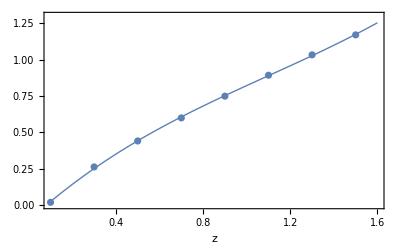

```mathematica
Show[ListPlot[Table[{zmag[[k]],smodel[5][[k]]},{k,1,Length[zmag]}],PlotRange->{{0.1,1.6},{0,1.3}},PlotStyle->{•,myblue},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{z,MaTeX["s"]},RotateLabel->True],Plot[{s[z]},{z,0.1,1.6},PlotStyle->{{myred, Thick}}]]
```

Split into bright and faint

```mathematica
lnn[Fl_]=Table[-a0[[k]]-a1[[k]]Log[Fl]-a2[[k]]Log[Fl]^2-a3[[k]]Log[Fl]^3,{k,1,Length[zmag]}];
```

```mathematica
For[k=1,k≤Length[zmag],k++,Fsol[k]=Solve[Log[2]+lnn[Fh][[k]]==lnn[5][[k]]&& Fh>5,Fh,Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Table[Fh/.Fsol[k],{k,1,Length[zmag]}]
```

{{42.4638},{11.5367},{8.6721},{7.61883},{7.05618},{6.70125},{6.45567},{6.27464}}

```mathematica
smodelBtab=Table[Flatten[{zmag[[k]],smodel[Fh/.Fsol[k]][[k]]}],{k,1,Length[zmag]}]
```

{{0.1,0.3044},{0.3,0.404588},{0.5,0.567938},{0.7,0.718575},{0.9,0.862255},{1.1,1.00177},{1.3,1.13815},{1.5,1.27238}}

```mathematica
smodelFtab=Table[{zmag[[k]],smodel[5][[k]]},{k,1,Length[zmag]}]
```

{{0.1,0.0177842},{0.3,0.261879},{0.5,0.440451},{0.7,0.599289},{0.9,0.748885},{1.1,0.893099},{1.3,1.03341},{1.5,1.17099}}

```mathematica
smodelB=Interpolation[smodelBtab];
smodelF=Interpolation[smodelFtab];
```

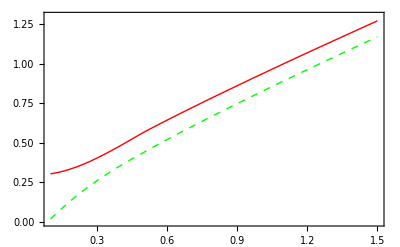

```mathematica
Plot[{smodelB[z],smodelF[z]},{z,0.1,1.5},PlotRange->{{0.1,1.5},{0,1.3}},PlotStyle->{{Red, Thick},{Green, Thick, Dashed}},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{MaTeX["z",Magnification->1.2],MaTeX["s(z)",Magnification->1.2]},RotateLabel->True]
```

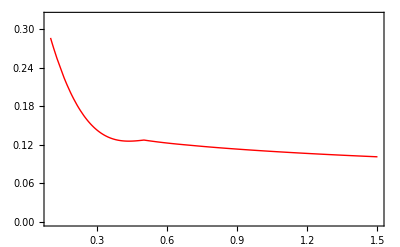

```mathematica
Plot[{smodelB[z]-smodelF[z]},{z,0.1,1.5},PlotRange->{{0.1,1.5},{0,0.32}},PlotStyle->{{Red, Thick},{Blue, Thick},{Orange, Thick}},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{MaTeX["z",Magnification->1.2],MaTeX["s(z)",Magnification->1.2]},RotateLabel->True]
```

## Signals

```mathematica
H0 =1/2997.9;
```

```mathematica
nu1baretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/signal/nu1_z0_fid.dat","Table"];
nu1=Interpolation[nu1baretab];
nu1z0[d_]:=d H0 nu1[d]
```

```mathematica
nu1z0 [100]
```

0.0000683573

```mathematica
mu0baretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/signal/mu0_z0_fid.dat","Table"];
mu0=Interpolation[mu0baretab];
mu0z0[d_]:=mu0[d];
```

```mathematica
mu0z0[100]
```

0.00178356

```mathematica
mu2baretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/signal/mu2_z0_fid.dat","Table"];
mu2=Interpolation[mu2baretab];
mu2z0[d_]:=mu2[d];
```

```mathematica
mu4baretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/signal/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:=mu4[d];
```

## Covariance

```mathematica
cov00CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_mono_bare.dat","Table"];
cov11CCbaretab=
Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/covariance_new_dipoleCC/covariance/varcosmic_dip_bare.dat","Table"];
cov22CCbaretab=
Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_quad_bare.dat","Table"];
cov44CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_hexa_bare.dat","Table"];
cov02CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_mult02_bare.dat","Table"];
cov04CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_mult04_bare.dat","Table"];
cov24CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varcosmic_mult24_bare.dat","Table"];
cov00CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_mono_bare.dat","Table"];
cov11CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_dip_bare.dat","Table"];
cov22CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_quad_bare.dat","Table"];
cov44CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_hexa_bare.dat","Table"];
cov02CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_mult02_bare.dat","Table"];
cov04CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_mult04_bare.dat","Table"];
cov24CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/varmix_mult24_bare.dat","Table"];
```

```mathematica
(*cov00CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_mono_smooth_bare.dat","Table"];
cov22CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_quad_smooth_bare.dat","Table"];
cov44CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_hexa_smooth_bare.dat","Table"];
cov02CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_mult02_smooth_bare.dat","Table"];
cov04CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_mult04_smooth_bare.dat","Table"];
cov24CCbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varcosmic_mult24_smooth_bare.dat","Table"];
cov00CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_mono_smooth_bare.dat","Table"];
cov11CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_dip_smooth_bare.dat","Table"];
cov22CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_quad_smooth_bare.dat","Table"];
cov44CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_hexa_smooth_bare.dat","Table"];
cov02CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_mult02_smooth_bare.dat","Table"];
cov04CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_mult04_smooth_bare.dat","Table"];
cov24CPbaretab=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/multipoles_signal_covariance/covariance/smooth_covariance/varmix_mult24_smooth_bare.dat","Table"];*)
```

## Sigma8 from CAMB

```mathematica
zsigma=Import["/Users/danielsb/Dropbox/PHD/Anisotropic Stress/zsigma.dat","Table"];
```

```mathematica
redz=zsigma[[All,1]]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.}

CAMB gives Sigma8 as a function of time. We reverse the order to have it as a function of redshift.

```mathematica
sigma8ztab=Reverse[zsigma[[All,2]]]
```

{0.824975,0.635256,0.501659,0.409978,0.345116,0.2974,0.261032,0.232477,0.209496,0.190621,0.17485,0.161479,0.150004,0.140048,0.13133,0.123633,0.116788,0.110662,0.105146,0.100154,0.0956157,0.0914708,0.0876709,0.0841745,0.0809467,0.0779578,0.0751822,0.0725979,0.0701857,0.067929,0.0658133,0.0638257,0.061955,0.0601911,0.0585252,0.0569493,0.0554563,0.0540398,0.0526942,0.0514141,0.0501951}

```mathematica
sigma8f=Interpolation[Table[{redz[[i]],sigma8ztab[[i]]},{i,1,Length[redz]}]];
```

```mathematica
Sigma8z0=sigma8f[0]
```

0.824975

```mathematica
Sigma8zSKA=Table[sigma8f[i],{i,0.15,1.95,0.1}]
```

{0.761321,0.722213,0.685633,0.651468,0.619606,0.589931,0.562331,0.536691,0.512898,0.490854,0.470441,0.451523,0.433979,0.41769,0.402444,0.388144,0.374799,0.362334,0.350671}

```mathematica
Sigma8z0
```

0.824975

# Cosmology

## Cosmic Parameters

```mathematica
Omm=0.3111;
Oml=1-Omm;
h=0.677;
H0=1/2997.9;
```

```mathematica
rH0[z_]:=Integrate[1/Sqrt[Omm x^3+Oml],{x,1,1+z}];
HH[z_]:=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}];
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
Ωm[z_]:= Omm(1+z)^3/(Omm(1+z)^3+Oml);
dmaxz[z_]:=(rH0[z+0.05]-rH0[z-0.05])/H0;
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3 + 1-Omm])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml));
```

```mathematica
Inttest[z_]:= Integrate[(1+x)/(Sqrt[Omm(1+x)^3 + 1-Omm])^3,{x,z,Infinity}]
```

```mathematica
Table[Inttest[zSKA[[i]]],{i,1,ktot}]
```

Table::iterb: Iterator {i,1,ktot} does not have appropriate bounds.

Table[Inttest[zSKA⟦i⟧],{i,1,ktot}]

```mathematica
Inttest[0.0]
```

1.01004

```mathematica
dHH[z_]:=D[HH[z],z];
```

```mathematica
dHH[z]
```

(0.3111-1.3778/(1+z)^3)/(2 √(0.6889/(1+z)^2+0.3111 (1+z)))

```mathematica
DHH[z_]:=(0.3111-1.3778000000000001/(1+z)^3)/(2 √(0.6889000000000001/(1+z)^2+0.3111 (1+z)))
```

```mathematica
DHHzSKA=DHH[zSKA[[1;;15]]]
```

Part::take: Cannot take positions 1 through 15 in zSKA.

(0.3111-1.3778/(1+zSKA⟦1;;15⟧)^3)/(2 √(0.6889/(1+zSKA⟦1;;15⟧)^2+0.3111 (1+zSKA⟦1;;15⟧)))

```mathematica
rH0[0.15]/H0
```

433.566

```mathematica
D10=D1[0]
```

0.785555

## Survey Parameters

Pixel size, deepness & pixel separations

```mathematica
Lp4=4;
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
ktot=Length[zSKA]
```

19

```mathematica
zSKA[[1;;15]]
```

{0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55}

```mathematica
dist=Table[i,{i,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
dtot=Length[dist]
```

43

Volume of the survey

```mathematica
VzSKA=Table[4/3 Pi (rH0[zSKA[[i]]+0.05]^3-rH0[zSKA[[i]]-0.05]^3)/H0^3 30000/41253,{i,1,ktot}]
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
dmaxzSKA=Table[dmaxz[zSKA[[i]]],{i,1,ktot}]
```

{278.094,263.291,248.608,234.312,220.595,207.58,195.337,183.892,173.241,163.359,154.209,145.746,137.922,130.688,123.997,117.803,112.063,106.74,101.796}

Cosmic values

```mathematica
fzSKA=Table[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=Table[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
D1zSKA=Table[D1[zSKA[[i]]],{i,1,ktot}];
HzSKA=Table[HH[zSKA[[i]]],{i,1,ktot}];
rH0zSKA=Table[rH0[zSKA[[i]]],{i,1,ktot}];
OmegaMzSKA=Table[Ωm[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=Table[dD1dz[zSKA[[i]]],{i,1,19}];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
```

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
evolzSKA
```

{0.853632,0.768011,0.691617,0.623826,0.563867,0.510922,0.464185,0.4229,0.386381,0.354014,0.325264,0.29966,0.276797,0.256325,0.237943,0.221391,0.206447,0.192917,0.180637}

```mathematica
HzSKA
```

{0.937375,0.910918,0.893299,0.88247,0.876897,0.875417,0.877138,0.881374,0.88759,0.895367,0.904377,0.91436,0.92511,0.936463,0.948287,0.960476,0.972944,0.985621,0.998452}

```mathematica
dD1dzSKA
```

{-0.384232,-0.362683,-0.339921,-0.316975,-0.294566,-0.27316,-0.25303,-0.234309,-0.217034,-0.201176,-0.18667,-0.17343,-0.161358,-0.150354,-0.140323,-0.131171,-0.122814,-0.115173,-0.108177}

```mathematica
fzSKA
```

{0.608806,0.658532,0.702429,0.740773,0.774015,0.802688,0.827348,0.848527,0.866717,0.882353,0.895817,0.907437,0.91749,0.926212,0.933804,0.940431,0.946234,0.951333,0.955826}

```mathematica
dfdzSKA
```

{0.52668,0.467852,0.410563,0.357081,0.308651,0.265749,0.228338,0.196072,0.16845,0.144914,0.124913,0.107934,0.0935179,0.0812663,0.0708368,0.0619395,0.0543306,0.0478059,0.042195}

Population biases

```mathematica
b1=0.554;
b2=0.783;
bTzSKA=b1 Exp[b2 zSKA]
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
db=1.0;
dbz=Table[db,{i,1,ktot}];
```

```mathematica
bBzSKA=bTzSKA+dbz/2;
bFzSKA=bTzSKA-dbz/2;
```

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
D1zSKA Sigma8z0/D10
```

{0.762213,0.722977,0.686078,0.651587,0.619483,0.589682,0.562064,0.536487,0.5128,0.490853,0.470499,0.451601,0.434031,0.417673,0.402417,0.388169,0.374839,0.362348,0.350626}

```mathematica
bBzSKA D1zSKA Sigma8z0/D10
```

{0.855997,0.848621,0.84296,0.839253,0.837661,0.838294,0.841222,0.846491,0.854134,0.864178,0.876649,0.89158,0.909009,0.928984,0.951566,0.976824,1.00484,1.03572,1.06956}

```mathematica
bFzSKA D1zSKA Sigma8z0/D10
```

{0.0937845,0.125644,0.156882,0.187666,0.218178,0.248612,0.279158,0.310004,0.341334,0.373325,0.40615,0.439979,0.474978,0.511312,0.549148,0.588655,0.630003,0.673368,0.718932}

```mathematica
-(1+zSKA)HzSKA dD1dzSKA
```

{0.414195,0.412968,0.409929,0.405596,0.400371,0.394562,0.388399,0.382051,0.375642,0.369258,0.362964,0.356799,0.350794,0.344963,0.339319,0.333864,0.3286,0.323523,0.318629}

```mathematica
HzSKA fzSKA D1zSKA
```

{0.414195,0.412968,0.409929,0.405596,0.400371,0.394562,0.388399,0.382051,0.375642,0.369258,0.362964,0.356799,0.350794,0.344963,0.339319,0.333864,0.3286,0.323523,0.318629}

```mathematica
sBzSKA=List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
szSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
sFzSKA=Table[2szSKA[[i]]-sBzSKA[[i]],{i,ktot}];
```

```mathematica
zSKA
```

{0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95}

```mathematica
sBzSKA
```

{0.224417,0.35789,0.470779,0.540386,0.60762,0.67992,0.753131,0.818644,0.880817,0.948577,1.02785,1.12008,1.21931,1.32188,1.42534,1.52897,1.6318,1.73335,1.83421}

```mathematica
sFzSKA
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
smodelB[0.0]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.301703

```mathematica
2smodelF[0.0]-smodelB[0.0]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.587991

```mathematica
(*Export["sBzSKA.txt",sBzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->True];
(*Export["sFzSKA.txt",sBzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->True];
(*Export["bBzSKA.txt",bBzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->True];
(*Export["bFzSKA.txt",bFzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->True];
```

```mathematica
NbarzSKA=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
```

```mathematica
NbarzSKA[[1;;15]]
```

{0.199814,0.116988,0.0696126,0.0422187,0.026008,0.0164685,0.0105386,0.00680012,0.00438301,0.00280384,0.00179188,0.00113765,0.000715463,0.00044797,0.00027555}

Population parameters

```mathematica
nBzSKA=0.5;
nFzSKA=0.5;
```

```mathematica
NbarBzSKA=nBzSKA NbarzSKA;
NbarFzSKA=nFzSKA NbarzSKA;
NtotBzSKA=NbarBzSKA VzSKA;
NtotFzSKA=NbarFzSKA VzSKA;
NtotzSKA=NbarzSKA VzSKA;
```

```mathematica
NbarBzSKA[[1;;15]]
```

{0.0999069,0.0584939,0.0348063,0.0211094,0.013004,0.00823427,0.00526929,0.00340006,0.00219151,0.00140192,0.00089594,0.000568825,0.000357731,0.000223985,0.000137775}

```mathematica
NbarFzSKA[[1;;15]]
```

{0.0999069,0.0584939,0.0348063,0.0211094,0.013004,0.00823427,0.00526929,0.00340006,0.00219151,0.00140192,0.00089594,0.000568825,0.000357731,0.000223985,0.000137775}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,19}]
NtotBSKA=Sum[NbarBzSKA[[k]]VzSKA[[k]],{k,1,19}]
NtotFSKA=Sum[NbarFzSKA[[k]]VzSKA[[k]],{k,1,19}]
```

9.21381×10^8

4.6069×10^8

4.6069×10^8

## Forecast Parameters

```mathematica
D1zSKA Sigma8z0/D10
```

{0.762213,0.722977,0.686078,0.651587,0.619483,0.589682,0.562064,0.536487,0.5128,0.490853,0.470499,0.451601,0.434031,0.417673,0.402417,0.388169,0.374839,0.362348,0.350626}

```mathematica
Sigma8zSKA
```

{0.761321,0.722213,0.685633,0.651468,0.619606,0.589931,0.562331,0.536691,0.512898,0.490854,0.470441,0.451523,0.433979,0.41769,0.402444,0.388144,0.374799,0.362334,0.350671}

```mathematica
bBzSKA
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

```mathematica
bFzSKA
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

```mathematica
bBzSKA-bFzSKA
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
bBtildezSKA=bBzSKA D1zSKA Sigma8z0/D10;
bFtildezSKA=bFzSKA D1zSKA Sigma8z0/D10;
βBzSKA=5 sBzSKA (1/(rH0zSKA HzSKA)-1);
βFzSKA= 5 sFzSKA (1/(rH0zSKA HzSKA)-1);
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
dGtildezSKA2=(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA)
```

{0.155781,0.0874221,0.030926,-0.0139201,-0.0482356,-0.0735575,-0.0915084,-0.103605,-0.111165,-0.115284,-0.116843,-0.116531,-0.114883,-0.112306,-0.109103,-0.105504,-0.101677,-0.0977435,-0.0937928}

```mathematica
GtildezSKA^2/Sigma8zSKA
```

{0.282841,0.313861,0.338735,0.35762,0.371058,0.379777,0.384553,0.386123,0.385141,0.382151,0.377617,0.371931,0.365406,0.358293,0.35088,0.343323,0.335651,0.327951,0.320292}

```mathematica
GtildezSKA fzSKA
```

{0.28251,0.31353,0.338515,0.357555,0.371131,0.379937,0.384735,0.38627,0.385215,0.382152,0.37757,0.371867,0.365362,0.358308,0.350904,0.3433,0.335616,0.327938,0.320333}

```mathematica
dazSKA=-1/(1+zSKA)
```

{-0.869565,-0.8,-0.740741,-0.689655,-0.645161,-0.606061,-0.571429,-0.540541,-0.512821,-0.487805,-0.465116,-0.444444,-0.425532,-0.408163,-0.392157,-0.377358,-0.363636,-0.350877,-0.338983}

```mathematica
Sigma8zSKA
```

{0.761321,0.722213,0.685633,0.651468,0.619606,0.589931,0.562331,0.536691,0.512898,0.490854,0.470441,0.451523,0.433979,0.41769,0.402444,0.388144,0.374799,0.362334,0.350671}

```mathematica
D1zSKA Sigma8z0/D10
```

{0.762213,0.722977,0.686078,0.651587,0.619483,0.589682,0.562064,0.536487,0.5128,0.490853,0.470499,0.451601,0.434031,0.417673,0.402417,0.388169,0.374839,0.362348,0.350626}

```mathematica
dHHzSKA=DHH[zSKA[[1;;19]]]
```

{-0.317283,-0.216449,-0.139313,-0.0797996,-0.0335792,0.00250479,0.030792,0.0530387,0.0705756,0.084419,0.0953506,0.103975,0.110762,0.116081,0.12022,0.123409,0.125829,0.127626,0.128915}

```mathematica
2/3 GtildezSKA (dazSKA dHHzSKA/HzSKA+dazSKA dGtildezSKA2/GtildezSKA+1)
```

{0.310106,0.331113,0.343123,0.348253,0.348303,0.344727,0.338657,0.330946,0.322225,0.312948,0.303438,0.29392,0.284545,0.275413,0.266588,0.258106,0.249986,0.242232,0.234842}

```mathematica
2/3 GtildezSKA dazSKA(dHHzSKA/HzSKA + dGtildezSKA2/GtildezSKA + 1/dazSKA)
```

{0.310106,0.331113,0.343123,0.348253,0.348303,0.344727,0.338657,0.330946,0.322225,0.312948,0.303438,0.29392,0.284545,0.275413,0.266588,0.258106,0.249986,0.242232,0.234842}

```mathematica
2/3 GtildezSKA (-(1+zSKA)dHHzSKA/HzSKA -(1+zSKA) dGtildezSKA2/GtildezSKA+ 1)
```

{0.310347,0.338825,0.361089,0.377434,0.388476,0.394977,0.39773,0.397476,0.394874,0.390484,0.384768,0.378097,0.370768,0.363011,0.355007,0.346891,0.338768,0.330713,0.322784}

```mathematica
IhatzSKA
```

{0.310347,0.338825,0.361089,0.377434,0.388476,0.394977,0.39773,0.397476,0.394874,0.390484,0.384768,0.378097,0.370768,0.363011,0.355007,0.346891,0.338768,0.330713,0.322784}

```mathematica
GtildezSKA
```

{0.46404,0.476104,0.481921,0.482678,0.479489,0.473331,0.465023,0.455224,0.444453,0.433106,0.421481,0.409799,0.398219,0.386853,0.375779,0.365046,0.354686,0.344714,0.335137}

```mathematica
fzSKA D1zSKA
```

{0.441866,0.453354,0.458893,0.459614,0.456577,0.450714,0.442802,0.433472,0.423215,0.41241,0.401341,0.390218,0.379191,0.368368,0.357823,0.347603,0.337737,0.328242,0.319123}

```mathematica
bBzSKA Sigma8zSKA
```

{0.854996,0.847724,0.842413,0.8391,0.837827,0.838648,0.841621,0.846813,0.854298,0.86418,0.876541,0.891425,0.9089,0.929023,0.95163,0.97676,1.00474,1.03568,1.0697}

```mathematica
bBtildezSKA
```

{0.855997,0.848621,0.84296,0.839253,0.837661,0.838294,0.841222,0.846491,0.854134,0.864178,0.876649,0.89158,0.909009,0.928984,0.951566,0.976824,1.00484,1.03572,1.06956}

```mathematica
bBtildezSKA[[9]]
```

0.854134

```mathematica
bFtildezSKA
```

{0.0937845,0.125644,0.156882,0.187666,0.218178,0.248612,0.279158,0.310004,0.341334,0.373325,0.40615,0.439979,0.474978,0.511312,0.549148,0.588655,0.630003,0.673368,0.718932}

```mathematica
bBtildezSKA-bFtildezSKA
```

{0.762213,0.722977,0.686078,0.651587,0.619483,0.589682,0.562064,0.536487,0.5128,0.490853,0.470499,0.451601,0.434031,0.417673,0.402417,0.388169,0.374839,0.362348,0.350626}

```mathematica
sBzSKA-sFzSKA
```

{0.246299,0.379887,0.449722,0.399929,0.328046,0.264841,0.211768,0.148772,0.0828196,0.0301904,-0.0011361,-0.00842916,-0.0070813,-0.00257236,-0.00176848,-0.00609512,-0.0173093,-0.0367989,-0.057416}

```mathematica
HzSKA
```

{0.937375,0.910918,0.893299,0.88247,0.876897,0.875417,0.877138,0.881374,0.88759,0.895367,0.904377,0.91436,0.92511,0.936463,0.948287,0.960476,0.972944,0.985621,0.998452}

```mathematica
Gf=Interpolation[Table[{zSKA[[i]], fzSKA[[i]]},{i,1,Length[zSKA]}]];
Gtilf=Interpolation[Table[{zSKA[[i]],D1zSKA[[i]] fzSKA[[i]]Sigma8z0/D10},{i,1,Length[zSKA]}]];
GD1f=Interpolation[Table[{zSKA[[i]],D1zSKA[[i]]},{i,1,Length[zSKA]}]];
```

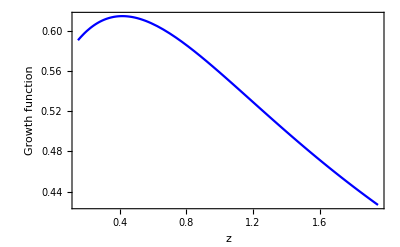

```mathematica
Plot[{Gtilf[z]/D10},{z,0.15,1.95},PlotRange->{All,All}, Axes->{True,True},Frame->True,PlotStyle->{{Blue},{Purple},{Black}},FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Growth function"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
fzSKA Sigma8zSKA
```

{0.463497,0.4756,0.481608,0.48259,0.479584,0.47353,0.465243,0.455397,0.444538,0.433107,0.421429,0.409728,0.398172,0.38687,0.375804,0.365022,0.354648,0.344701,0.335181}

## Five-point stencil method

```mathematica
Gtildef[z_]:=(Sigma8z0/D10) fz[z] D1[z];
```

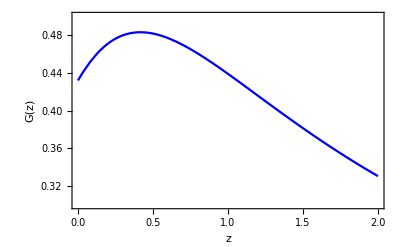

```mathematica
Plot[{Gtildef[z]},{z,0,2.0},PlotRange->{All,{0.3,0.5}},Axes->{True,True},AxesOrigin->{0.15,0},PlotStyle->{Blue,},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "G(z)"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Δz=0.1;
dGtildeStencil[z_]:=-(1+z)^(-1) H0 Sqrt[Omm(1+z)^3+1-Omm] (1+z) (-Gtildef[z+2 Δz]+ 8 Gtildef[z+Δz]-8 Gtildef[z-Δz]+Gtildef[z-2 Δz])/(12 Δz);
```

```mathematica
dGtildeStenciktot=Table[dGtildeStencil[i],{i,zSKA}]
```

{-0.0000560413,-0.0000332234,-0.0000124526,5.93561×10^-6,0.0000218679,0.000035443,0.0000468578,0.0000563541,0.0000641838,0.000070588,0.0000757864,0.0000799725,0.0000833133,0.0000859511,0.0000880053,0.000089576,0.0000907465,0.0000915861,0.0000921519}

Stencil method error

```mathematica
ErrorStenciktot=Abs[(dGtildeStenciktot-dGtildezSKA)/dGtildezSKA]
```

{0.000459162,0.000579322,0.000970084,0.000980523,0.0000546917,0.0000504311,0.0000730046,0.0000725961,0.0000646361,0.0000546925,0.0000449879,0.0000363691,0.0000290717,0.0000230611,0.0000181939,0.0000142951,0.0000111937,8.73768×10^-6,6.79822×10^-6}

```mathematica
ErrorStencilf=Interpolation[Table[{zSKA[[i]],ErrorStenciktot[[i]]},{i,1,ktot}]];
```

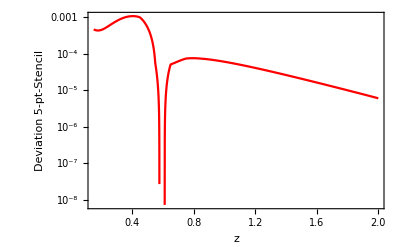

```mathematica
LogPlot[{ErrorStencilf[z]},{z,0.15,2.},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0.15,0},PlotStyle->{Red},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Deviation 5-pt-Stencil"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
dGtildef=Interpolation[Table[{zSKA[[i]],dGtildezSKA[[i]]},{i,1,ktot}]];
```

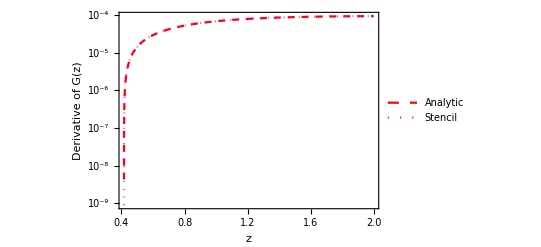

```mathematica
LogPlot[{dGtildef[z],dGtildeStencil[z]},{z,0.15,2.},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0.15,0},PlotStyle->{{Red,Dashed},{Magenta,Dotted}},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Derivative of G(z)"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Analytic,Stencil}]
```

# Signals

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{1.52899,1.52053,1.51026,1.50018,1.49199,1.48707,1.48651,1.4912,1.50185,1.51905,1.54334,1.57524,1.61528,1.66406,1.72221,1.79046,1.86967,1.9608,2.06497}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.118832,0.148404,0.178472,0.208941,0.23998,0.271924,0.305211,0.340339,0.377844,0.418289,0.462266,0.510401,0.563364,0.621877,0.686732,0.758796,0.839034,0.928521,1.02846}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

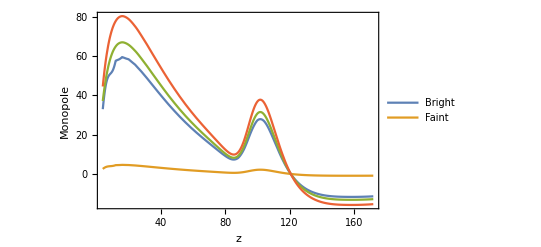

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d],d^2 MonopoleBright[[15]]mu0z0[d],d^2 MonopoleBright[[19]]mu0z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(rH0[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(sBzSKA-sFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA sFzSKA-bFzSKA sBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{9.58442,6.45739,4.59397,2.9275,1.82285,1.15263,0.752084,0.482323,0.313696,0.232745,0.213486,0.23159,0.261284,0.294857,0.329052,0.36469,0.403298,0.447018,0.494591}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{9.58442,6.45739,4.59397,2.9275,1.82285,1.15263,0.752084,0.482323,0.313696,0.232745,0.213486,0.23159,0.261284,0.294857,0.329052,0.36469,0.403298,0.447018,0.494591}

```mathematica
(HzSKA/Sigma8z0^2)
```

{1.37731,1.33844,1.31255,1.29664,1.28845,1.28627,1.2888,1.29503,1.30416,1.31559,1.32883,1.34349,1.35929,1.37597,1.39334,1.41125,1.42957,1.4482,1.46705}

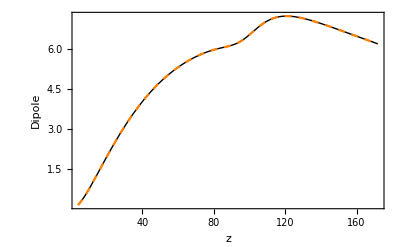

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)/Sigma8z0^2
```

{-0.000479463,-0.000287256,-0.000202384,-0.000153836,-0.000122171,-0.0000998478,-0.0000832926,-0.000070575,-0.0000605496,-0.0000524876,-0.0000459008,-0.0000404483,-0.0000358845,-0.0000320277,-0.0000287408,-0.0000259185,-0.0000234787,-0.0000213565,-0.0000195003}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

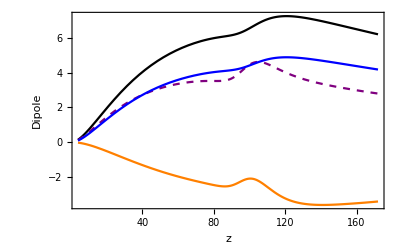

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d]),d^2 Dipole[[2]]nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed},{Blue}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipoled4to172=Table[{d,d^2 Dipole[[1]] nu1z0[d]},{d,4,172}];
```

```mathematica
Export["Dipole_d4to172.txt",Dipoled4to172,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]
```

Dipole_d4to172.txt

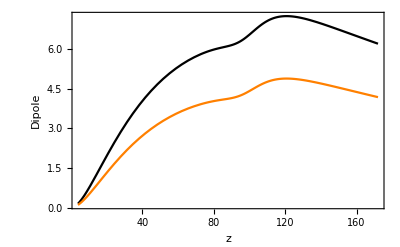

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d], d^2Dipole[[2]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed},{Blue}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez2d4to172=Table[{d,d^2 Dipole[[2]] nu1z0[d]},{d,4,172}];
```

```mathematica
Export["Dipole_z2_d4to172.txt",Dipolez2d4to172,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]
```

Dipole_z2_d4to172.txt

```mathematica
Dipoleatd20z=Table[{zSKA[[i]], 20^2 Dipole[[i]] nu1z0[20]},{i,1,19}]
```

{{0.15,1.94539},{0.25,1.31069},{0.35,0.932457},{0.45,0.594208},{0.55,0.369992},{0.65,0.233954},{0.75,0.152654},{0.85,0.0978993},{0.95,0.0636722},{1.05,0.0472412},{1.15,0.0433322},{1.25,0.0470068},{1.35,0.0530339},{1.45,0.0598483},{1.55,0.0667891},{1.65,0.0740227},{1.75,0.0818592},{1.85,0.0907332},{1.95,0.100389}}

```mathematica
Export["Dipole_d20asfz.txt",Dipoleatd20z,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]
```

Dipole_d20asfz.txt

Dipole redshift dependent part components as a function of redshift

```mathematica
gtilde2=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5)
```

{1.39735,1.27001,1.0262,0.662273,0.405952,0.248288,0.151062,0.0805398,0.0337154,0.00908637,-0.000245785,-0.00125095,-0.000662812,-0.000126604,-0.0000233027,0.0000983801,0.000692548,0.00218741,0.00432023}

```mathematica
gtilde=(HzSKA/Sigma8z0^2)(-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA)
```

{7.5103,4.58984,3.04242,1.80396,1.01147,0.547016,0.284859,0.12072,0.0288295,-0.001966,0.00995105,0.0478207,0.0931108,0.140176,0.186489,0.232707,0.28014,0.330697,0.383542}

```mathematica
gtildedot=(HzSKA/Sigma8z0^2)(-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{0.18807,0.105743,0.0375964,-0.017053,-0.0596755,-0.0920582,-0.116004,-0.133165,-0.144971,-0.152614,-0.15706,-0.15908,-0.159279,-0.15813,-0.155996,-0.153159,-0.149832,-0.14618,-0.142325}

```mathematica
Itilde=(HzSKA/Sigma8z0^2)((3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA)
```

{0.488705,0.491801,0.487746,0.478325,0.465105,0.449381,0.432167,0.414229,0.396122,0.378238,0.360841,0.3441,0.328115,0.312937,0.298582,0.285043,0.272298,0.260314,0.249054}

```mathematica
gtilde2f=Interpolation[Table[{zSKA[[i]],gtilde2[[i]]},{i,1,Length[gtilde2]}]];
gtildef=Interpolation[Table[{zSKA[[i]],gtilde[[i]]},{i,1,Length[gtilde]}]];
gtildedotf=Interpolation[Table[{zSKA[[i]],gtildedot[[i]]},{i,1,Length[gtildedot]}]];
Itildef=Interpolation[Table[{zSKA[[i]],Itilde[[i]]},{i,1,Length[Itilde]}]];
Dipolef=Interpolation[Table[{zSKA[[i]],Dipole[[i]]},{i,1,Length[Dipole]}]];
```

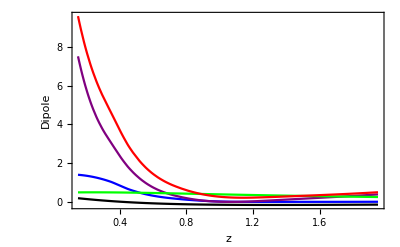

```mathematica
Plot[{gtilde2f[z],gtildef[z],gtildedotf[z],Itildef[z],Dipolef[z]},{z,0.15,1.95},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{All,All},PlotStyle->{{Blue},{Purple},{Black},{Green},{Red}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.958985,-0.981859,-0.990866,-0.989223,-0.979907,-0.965463,-0.94794,-0.92892,-0.909575,-0.890749,-0.873026,-0.856796,-0.842311,-0.829717,-0.819095,-0.810474,-0.803855,-0.79922,-0.796541}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.266056,-0.307512,-0.343117,-0.373072,-0.397985,-0.418648,-0.435884,-0.450464,-0.463065,-0.474261,-0.484523,-0.494233,-0.5037,-0.513169,-0.522839,-0.53287,-0.543392,-0.554515,-0.566331}

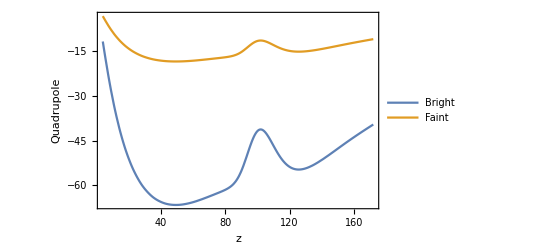

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

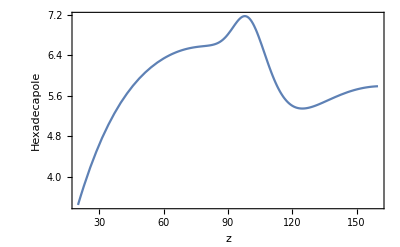

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
20^2 Hexadecapole[[1]] mu4z0[20]
```

3.44176

```mathematica
Sigma8z0^2
```

0.680584

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d]
```

## Joint plot

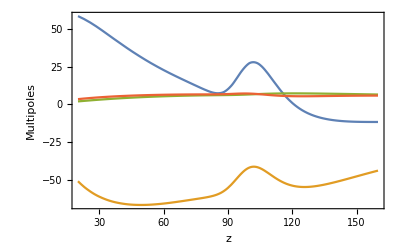

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
nu1z0[20]
```

0.000507436

```mathematica
160^2 MonopoleBf[160]
```

-11.6758

```mathematica
bBtildezSKA
```

{0.855997,0.848621,0.84296,0.839253,0.837661,0.838294,0.841222,0.846491,0.854134,0.864178,0.876649,0.89158,0.909009,0.928984,0.951566,0.976824,1.00484,1.03572,1.06956}

```mathematica
100^2Hexadecapolez1[100]
```

7.12459

# Covariance Matrix

## Parameters

```mathematica
zSKA
```

{0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95}

```mathematica
ktot=Length[zSKA]-7
{zSKA[[1]],zSKA[[ktot]]}
```

12

{0.15,1.25}

```mathematica
dist
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
dtot=Length[dist]-3
```

40

```mathematica
id=8;
dmin=dist[[id]];
dmax=dist[[dtot]];
Acc=1.0;
ldist=dtot-(id-1)
dims=(7*ktot+(ktot-4))ldist
{dmin,dmax}
```

33

3036

{32,160}

MIXED TERMS COEFFICIENTS

```mathematica
coeffCPBzSKA=evolzSKA/(VzSKA NbarBzSKA);
coeffCPFzSKA=evolzSKA/(VzSKA NbarFzSKA);
coeffCP2popzSKA=evolzSKA/(VzSKA NbarzSKA);
```

COSMIC VARIANCE COEFFICIENT

```mathematica
coeffCCzSKA=evolzSKA^2/VzSKA;
```

POISSON TERMS COEFFICIENT

```mathematica
coeffPzSKA=1/(NbarzSKA^2 VzSKA Lp4);
```

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5sBzSKA +(2-5sBzSKA)/(rH0zSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2)fzSKA
```

{4.86269,2.02195,0.932484,0.628558,0.475092,0.383335,0.35754,0.408273,0.501511,0.610278,0.729479,0.86635,1.03281,1.23101,1.45886,1.71253,1.98812,2.28184,2.59092}

```mathematica
cFzSKA=(5sFzSKA +(2-5sFzSKA)/(rH0zSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2)fzSKA
```

{9.64339,6.61639,4.87357,3.33524,2.24296,1.53596,1.10494,0.832692,0.690559,0.664425,0.727924,0.857964,1.02811,1.23006,1.45867,1.71335,1.99419,2.30199,2.63269}

## Terms

## Integrals

### Cosmic variance

```mathematica
covCC00ztab=Table[cov00CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC02ztab=Table[cov02CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC04ztab=Table[cov04CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC11ztab=Table[cov11CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC22ztab=Table[cov22CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC24ztab=Table[cov24CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCC44ztab=Table[cov44CCbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
```

```mathematica
covCC20ztab=Table[Transpose[covCC02ztab[[k,All,All]]],{k,1,ktot}];
covCC40ztab=Table[Transpose[covCC04ztab[[k,All,All]]],{k,1,ktot}];
covCC42ztab=Table[Transpose[covCC24ztab[[k,All,All]]],{k,1,ktot}];
```

### Mixed terms

```mathematica
covCP00ztab=Table[cov00CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP02ztab=Table[cov02CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP04ztab=Table[cov04CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP11ztab=Table[cov11CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP22ztab=Table[cov22CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP24ztab=Table[cov24CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
covCP44ztab=Table[cov44CPbaretab[[i,j]],{k,1,ktot},{i,5,47},{j,2,44}];
```

```mathematica
Table[covCP02ztab[[k,All,All]]==Transpose[covCP02ztab[[k,All,All]]],{k,1,ktot}]
```

{False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
covCP20ztab=Table[Transpose[covCP02ztab[[k,All,All]]],{k,1,ktot}];
covCP40ztab=Table[Transpose[covCP04ztab[[k,All,All]]],{k,1,ktot}];
covCP42ztab=Table[Transpose[covCP24ztab[[k,All,All]]],{k,1,ktot}];
```

### Possion terms

```mathematica
covPztab=Table[DiagonalMatrix[Table[1/(4i)^2, {i,1,dtot}]],{k,1,ktot}];
```

## Coefficients

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

COSMIC VARIANCE

```mathematica
coeffcosmicvariance[l_,m_,bL_,bM_,bN_,bP_,f_]:=Collect[1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[l,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[l,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+ (-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[l,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[l,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[l,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[l,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[l,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[l,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[l,m,4,4]),f,Simplify]
```

```mathematica
FactorCC[l_,m_]:= If[l==m, 1, (2l+1)(2m+1)(-1)^((l-m)/2)(-1)^(l+m)]
```

```mathematica
coeffvarCC[l_,m_,bL_,bM_,bN_,bP_,f_]:=  FactorCC[l,m]coeffcosmicvariance[l,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[1,1,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[1,1,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[1,1,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[1,1,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[bL,bM,bN,bP,cL,cM,cN,cP,f]
```

MIXED TERMS

```mathematica
coeffmixedterm[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/nL KroneckerDelta[bL,bN]+alpha0[bM,bN,f]/nL KroneckerDelta[bL,bP])(-1)^(m+l)+alpha0[bL,bN,f]/nM KroneckerDelta[bM,bP]+alpha0[bL,bP,f]/nM KroneckerDelta[bN,bM]) G[l,m,0,0]+((alpha2[bM,bP,f]/nL KroneckerDelta[bL,bN]+alpha2[bM,bN,f]/nL KroneckerDelta[bL,bP])(-1)^(m+l)+alpha2[bL,bN,f]/nM KroneckerDelta[bM,bP]+alpha2[bL,bP,f]/nM KroneckerDelta[bN,bM]) G[l,m,2,0]+((alpha4[bM,bP,f]/nL KroneckerDelta[bL,bN]+alpha4[bM,bN,f]/nL KroneckerDelta[bL,bP])(-1)^(m+l)+alpha4[bL,bN,f]/nM KroneckerDelta[bM,bP]+alpha4[bL,bP,f]/nM KroneckerDelta[bN,bM]) G[l,m,4,0]),f,Simplify]
```

```mathematica
FactorCP[l_,m_]:=If[l==m,1,2(2l+1)(2m+1)(-1)^((m-l)/2)(-1)^(m+l)]
```

```mathematica
FactorCP[0,2]
```

-10

```mathematica
coeffvarCP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=FactorCP[l,m] coeffmixedterm[l,m,nL,nM,bL,bM,bN,bP,f]
```

POISSON TERMS

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

## COSMIC VARIANCE

### MONOPOLE

```mathematica
coeffvarCC[0,0,b,b,b,b,f]
```

b^4+(4 b^3 f)/3+(6 b^2 f^2)/5+(4 b f^3)/7+f^4/9

ONE POPULATION

```mathematica
coeffvarCC00BzSKA=coeffCCzSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{5.14716×10^-9,2.0861×10^-9,1.18089×10^-9,7.91299×10^-10,5.87812×10^-10,4.68678×10^-10,3.93883×10^-10,3.45035×10^-10,3.12722×10^-10,2.91753×10^-10,2.79124×10^-10,2.73059×10^-10,2.72527×10^-10,2.76985×10^-10,2.86237×10^-10,3.00367×10^-10,3.19696×10^-10,3.44781×10^-10,3.76425×10^-10}

```mathematica
coeffvarCC00FzSKA=coeffCCzSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{5.88914×10^-11,3.46207×10^-11,2.67228×10^-11,2.33396×10^-11,2.18555×10^-11,2.14219×10^-11,2.17109×10^-11,2.25943×10^-11,2.40389×10^-11,2.60678×10^-11,2.87455×10^-11,3.2174×10^-11,3.64944×10^-11,4.18928×10^-11,4.86096×10^-11,5.69514×10^-11,6.73087×10^-11,8.01769×10^-11,9.61851×10^-11}

```mathematica
varCC00Bd4to160zSKA=Table[coeffvarCC00BzSKA[[k]] covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC00Fd4to160zSKA=Table[coeffvarCC00FzSKA[[k]] covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCC00BFzSKA=coeffCCzSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.76087×10^-10,2.38698×10^-10,1.61179×10^-10,1.25453×10^-10,1.0613×10^-10,9.49378×10^-11,8.84867×10^-11,8.5185×10^-11,8.42264×10^-11,8.52006×10^-11,8.79231×10^-11,9.23563×10^-11,9.85728×10^-11,1.0674×10^-10,1.17119×10^-10,1.3007×10^-10,1.46066×10^-10,1.65718×10^-10,1.89802×10^-10}

```mathematica
varCC00BFd4to160zSKA=Table[coeffvarCC00BFzSKA[[k]] covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCC[0,0,bB,bF,bB,bF,f]
```

bB^2 bF^2+2/3 bB bF (bB+bF) f+1/5 (bB^2+4 bB bF+bF^2) f^2+2/7 (bB+bF) f^3+f^4/9

```mathematica
coeffvarCC002popzSKA=coeffCCzSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.76087×10^-10,2.38698×10^-10,1.61179×10^-10,1.25453×10^-10,1.0613×10^-10,9.49378×10^-11,8.84867×10^-11,8.5185×10^-11,8.42264×10^-11,8.52006×10^-11,8.79231×10^-11,9.23563×10^-11,9.85728×10^-11,1.0674×10^-10,1.17119×10^-10,1.3007×10^-10,1.46066×10^-10,1.65718×10^-10,1.89802×10^-10}

```mathematica
varCC002popd4to160zSKA=Table[coeffvarCC002popzSKA[[k]]covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCC00B2popzSKA=coeffCCzSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.47991×10^-9,6.76238×10^-10,4.22143×10^-10,3.07057×10^-10,2.44745×10^-10,2.07574×10^-10,1.84327×10^-10,1.69719×10^-10,1.61004×10^-10,1.56673×10^-10,1.55884×10^-10,1.5819×10^-10,1.63407×10^-10,1.71542×10^-10,1.82762×10^-10,1.9738×10^-10,2.15861×10^-10,2.38835×10^-10,2.67126×10^-10}

```mathematica
coeffvarCC00F2popzSKA= coeffCCzSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.63989×10^-10,8.92101×10^-11,6.45389×10^-11,5.33212×10^-11,4.75504×10^-11,4.46054×10^-11,4.34247×10^-11,4.35299×10^-11,4.47057×10^-11,4.68768×10^-11,5.00556×10^-11,5.43209×10^-11,5.98106×10^-11,6.67226×10^-11,7.53215×10^-11,8.59508×10^-11,9.90494×10^-11,1.15174×10^-10,1.35031×10^-10}

```mathematica
varCC00B2popd4to160zSKA=Table[coeffvarCC00B2popzSKA[[k]]covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC00F2popd4to160zSKA=Table[coeffvarCC00F2popzSKA[[k]]covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### DIPOLE

```mathematica
coeffvarCC[1,1,b,b,b,b,f]
```

0

```mathematica
coeffvarCC[1,1,bB,bF,bB,bF,f]
```

0

```mathematica
coeffCCzSKA coeffvarCC[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.04792×10^-26,1.69324×10^-26,4.74529×10^-27,6.13998×10^-27,-3.68609×10^-27,-3.61699×10^-27,-2.99528×10^-27,5.35941×10^-27,-4.03432×10^-27,6.57655×10^-27,-4.04202×10^-27,5.69601×10^-27,-2.52764×10^-27,-3.84158×10^-27,-7.18586×10^-28,-7.23346×10^-27,-1.31529×10^-26,-7.54464×10^-27,-6.85019×10^-27}

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.98513×10^-8,3.75377×10^-9,1.09949×10^-9,3.03334×10^-10,8.82526×10^-11,2.82873×10^-11,1.00961×10^-11,3.57712×10^-12,1.32525×10^-12,6.50409×10^-13,5.01669×10^-13,5.56017×10^-13,6.75568×10^-13,8.28234×10^-13,9.9959×10^-13,1.19713×10^-12,1.43533×10^-12,1.73748×10^-12,2.10398×10^-12}

```mathematica
varCC11reld4to160zSKA=Table[coeffvarCC11relzSKA[[k]] covCC11ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### QUADRUPOLE

```mathematica
coeffvarCC[2,2,b,b,b,b,f]
```

b^4/5+(44 b^3 f)/105+(18 b^2 f^2)/35+(68 b f^3)/231+(83 f^4)/1287

ONE POPULATION

```mathematica
coeffvarCC22BzSKA=coeffCCzSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.49198×10^-9,6.10956×10^-10,3.47834×10^-10,2.33506×10^-10,1.73208×10^-10,1.37529×10^-10,1.14843×10^-10,9.97751×10^-11,8.95568×10^-11,8.2647×10^-11,7.81418×10^-11,7.5495×10^-11,7.43758×10^-11,7.45928×10^-11,7.60519×10^-11,7.87329×10^-11,8.26777×10^-11,8.79851×10^-11,9.48117×10^-11}

```mathematica
coeffvarCC22FzSKA=coeffCCzSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.03935×10^-11,1.72406×10^-11,1.28486×10^-11,1.08337×10^-11,9.78899×10^-12,9.25244×10^-12,9.03719×10^-12,9.05975×10^-12,9.28331×10^-12,9.69607×10^-12,1.03021×10^-11,1.11177×10^-11,1.21702×10^-11,1.34984×10^-11,1.51539×10^-11,1.72038×10^-11,1.97335×10^-11,2.28519×10^-11,2.66965×10^-11}

```mathematica
coeffvarCC22BFzSKA=coeffCCzSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.9946×10^-10,9.70881×10^-11,6.37533×10^-11,4.82884×10^-11,3.97588×10^-11,3.4613×10^-11,3.13937×10^-11,2.94086×10^-11,2.8297×10^-11,2.7862×10^-11,2.79968×10^-11,2.86504×10^-11,2.98097×10^-11,3.14915×10^-11,3.37385×10^-11,3.6619×10^-11,4.02288×10^-11,4.46948×10^-11,5.01808×10^-11}

```mathematica
varCC22Bd4to160zSKA=Table[coeffvarCC22BzSKA[[k]] covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC22Fd4to160zSKA=Table[coeffvarCC22FzSKA[[k]] covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC22BFd4to160zSKA=Table[coeffvarCC22BFzSKA[[k]] covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCC[2,2,bB,bF,bB,bF,f]
```

(bB^2 bF^2)/5+22/105 bB bF (bB+bF) f+3/35 (bB^2+4 bB bF+bF^2) f^2+34/231 (bB+bF) f^3+(83 f^4)/1287

```mathematica
coeffvarCC222popzSKA=coeffCCzSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.9946×10^-10,9.70881×10^-11,6.37533×10^-11,4.82884×10^-11,3.97588×10^-11,3.4613×10^-11,3.13937×10^-11,2.94086×10^-11,2.8297×10^-11,2.7862×10^-11,2.79968×10^-11,2.86504×10^-11,2.98097×10^-11,3.14915×10^-11,3.37385×10^-11,3.6619×10^-11,4.02288×10^-11,4.46948×10^-11,5.01808×10^-11}

```mathematica
varCC222popd4to160zSKA=Table[coeffvarCC222popzSKA[[k]]covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCC22B2popzSKA=coeffCCzSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.28048×10^-10,2.3746×10^-10,1.4595×10^-10,1.0448×10^-10,8.18991×10^-11,6.82553×10^-11,5.95159×10^-11,5.37767×10^-11,5.00416×10^-11,4.77528×10^-11,4.65869×10^-11,4.63569×10^-11,4.69625×10^-11,4.8364×10^-11,5.05681×10^-11,5.36215×10^-11,5.76091×10^-11,6.26556×10^-11,6.89296×10^-11}

```mathematica
coeffvarCC22F2popzSKA= coeffCCzSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.73861×10^-11,4.06653×10^-11,2.84528×10^-11,2.27446×10^-11,1.96249×10^-11,1.7809×10^-11,1.67692×10^-11,1.62576×10^-11,1.615×10^-11,1.63848×10^-11,1.69368×10^-11,1.78055×10^-11,1.90091×10^-11,2.0583×10^-11,2.25797×10^-11,2.50706×10^-11,2.8149×10^-11,3.19344×10^-11,3.65789×10^-11}

```mathematica
varCC22B2popd4to160zSKA=Table[coeffvarCC22B2popzSKA[[k]]covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC22F2popd4to160zSKA=Table[coeffvarCC22F2popzSKA[[k]]covCC22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### HEXADECAPOLE

```mathematica
coeffvarCC[4,4,b,b,b,b,f]
```

b^4/9+(52 b^3 f)/231+(1286 b^2 f^2)/5005+(436 b f^3)/3003+(79 f^4)/2431

TOTAL

```mathematica
coeffvarCC44TzSKA=coeffCCzSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCC44Td4to160zSKA=Table[coeffvarCC44TzSKA[[k]] covCC44ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### MONO - QUAD

```mathematica
coeffvarCC[0,2,b,b,b,b,f]
```

-5 ((8 b^3 f)/15+(24 b^2 f^2)/35+(8 b f^3)/21+(8 f^4)/99)

ONE POPULATION

```mathematica
coeffvarCC0B2BzSKA=coeffCCzSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-6.60289×10^-9,-2.75171×10^-9,-1.58147×10^-9,-1.06481×10^-9,-7.87998×10^-10,-6.2142×10^-10,-5.13377×10^-10,-4.39729×10^-10,-3.87894×10^-10,-3.5076×10^-10,-3.24061×10^-10,-3.05116×10^-10,-2.92193×10^-10,-2.84152×10^-10,-2.80244×10^-10,-2.79989×10^-10,-2.83103×10^-10,-2.89454×10^-10,-2.99032×10^-10}

```mathematica
coeffvarCC0B2FzSKA=coeffCCzSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.26462×10^-9,-6.06515×10^-10,-3.92107×10^-10,-2.92062×10^-10,-2.3613×10^-10,-2.01497×10^-10,-1.78778×10^-10,-1.63472×10^-10,-1.5318×10^-10,-1.46532×10^-10,-1.42701×10^-10,-1.41182×10^-10,-1.4167×10^-10,-1.4399×10^-10,-1.48066×10^-10,-1.53896×10^-10,-1.61541×10^-10,-1.71118×10^-10,-1.82801×10^-10}

```mathematica
coeffvarCC0F2FzSKA= coeffCCzSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.94281×10^-10,-1.10325×10^-10,-8.21029×10^-11,-6.89552×10^-11,-6.18963×10^-11,-5.79539×10^-11,-5.59025×10^-11,-5.51656×10^-11,-5.54527×10^-11,-5.66164×10^-11,-5.8591×10^-11,-6.13625×10^-11,-6.49544×10^-11,-6.94212×10^-11,-7.48451×10^-11,-8.13364×10^-11,-8.90348×10^-11,-9.81126×10^-11,-1.08779×10^-10}

```mathematica
varCC0B2Bd4to160zSKA=Table[coeffvarCC0B2BzSKA[[k]] covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC2B0Bd4to160zSKA=Table[coeffvarCC0B2BzSKA[[k]] covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC0B2Fd4to160zSKA=Table[coeffvarCC0B2FzSKA[[k]] covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC0F2Bd4to160zSKA=varCC0B2Fd4to160zSKA;
varCC2B0Fd4to160zSKA=Table[coeffvarCC0B2FzSKA[[k]] covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC2F0Bd4to160zSKA=varCC2B0Fd4to160zSKA;
varCC0F2Fd4to160zSKA=Table[coeffvarCC0F2FzSKA[[k]] covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC2F0Fd4to160zSKA=Table[coeffvarCC0F2FzSKA[[k]] covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCC02pop2B=coeffCCzSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-3.0985×10^-9,-1.36518×10^-9,-8.23495×10^-10,-5.78658×10^-10,-4.44924×10^-10,-3.63263×10^-10,-3.09819×10^-10,-2.73324×10^-10,-2.47844×10^-10,-2.29997×10^-10,-2.17746×10^-10,-2.09813×10^-10,-2.05384×10^-10,-2.03939×10^-10,-2.05159×10^-10,-2.08868×10^-10,-2.15004×10^-10,-2.23595×10^-10,-2.34749×10^-10}

```mathematica
coeffCCzSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.0985×10^-9,-1.36518×10^-9,-8.23495×10^-10,-5.78658×10^-10,-4.44924×10^-10,-3.63263×10^-10,-3.09819×10^-10,-2.73324×10^-10,-2.47844×10^-10,-2.29997×10^-10,-2.17746×10^-10,-2.09813×10^-10,-2.05384×10^-10,-2.03939×10^-10,-2.05159×10^-10,-2.08868×10^-10,-2.15004×10^-10,-2.23595×10^-10,-2.34749×10^-10}

```mathematica
varCC02pop2Bd4to160zSKA=Table[coeffvarCC02pop2B[[k]]covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC0B22popd4to160zSKA=varCC02pop2Bd4to160zSKA;
varCC2B02popd4to160zSKA=Table[coeffvarCC02pop2B[[k]]covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC22pop0Bd4to160zSKA=Table[coeffvarCC02pop2B[[k]]covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCC02pop2F=coeffCCzSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-4.97725×10^-10,-2.60099×10^-10,-1.8056×10^-10,-1.42878×10^-10,-1.21744×10^-10,-1.08827×10^-10,-1.00668×10^-10,-9.56067×10^-11,-9.27634×10^-11,-9.16448×10^-11,-9.19686×10^-11,-9.35799×10^-11,-9.64071×10^-11,-1.00439×10^-10,-1.05713×10^-10,-1.12307×10^-10,-1.20341×10^-10,-1.29973×10^-10,-1.41405×10^-10}

```mathematica
varCC02pop2Fd4to160zSKA=Table[coeffvarCC02pop2F[[k]]covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC0F22popd4to160zSKA=varCC02pop2Fd4to160zSKA;
varCC22pop0Fd4to160zSKA=Table[coeffvarCC02pop2F[[k]]covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC2F02popd4to160zSKA=varCC22pop0Fd4to160zSKA;
```

```mathematica
coeffvarCC02pop22pop=coeffCCzSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.26462×10^-9,-6.06515×10^-10,-3.92107×10^-10,-2.92062×10^-10,-2.3613×10^-10,-2.01497×10^-10,-1.78778×10^-10,-1.63472×10^-10,-1.5318×10^-10,-1.46532×10^-10,-1.42701×10^-10,-1.41182×10^-10,-1.4167×10^-10,-1.4399×10^-10,-1.48066×10^-10,-1.53896×10^-10,-1.61541×10^-10,-1.71118×10^-10,-1.82801×10^-10}

```mathematica
varCC02pop22popd4to160zSKA=Table[coeffvarCC02pop22pop[[k]] covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC22pop02popd4to160zSKA=Table[coeffvarCC02pop22pop[[k]] covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### MONO - HEXA

```mathematica
coeffvarCC[0,4,b,b,b,b,f]
```

9 ((16 b^2 f^2)/105+(32 b f^3)/231+(16 f^4)/429)

ONE POPULATION

```mathematica
coeffvarCC0B4TzSKA=coeffCCzSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffCCzSKA coeffvarCC[0,4,bTzSKA,bTzSKA,bBzSKA,bBzSKA,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC0F4TzSKA=coeffCCzSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
varCC0B4Td4to160zSKA=Table[coeffvarCC0B4TzSKA[[k]] covCC04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T0Bd4to160zSKA=Table[coeffvarCC0B4TzSKA[[k]] covCC40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC0F4Td4to160zSKA=Table[coeffvarCC0F4TzSKA[[k]] covCC04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T0Fd4to160zSKA=Table[coeffvarCC0F4TzSKA[[k]] covCC40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCC02pop4TzSKA=coeffCCzSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
varCC02pop4Td4to160zSKA=Table[coeffvarCC02pop4TzSKA[[k]] covCC04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T02popd4to160zSKA=Table[coeffvarCC02pop4TzSKA[[k]] covCC40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### QUAD - HEXA

```mathematica
coeffvarCC[2,4,b,b,b,b,f]
```

-45 ((16 b^3 f)/105+(272 b^2 f^2)/1155+(464 b f^3)/3003+(16 f^4)/429)

ONE POPULATION

```mathematica
coeffvarCC2B4TzSKA=coeffCCzSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC2F4TzSKA=coeffCCzSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
varCC2B4Td4to160zSKA=Table[coeffvarCC2B4TzSKA[[k]] covCC24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T2Bd4to160zSKA=Table[coeffvarCC2B4TzSKA[[k]] covCC42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC2F4Td4to160zSKA=Table[coeffvarCC2F4TzSKA[[k]] covCC24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T2Fd4to160zSKA=Table[coeffvarCC2F4TzSKA[[k]] covCC42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCC22pop4TzSKA=coeffCCzSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
varCC22pop4Td4to160zSKA=Table[coeffvarCC22pop4TzSKA[[k]] covCC24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCC4T22popd4to160zSKA=Table[coeffvarCC22pop4TzSKA[[k]] covCC42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

## MIXED TERMS

### MONOPOLE

```mathematica
coeffvarCP[0,0,n,n,b,b,b,b,f]
```

b^2/n+(2 b f)/(3 n)+f^2/(5 n)

ONE POPULATION

```mathematica
coeffvarCP00BzSKA=coeffCPBzSKA coeffvarCP[0,0,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{3.12302×10^-8,2.16437×10^-8,2.06783×10^-8,2.29819×10^-8,2.78829×10^-8,3.52903×10^-8,4.64924×10^-8,6.31366×10^-8,8.85026×10^-8,1.28162×10^-7,1.89692×10^-7,2.87679×10^-7,4.47255×10^-7,7.07867×10^-7,1.15404×10^-6,1.92312×10^-6,3.27961×10^-6,5.77083×10^-6,0.0000104621}

```mathematica
coeffvarCP00FzSKA=coeffCPBzSKA coeffvarCP[0,0,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.42719×10^-9,2.11242×10^-9,2.44361×10^-9,3.20086×10^-9,4.48484×10^-9,6.45315×10^-9,9.54583×10^-9,1.44097×10^-8,2.2266×10^-8,3.52909×10^-8,5.68172×10^-8,9.32125×10^-8,1.55989×10^-7,2.64538×10^-7,4.60174×10^-7,8.15017×10^-7,1.47176×10^-6,2.73272×10^-6,5.21069×10^-6}

```mathematica
varCP00Bd4to160zSKA=Table[coeffvarCP00BzSKA[[k]] covCP00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP00Fd4to160zSKA=Table[coeffvarCP00FzSKA[[k]] covCP00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCP00BFzSKA=coeffCP2popzSKA coeffvarCP[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP00BFd4to160zSKA=Table[coeffvarCP00BFzSKA[[k]] covCC00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCP[0,0,nB,nF,bB,bF,bB,bF,f]
```

(f^2 (nB+nF) (1+bB,bF))/(20 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(4 nB nF)+(f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(12 nB nF)

```mathematica
coeffvarCP002popzSKA=coeffCP2popzSKA coeffvarCP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{8.41434×10^-9,5.93902×10^-9,5.78047×10^-9,6.54569×10^-9,8.09193×10^-9,1.04359×10^-8,1.40096×10^-8,1.93866×10^-8,2.76921×10^-8,4.08632×10^-8,6.16273×10^-8,9.5223×10^-8,1.50811×10^-7,2.43101×10^-7,4.03553×10^-7,6.84536×10^-7,1.18784×10^-6,2.12589×10^-6,3.91821×10^-6}

```mathematica
varCP002popd4to160zSKA=Table[coeffvarCP002popzSKA[[k]]covCP00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCP00B2popzSKA=coeffCP2popzSKA coeffvarCP[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.05542×10^-9,3.206×10^-9,3.41309×10^-9,4.15653×10^-9,5.45749×10^-9,7.40463×10^-9,1.03801×10^-8,1.49103×10^-8,2.19999×10^-8,3.33962×10^-8,5.16328×10^-8,8.15415×10^-8,1.31651×10^-7,2.15842×10^-7,3.63692×10^-7,6.25087×10^-7,1.09731×10^-6,1.98395×10^-6,3.68941×10^-6}

```mathematica
coeffvarCP00F2popzSKA= coeffCP2popzSKA coeffvarCP[0,0,nBzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.05542×10^-9,3.206×10^-9,3.41309×10^-9,4.15653×10^-9,5.45749×10^-9,7.40463×10^-9,1.03801×10^-8,1.49103×10^-8,2.19999×10^-8,3.33962×10^-8,5.16328×10^-8,8.15415×10^-8,1.31651×10^-7,2.15842×10^-7,3.63692×10^-7,6.25087×10^-7,1.09731×10^-6,1.98395×10^-6,3.68941×10^-6}

```mathematica
varCP00B2popd4to160zSKA=Table[coeffvarCP00B2popzSKA[[k]]covCP00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP00F2popd4to160zSKA=Table[coeffvarCP00F2popzSKA[[k]]covCP00ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### DIPOLE

TWO POPULATIONS

```mathematica
coeffvarCP[1,1,nB,nF,bB,bF,bB,bF,f]
```

(f^2 (nB+nF) (1+bB,bF))/(28 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(12 nB nF)+(f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(20 nB nF)

```mathematica
coeffvarCP112popzSKA=coeffCP2popzSKA coeffvarCP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.63884×10^-9,2.59145×10^-9,2.53565×10^-9,2.87755×10^-9,3.55566×10^-9,4.57352×10^-9,6.11255×10^-9,8.40893×10^-9,1.1927×10^-8,1.74599×10^-8,2.61043×10^-8,3.99654×10^-8,6.26936×10^-8,1.00075×10^-7,1.64492×10^-7,2.76274×10^-7,4.74721×10^-7,8.41435×10^-7,1.53624×10^-6}

```mathematica
varCP112popd4to160zSKA=Table[coeffvarCP112popzSKA[[k]] covCP11ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCP[1,1,nB,nF,bB,bB,bB,bF,f]
```

(f^2 (nB+nF) (1+bB,bF))/(28 nB nF)+(bB (nB+nF) (bF+bB bB,bF))/(12 nB nF)+(f (nB+nF) (bB+bF+2 bB bB,bF))/(20 nB nF)

```mathematica
coeffCP2popzSKA coeffvarCP[1,1,nBzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.18587×10^-9,1.68044×10^-9,1.74652×10^-9,2.08116×10^-9,2.67752×10^-9,3.56311×10^-9,4.90272×10^-9,6.91682×10^-9,1.00296×10^-8,1.49709×10^-8,2.27728×10^-8,3.5405×10^-8,5.63067×10^-8,9.09889×10^-8,1.51205×10^-7,2.56458×10^-7,4.44544×10^-7,7.94121×10^-7,1.45997×10^-6}

### QUADRUPOLE

```mathematica
coeffvarCP[2,2,1,1,b,b,b,b,f]
```

b^2/5+(22 b f)/105+(3 f^2)/35

ONE POPULATION

```mathematica
coeffvarCP22BzSKA=coeffCPBzSKA coeffvarCP[2,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{7.44974×10^-9,5.18929×10^-9,4.97193×10^-9,5.53084×10^-9,6.70548×10^-9,8.46935×10^-9,1.11225×10^-8,1.50431×10^-8,2.09868×10^-8,3.02305×10^-8,4.44891×10^-8,6.70658×10^-8,1.03621×10^-7,1.62964×10^-7,2.63987×10^-7,4.37116×10^-7,7.40731×10^-7,1.29529×10^-6,2.33396×10^-6}

```mathematica
coeffvarCP22FzSKA=coeffCPBzSKA coeffvarCP[2,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{8.80375×10^-10,7.34534×10^-10,8.182×10^-10,1.03525×10^-9,1.40444×10^-9,1.96039×10^-9,2.81798×10^-9,4.14018×10^-9,6.23591×10^-9,9.64839×10^-9,1.51855×10^-8,2.43888×10^-8,4.00102×10^-8,6.66034×10^-8,1.13871×10^-7,1.98456×10^-7,3.53053×10^-7,6.46513×10^-7,1.21702×10^-6}

```mathematica
coeffvarCP22BFzSKA=coeffCP2popzSKA coeffvarCP[2,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP22Bd4to160zSKA=Table[coeffvarCP22BzSKA[[k]] covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP22Fd4to160zSKA=Table[coeffvarCP22FzSKA[[k]] covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP22BFd4to160zSKA=Table[coeffvarCP22BFzSKA[[k]] covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCP[2,2,nB,nF,bB,bF,bB,bF,f]
```

(3 f^2 (nB+nF) (1+bB,bF))/(140 nB nF)+(bB^2 nB+bF^2 nF+bB bF (nB+nF) bB,bF)/(20 nB nF)+(11 f (2 (bB nB+bF nF)+(bB+bF) (nB+nF) bB,bF))/(420 nB nF)

```mathematica
coeffvarCP222popzSKA=coeffCP2popzSKA coeffvarCP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.08253×10^-9,1.48096×10^-9,1.44753×10^-9,1.64152×10^-9,2.02748×10^-9,2.60743×10^-9,3.48511×10^-9,4.79582×10^-9,6.80568×10^-9,9.96972×10^-9,1.49187×10^-8,2.28636×10^-8,3.59078×10^-8,5.73918×10^-8,9.44645×10^-8,1.58893×10^-7,2.73446×10^-7,4.8545×10^-7,8.87745×10^-7}

```mathematica
varCP222popd4to160zSKA=Table[coeffvarCP222popzSKA[[k]]covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCP22B2popzSKA=coeffCP2popzSKA coeffvarCP[2,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.21074×10^-9,9.34351×10^-10,9.74056×10^-10,1.16369×10^-9,1.50059×10^-9,2.00119×10^-9,2.75921×10^-9,3.90056×10^-9,5.66723×10^-9,8.47632×10^-9,1.29197×10^-8,2.01274×10^-8,3.20757×10^-8,5.194×10^-8,8.64923×10^-8,1.47003×10^-7,2.55339×10^-7,4.57062×10^-7,8.41985×10^-7}

```mathematica
coeffvarCP22F2popzSKA= coeffCP2popzSKA coeffvarCP[2,2,nBzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.21074×10^-9,9.34351×10^-10,9.74056×10^-10,1.16369×10^-9,1.50059×10^-9,2.00119×10^-9,2.75921×10^-9,3.90056×10^-9,5.66723×10^-9,8.47632×10^-9,1.29197×10^-8,2.01274×10^-8,3.20757×10^-8,5.194×10^-8,8.64923×10^-8,1.47003×10^-7,2.55339×10^-7,4.57062×10^-7,8.41985×10^-7}

```mathematica
varCP22B2popd4to160zSKA=Table[coeffvarCP22B2popzSKA[[k]]covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP22F2popd4to160zSKA=Table[coeffvarCP22F2popzSKA[[k]]covCP22ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### HEXADECAPOLE

```mathematica
coeffvarCP[4,4,1,1,b,b,b,b,f]
```

b^2/9+(26 b f)/231+(643 f^2)/15015

TOTAL

```mathematica
coeffvarCP44TzSKA=coeffCP2popzSKA coeffvarCP[4,4,1,1,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.86578×10^-10,6.50219×10^-10,6.52136×10^-10,7.55919×10^-10,9.5151×10^-10,1.24418×10^-9,1.68767×10^-9,2.35325×10^-9,3.37943×10^-9,5.00423×10^-9,7.56203×10^-9,1.1693×10^-8,1.85139×10^-8,2.98106×10^-8,4.93983×10^-8,8.35994×10^-8,1.4467×10^-7,2.58126×10^-7,4.74184×10^-7}

```mathematica
varCP44Td4to160zSKA=Table[coeffvarCP44TzSKA[[k]] covCP44ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### MONO - QUAD

```mathematica
coeffvarCP[0,2,n,n,bb,bb,bf,bf,f]
```

-10 ((2 (bb+bf) f bb,bf)/(15 n)+(4 f^2 bb,bf)/(35 n))

ONE POPULATION

```mathematica
coeffvarCP0B2BzSKA=coeffCPBzSKA coeffvarCP[0,2,1,1,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-3.91751×10^-8,-2.79522×10^-8,-2.71336×10^-8,-3.03086×10^-8,-3.66258×10^-8,-4.58237×10^-8,-5.92959×10^-8,-7.86597×10^-8,-1.07201×10^-7,-1.50305×10^-7,-2.14608×10^-7,-3.12947×10^-7,-4.66453×10^-7,-7.05901×10^-7,-1.09774×10^-6,-1.74105×10^-6,-2.8201×10^-6,-4.70436×10^-6,-8.07135×10^-6}

```mathematica
coeffvarCP0B2FzSKA=coeffCP2popzSKA coeffvarCP[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP0F2FzSKA= coeffCPFzSKA coeffvarCP[0,2,1,1,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.08686×10^-8,-8.75445×10^-9,-9.39582×10^-9,-1.14305×10^-8,-1.48754×10^-8,-1.98703×10^-8,-2.72656×10^-8,-3.81447×10^-8,-5.4576×10^-8,-8.00266×10^-8,-1.19106×10^-7,-1.8052×10^-7,-2.78938×10^-7,-4.3659×10^-7,-7.00701×10^-7,-1.1447×10^-6,-1.90634×10^-6,-3.26398×10^-6,-5.73863×10^-6}

```mathematica
varCP0B2Bd4to160zSKA=Table[coeffvarCP0B2BzSKA[[k]] covCP02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP2B0Bd4to160zSKA=Table[coeffvarCP0B2BzSKA[[k]] covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP0B2Fd4to160zSKA=Table[coeffvarCP0B2FzSKA[[k]] covCP02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP0F2Bd4to160zSKA=varCP0B2Fd4to160zSKA;
varCP2B0Fd4to160zSKA=Table[coeffvarCP0B2FzSKA[[k]] covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP2F0Bd4to160zSKA=varCP2B0Fd4to160zSKA;
varCP0F2Fd4to160zSKA=Table[coeffvarCP0F2FzSKA[[k]] covCC02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP2F0Fd4to160zSKA=Table[coeffvarCP0F2FzSKA[[k]] covCC20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCP02pop2B=coeffCP2popzSKA coeffvarCP[0,2,nBzSKA,nBzSKA,bBzSKA,bFzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-1.25109×10^-8,-9.17665×10^-9,-9.13235×10^-9,-1.04348×10^-8,-1.28753×10^-8,-1.64235×10^-8,-2.16404×10^-8,-2.92011×10^-8,-4.04442×10^-8,-5.75828×10^-8,-8.34284×10^-8,-1.23367×10^-7,-1.86348×10^-7,-2.85623×10^-7,-4.4961×10^-7,-7.21438×10^-7,-1.18161×10^-6,-1.99209×10^-6,-3.45249×10^-6}

```mathematica
coeffCP2popzSKA coeffvarCP[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.25109×10^-8,-9.17665×10^-9,-9.13235×10^-9,-1.04348×10^-8,-1.28753×10^-8,-1.64235×10^-8,-2.16404×10^-8,-2.92011×10^-8,-4.04442×10^-8,-5.75828×10^-8,-8.34284×10^-8,-1.23367×10^-7,-1.86348×10^-7,-2.85623×10^-7,-4.4961×10^-7,-7.21438×10^-7,-1.18161×10^-6,-1.99209×10^-6,-3.45249×10^-6}

```mathematica
varCP02pop2Bd4to160zSKA=Table[coeffvarCP02pop2B[[k]]covCP02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP0B22popd4to160zSKA=varCP02pop2Bd4to160zSKA;
varCP2B02popd4to160zSKA=Table[coeffvarCP02pop2B[[k]]covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP22pop0Bd4to160zSKA=Table[coeffvarCP02pop2B[[k]]covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarCP02pop2F=coeffCP2popzSKA coeffvarCP[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.25109×10^-8,-9.17665×10^-9,-9.13235×10^-9,-1.04348×10^-8,-1.28753×10^-8,-1.64235×10^-8,-2.16404×10^-8,-2.92011×10^-8,-4.04442×10^-8,-5.75828×10^-8,-8.34284×10^-8,-1.23367×10^-7,-1.86348×10^-7,-2.85623×10^-7,-4.4961×10^-7,-7.21438×10^-7,-1.18161×10^-6,-1.99209×10^-6,-3.45249×10^-6}

```mathematica
varCP02pop2Fd4to160zSKA=Table[coeffvarCP02pop2F[[k]]covCP02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP0F22popd4to160zSKA=varCP02pop2Fd4to160zSKA;
varCP22pop0Fd4to160zSKA=Table[coeffvarCP02pop2F[[k]]covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP2F02popd4to160zSKA=varCP22pop0Fd4to160zSKA;
```

```mathematica
coeffvarCP02pop22pop=coeffCP2popzSKA coeffvarCP[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.25109×10^-8,-9.17665×10^-9,-9.13235×10^-9,-1.04348×10^-8,-1.28753×10^-8,-1.64235×10^-8,-2.16404×10^-8,-2.92011×10^-8,-4.04442×10^-8,-5.75828×10^-8,-8.34284×10^-8,-1.23367×10^-7,-1.86348×10^-7,-2.85623×10^-7,-4.4961×10^-7,-7.21438×10^-7,-1.18161×10^-6,-1.99209×10^-6,-3.45249×10^-6}

```mathematica
varCP02pop22popd4to160zSKA=Table[coeffvarCP02pop22pop[[k]] covCP02ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP22pop02popd4to160zSKA=Table[coeffvarCP02pop22pop[[k]] covCP20ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### MONO - HEXA

```mathematica
coeffvarCP[0,4,1,1,b,b,b,b,f]
```

(16 f^2)/35

ONE POPULATION

```mathematica
coeffvarCP0B4TzSKA=coeffCPBzSKA coeffvarCP[0,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP0F4TzSKA=coeffCPFzSKA coeffvarCP[0,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP0B4Td4to160zSKA=Table[coeffvarCP0B4TzSKA[[k]] covCP04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T0Bd4to160zSKA=Table[coeffvarCP0B4TzSKA[[k]] covCP40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP0F4Td4to160zSKA=Table[coeffvarCP0F4TzSKA[[k]] covCP04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T0Fd4to160zSKA=Table[coeffvarCP0F4TzSKA[[k]] covCP40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCP02pop4TzSKA=coeffCP2popzSKA coeffvarCP[0,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP02pop4Td4to160zSKA=Table[coeffvarCP02pop4TzSKA[[k]] covCP04ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T02popd4to160zSKA=Table[coeffvarCP02pop4TzSKA[[k]] covCP40ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

### QUAD - HEXA

```mathematica
coeffvarCP[2,4,1,1,b,b,b,b,f]
```

-90 ((8 b f)/105+(136 f^2)/3465)

ONE POPULATION

```mathematica
coeffvarCP2B4TzSKA=coeffCPBzSKA coeffvarCP[2,4,1,1,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
coeffvarCP2F4TzSKA=coeffCPFzSKA coeffvarCP[2,4,1,1,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP2B4Td4to160zSKA=Table[coeffvarCP2B4TzSKA[[k]] covCP24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T2Bd4to160zSKA=Table[coeffvarCP2B4TzSKA[[k]] covCP42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP2F4Td4to160zSKA=Table[coeffvarCP2F4TzSKA[[k]] covCP24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T2Fd4to160zSKA=Table[coeffvarCP2F4TzSKA[[k]] covCP42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

TWO POPULATIONS

```mathematica
coeffvarCP22pop4TzSKA=coeffCP2popzSKA coeffvarCP[2,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCP22pop4Td4to160zSKA=Table[coeffvarCP22pop4TzSKA[[k]] covCP24ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varCP4T22popd4to160zSKA=Table[coeffvarCP22pop4TzSKA[[k]] covCP42ztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

## POISSON CONTRIBUTIONS

### MONOPOLE

```mathematica
coeffvarP[0,0,n,n,b,b,b,b,f]
```

1/(2 n^2 π)

ONE POPULATION

```mathematica
coeffvarP00BzSKA=coeffPzSKA coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.13454×10^-9,9.68246×10^-9,1.56518×10^-8,2.88753×10^-8,5.71813×10^-8,1.14673×10^-7,2.36169×10^-7,4.9547×10^-7,1.06991×10^-6,2.39455×10^-6,5.45846×10^-6,0.0000127745,0.0000307971,0.0000755657,0.00019352,0.000510029,0.00138822,0.00397108,0.0119145}

```mathematica
coeffvarP00FzSKA=coeffPzSKA coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{8.13454×10^-9,9.68246×10^-9,1.56518×10^-8,2.88753×10^-8,5.71813×10^-8,1.14673×10^-7,2.36169×10^-7,4.9547×10^-7,1.06991×10^-6,2.39455×10^-6,5.45846×10^-6,0.0000127745,0.0000307971,0.0000755657,0.00019352,0.000510029,0.00138822,0.00397108,0.0119145}

```mathematica
varP00Bd4to160zSKA=Table[coeffvarP00BzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varP00Fd4to160zSKA=Table[coeffvarP00FzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[0,0,nb,nf,bB,bB,bF,bF,f]
```

(bB,bF)^2/(2 nb nf π)

TWO POPULATIONS

```mathematica
coeffvarP[0,0,nb,nf,bB,bF,bB,bF,f]
```

(1+(bB,bF)^2)/(4 nb nf π)

```mathematica
coeffvarP002popzSKA=coeffPzSKA coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.06727×10^-9,4.84123×10^-9,7.82591×10^-9,1.44377×10^-8,2.85907×10^-8,5.73364×10^-8,1.18084×10^-7,2.47735×10^-7,5.34954×10^-7,1.19727×10^-6,2.72923×10^-6,6.38725×10^-6,0.0000153985,0.0000377829,0.0000967598,0.000255014,0.000694109,0.00198554,0.00595723}

```mathematica
varP002popd4to160zSKA=Table[coeffvarP002popzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[0,0,nb,nf,bB,bB,bB,bF,f]
```

(bB,bF)/(2 nb nf π)

### DIPOLE

```mathematica
coeffvarP[1,1,n,n,b,b,b,b,f]
```

0

```mathematica
coeffvarP[1,1,nB,nF,bB,bF,bB,bF,f]
```

(3 (1-(bB,bF)^2))/(4 nB nF π)

```mathematica
coeffvarP[1,1,nb,nf,bB,bB,bB,bF,f]
```

0

TWO POPULATIONS

```mathematica
coeffvarP112popzSKA=coeffPzSKA coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.22018×10^-8,1.45237×10^-8,2.34777×10^-8,4.3313×10^-8,8.5772×10^-8,1.72009×10^-7,3.54253×10^-7,7.43205×10^-7,1.60486×10^-6,3.59182×10^-6,8.18768×10^-6,0.0000191618,0.0000461956,0.000113349,0.000290279,0.000765043,0.00208233,0.00595663,0.0178717}

```mathematica
varP112popd4to160zSKA=Table[coeffvarP112popzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[1,1,nb,nf,bB,bB,bB,bF,f]
```

0

### QUADRUPOLE

```mathematica
coeffvarP[2,2,n,n,b,b,b,b,f]
```

5/(2 n^2 π)

ONE POPULATION

```mathematica
coeffvarP22BzSKA=coeffPzSKA coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{4.06727×10^-8,4.84123×10^-8,7.82591×10^-8,1.44377×10^-7,2.85907×10^-7,5.73364×10^-7,1.18084×10^-6,2.47735×10^-6,5.34954×10^-6,0.0000119727,0.0000272923,0.0000638725,0.000153985,0.000377829,0.000967598,0.00255014,0.00694109,0.0198554,0.0595723}

```mathematica
coeffvarP22FzSKA=coeffPzSKA coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.06727×10^-8,4.84123×10^-8,7.82591×10^-8,1.44377×10^-7,2.85907×10^-7,5.73364×10^-7,1.18084×10^-6,2.47735×10^-6,5.34954×10^-6,0.0000119727,0.0000272923,0.0000638725,0.000153985,0.000377829,0.000967598,0.00255014,0.00694109,0.0198554,0.0595723}

```mathematica
varP22Bd4to160zSKA=Table[coeffvarP22BzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
varP22Fd4to160zSKA=Table[coeffvarP22FzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[2,2,nb,nf,bB,bB,bF,bF,f]
```

(5 (bB,bF)^2)/(2 nb nf π)

TWO POPULATIONS

```mathematica
coeffvarP[2,2,nb,nf,bB,bF,bB,bF,f]
```

(5 (1+(bB,bF)^2))/(4 nb nf π)

```mathematica
coeffvarP222popzSKA=coeffPzSKA coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.03364×10^-8,2.42062×10^-8,3.91295×10^-8,7.21883×10^-8,1.42953×10^-7,2.86682×10^-7,5.90422×10^-7,1.23868×10^-6,2.67477×10^-6,5.98637×10^-6,0.0000136461,0.0000319363,0.0000769927,0.000188914,0.000483799,0.00127507,0.00347055,0.00992771,0.0297862}

```mathematica
varP222popd4to160zSKA=Table[coeffvarP222popzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[2,2,nb,nf,bB,bB,bB,bF,f]
```

(5 bB,bF)/(2 nb nf π)

### HEXADECAPOLE

```mathematica
coeffvarP[4,4,n,n,b,b,b,b,f]
```

9/(2 n^2 π)

ONE POPULATION

```mathematica
coeffvarP44TzSKA=coeffPzSKA coeffvarP[4,4,1,1,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.83027×10^-8,2.17855×10^-8,3.52166×10^-8,6.49694×10^-8,1.28658×10^-7,2.58014×10^-7,5.31379×10^-7,1.11481×10^-6,2.40729×10^-6,5.38774×10^-6,0.0000122815,0.0000287426,0.0000692934,0.000170023,0.000435419,0.00114756,0.00312349,0.00893494,0.0268076}

```mathematica
varP44Td4to160zSKA=Table[coeffvarP44TzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[4,4,nb,nf,bB,bB,bF,bF,f]
```

(9 (bB,bF)^2)/(2 nb nf π)

TWO POPULATIONS

```mathematica
coeffvarP[4,4,nb,nf,bB,bF,bB,bF,f]
```

(9 (1+(bB,bF)^2))/(4 nb nf π)

```mathematica
coeffvarP442popzSKA=coeffPzSKA coeffvarP[4,4,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varP442popd4to160zSKA=Table[coeffvarP442popzSKA[[k]] covPztab[[k,i,j]],{k,1,ktot},{i,1,dtot},{j,1,dtot}];
```

```mathematica
coeffvarP[0,0,nb,nf,bB,bB,bB,bF,f]
```

(bB,bF)/(2 nb nf π)

### CROSS-CORRELATIONS

```mathematica
coeffvarP[0,2,n,n,b,b,b,b,f]
```

0

```mathematica
coeffvarP[0,2,nB,nF,bB,bB,bF,bF,f]
```

0

```mathematica
coeffvarP[0,2,nB,nF,bB,bF,bB,bF,f]
```

0

```mathematica
coeffvarP[0,2,nB,nF,bB,bB,bB,bF,f]
```

0

The cross-correlation between different multipoles does not have any Poisson contribution.

## TOTAL VARIANCE

### MONOPOLE

```mathematica
var00Bd4to160zSKA=varCC00Bd4to160zSKA+varCP00Bd4to160zSKA+varP00Bd4to160zSKA;
var00Fd4to160zSKA=varCC00Fd4to160zSKA+varCP00Fd4to160zSKA+varP00Fd4to160zSKA;
var00BFd4to160zSKA=varCC00BFd4to160zSKA+varCP00BFd4to160zSKA;
var002popd4to160zSKA=varCC002popd4to160zSKA+varCP002popd4to160zSKA+varP002popd4to160zSKA;
var00B2popd4to160zSKA=varCC00B2popd4to160zSKA+varCP00B2popd4to160zSKA;
var00F2popd4to160zSKA=varCC00F2popd4to160zSKA+varCP00F2popd4to160zSKA;
```

### DIPOLE

```mathematica
var112popd4to160zSKA=varCC11reld4to160zSKA+varCP112popd4to160zSKA+varP112popd4to160zSKA;
```

```mathematica
diagvarz015 = Interpolation[Table[{4 i, var112popd4to160zSKA[[1,i,i]]}, {i,1,dtot}]];
```

```mathematica
diagCCz015 = Interpolation[Table[{4 i, varCC11reld4to160zSKA[[1,i,i]]}, {i,1,dtot}]];
diagCPz015=Interpolation[Table[{4 i, varCP112popd4to160zSKA[[1,i,i]]}, {i,1,dtot}]];
```

```mathematica
diagPz015 = Interpolation[Table[{4 i, varP112popd4to160zSKA[[1,i,i]]}, {i,1,dtot}]];
```

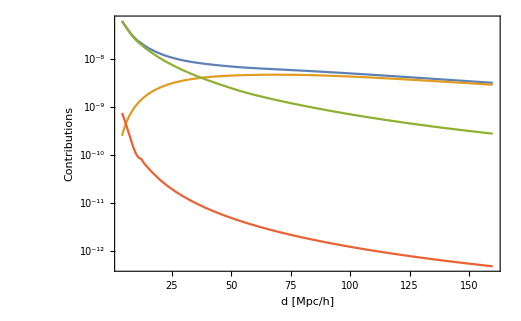

```mathematica
LogPlot[{diagvarz015[d],diagCCz015[d], diagCPz015[d], diagPz015[d]},{d,4,160},PlotStyle->{•,red},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Contributions"},RotateLabel->True]
```

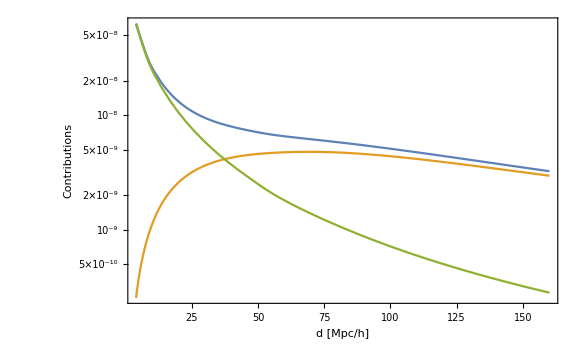

```mathematica
LogPlot[{diagvarz015[d],diagCCz015[d], diagCPz015[d]},{d,4,160},PlotStyle->{•,myred},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Contributions"},RotateLabel->True]
```

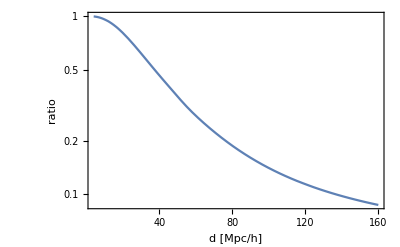

```mathematica
LogPlot[{(diagvarz015[d]-diagCCz015[d])/diagvarz015[d]},{d,4,160},PlotStyle->{•,myred},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","ratio"},RotateLabel->True]
```

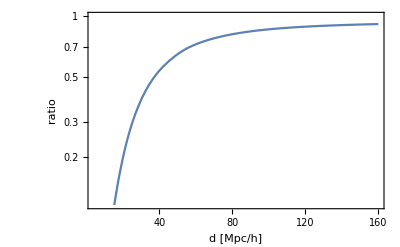

```mathematica
LogPlot[{(diagvarz015[d]-diagCPz015[d])/diagvarz015[d]},{d,4,160},PlotStyle->{•,myred},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","ratio"},RotateLabel->True]
```

```mathematica
Diagonal[varCC11reld4to160zSKA[[1]]]
```

{2.53631×10^-10,7.98417×10^-10,1.42545×10^-9,2.03649×10^-9,2.58881×10^-9,3.06687×10^-9,3.46851×10^-9,3.79799×10^-9,4.06245×10^-9,4.27015×10^-9,4.42972×10^-9,4.55005×10^-9,4.64×10^-9,4.70688×10^-9,4.75486×10^-9,4.78535×10^-9,4.79856×10^-9,4.79469×10^-9,4.77442×10^-9,4.73892×10^-9,4.68977×10^-9,4.62872×10^-9,4.55758×10^-9,4.47815×10^-9,4.39207×10^-9,4.30086×10^-9,4.20583×10^-9,4.10812×10^-9,4.00867×10^-9,3.90837×10^-9,3.80786×10^-9,3.70774×10^-9,3.60851×10^-9,3.51056×10^-9,3.41423×10^-9,3.31977×10^-9,3.22739×10^-9,3.13724×10^-9,3.04943×10^-9,2.96403×10^-9}

```mathematica
Diagonal[varCP112popd4to160zSKA[[1]]]
```

{6.2637×10^-8,3.23695×10^-8,2.05131×10^-8,1.4323×10^-8,1.06096×10^-8,8.18464×10^-9,6.50628×10^-9,5.29351×10^-9,4.38821×10^-9,3.69524×10^-9,3.15042×10^-9,2.70379×10^-9,2.33029×10^-9,2.03591×10^-9,1.80505×10^-9,1.61491×10^-9,1.45403×10^-9,1.31503×10^-9,1.194×10^-9,1.08747×10^-9,9.94069×10^-10,9.11449×10^-10,8.38115×10^-10,7.72782×10^-10,7.14477×10^-10,6.62285×10^-10,6.15373×10^-10,5.73139×10^-10,5.35003×10^-10,5.00839×10^-10,4.68986×10^-10,4.40349×10^-10,4.14196×10^-10,3.90236×10^-10,3.68282×10^-10,3.48088×10^-10,3.29419×10^-10,3.12228×10^-10,2.96343×10^-10,2.81638×10^-10}

```mathematica
Diagonal[varP112popd4to160zSKA[[1]]]
```

{7.62613×10^-10,1.90653×10^-10,8.47348×10^-11,4.76633×10^-11,3.05045×10^-11,2.11837×10^-11,1.55635×10^-11,1.19158×10^-11,9.41498×10^-12,7.62613×10^-12,6.30259×10^-12,5.29593×10^-12,4.5125×10^-12,3.89088×10^-12,3.38939×10^-12,2.97896×10^-12,2.6388×10^-12,2.35374×10^-12,2.1125×10^-12,1.90653×10^-12,1.72928×10^-12,1.57565×10^-12,1.44161×10^-12,1.32398×10^-12,1.22018×10^-12,1.12813×10^-12,1.04611×10^-12,9.72721×10^-13,9.06794×10^-13,8.47348×10^-13,7.93562×10^-13,7.4474×10^-13,7.00288×10^-13,6.597×10^-13,6.22541×10^-13,5.88436×10^-13,5.57059×10^-13,5.28126×10^-13,5.01389×10^-13,4.76633×10^-13}

### QUADRUPOLE

```mathematica
var22Bd4to160zSKA=varCC22Bd4to160zSKA+varCP22Bd4to160zSKA+varP22Bd4to160zSKA;
var22Fd4to160zSKA=varCC22Fd4to160zSKA+varCP22Fd4to160zSKA+varP22Fd4to160zSKA;
var22BFd4to160zSKA=varCC22BFd4to160zSKA+varCP22BFd4to160zSKA;
var222popd4to160zSKA=varCC222popd4to160zSKA+varCP222popd4to160zSKA+varP222popd4to160zSKA;
var22B2popd4to160zSKA=varCC22B2popd4to160zSKA+varCP22B2popd4to160zSKA;
var22F2popd4to160zSKA=varCC22F2popd4to160zSKA+varCP22F2popd4to160zSKA;
```

### HEXADECAPOLE

```mathematica
var44Td4to160zSKA=varCC44Td4to160zSKA+varCP44Td4to160zSKA+varP44Td4to160zSKA;
```

### MONO - QUAD

```mathematica
var0B2Bd4to160zSKA=varCC0B2Bd4to160zSKA+varCP0B2Bd4to160zSKA;
var2B0Bd4to160zSKA=varCC2B0Bd4to160zSKA+varCP2B0Bd4to160zSKA;
var0B2Fd4to160zSKA=varCC0B2Fd4to160zSKA+varCP0B2Fd4to160zSKA;
var0F2Bd4to160zSKA=varCC0F2Bd4to160zSKA+varCP0F2Bd4to160zSKA;
var2F0Bd4to160zSKA=varCC2F0Bd4to160zSKA+varCP2F0Bd4to160zSKA;
var2B0Fd4to160zSKA=varCC2B0Fd4to160zSKA+varCP2B0Fd4to160zSKA;
var0F2Fd4to160zSKA=varCC0F2Fd4to160zSKA+varCP0F2Fd4to160zSKA;
var2F0Fd4to160zSKA=varCC2F0Fd4to160zSKA+varCP2F0Fd4to160zSKA;
var0B22popd4to160zSKA=varCC0B22popd4to160zSKA+varCP0B22popd4to160zSKA;
var02pop2Bd4to160zSKA=varCC02pop2Bd4to160zSKA+varCP02pop2Bd4to160zSKA;
var22pop0Bd4to160zSKA=varCC22pop0Bd4to160zSKA+varCP22pop0Bd4to160zSKA;
var2B02popd4to160zSKA=varCC2B02popd4to160zSKA+varCP2B02popd4to160zSKA;
var0F22popd4to160zSKA=varCC0F22popd4to160zSKA+varCP0F22popd4to160zSKA;
var02pop2Fd4to160zSKA=varCC02pop2Fd4to160zSKA+varCP02pop2Fd4to160zSKA;
var22pop0Fd4to160zSKA=varCC22pop0Fd4to160zSKA+varCP22pop0Fd4to160zSKA;
var2F02popd4to160zSKA=varCC2F02popd4to160zSKA+varCP2F02popd4to160zSKA;
var02pop22popd4to160zSKA=varCC02pop22popd4to160zSKA+varCP02pop22popd4to160zSKA;
var22pop02popd4to160zSKA=varCC22pop02popd4to160zSKA+varCP22pop02popd4to160zSKA;
```

### MONO - HEXA

```mathematica
var0B4Td4to160zSKA=varCC0B4Td4to160zSKA+varCP0B4Td4to160zSKA;
var4T0Bd4to160zSKA=varCC4T0Bd4to160zSKA+varCP4T0Bd4to160zSKA;
var0F4Td4to160zSKA=varCC0F4Td4to160zSKA+varCP0F4Td4to160zSKA;
var4T0Fd4to160zSKA=varCC4T0Fd4to160zSKA+varCP4T0Fd4to160zSKA;
var02pop4Td4to160zSKA=varCC02pop4Td4to160zSKA+varCP02pop4Td4to160zSKA;
var4T02popd4to160zSKA=varCC4T02popd4to160zSKA+varCP4T02popd4to160zSKA;
```

### QUAD - HEXA

```mathematica
var2B4Td4to160zSKA=varCC2B4Td4to160zSKA+varCP2B4Td4to160zSKA;
var4T2Bd4to160zSKA=varCC4T2Bd4to160zSKA+varCP4T2Bd4to160zSKA;
var2F4Td4to160zSKA=varCC2F4Td4to160zSKA+varCP2F4Td4to160zSKA;
var4T2Fd4to160zSKA=varCC4T2Fd4to160zSKA+varCP4T2Fd4to160zSKA;
var22pop4Td4to160zSKA=varCC22pop4Td4to160zSKA+varCP22pop4Td4to160zSKA;
var4T22popd4to160zSKA=varCC4T22popd4to160zSKA+varCP4T22popd4to160zSKA;
```

## Covariance Matrix

```mathematica
dtot
```

40

```mathematica
id
```

8

## Elements

### DIPOLE

```mathematica
AutoCorrDip=Table[var112popd4to160zSKA[[k,i,j]],{k,3,ktot-2},{i,id,dtot},{j,id,dtot}];
CorrDipMono=Table[0.,{k,1,ktot-4},{i,id,dtot},{j,id,dtot}];
CorrDipQuad=Table[0.,{k,1,ktot-4},{i,id,dtot},{j,id,dtot}];
CorrDipHexa=Table[0.,{k,1,ktot-4},{i,id,dtot},{j,id,dtot}];
```

```mathematica
Dimensions[AutoCorrDip]
```

{8,33,33}

```mathematica
Dimensions[CorrDipMono]
```

{8,33,33}

### MONOPOLE

```mathematica
Dimensions[var00Bd4to160zSKA]
```

{12,40,40}

```mathematica
AutoCorrMonoB=Acc Table[var00Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
AutoCorrMonoF=Acc Table[var00Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
AutoCorrMono2pop=Acc Table[var002popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoBMonoF=Acc Table[var00BFd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMono2pop=Acc Table[var00B2popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popMonoB=CorrMonoBMono2pop;
CorrMonoFMono2pop=Acc Table[var00F2popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popMonoF=CorrMonoFMono2pop;
```

### QUADRUPOLE

```mathematica
AutoCorrQuadB=Acc Table[var22Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
AutoCorrQuadF=Acc Table[var22Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
AutoCorrQuad2pop=Acc Table[var222popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadBQuadF=Acc Table[var22BFd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBQuad2pop=Acc Table[var22B2popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popQuadB=CorrQuadBQuad2pop;
CorrQuadFQuad2pop=Acc Table[var22F2popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popQuadF=CorrQuadFQuad2pop;
```

### HEXADECAPOLE

```mathematica
AutoCorrHexa= Acc Table[var44Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
```

### MONO - QUAD

```mathematica
CorrMonoBQuadB=Acc Table[var0B2Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadBMonoB=Acc Table[var2B0Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoFQuadB=Acc Table[var0F2Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoBQuadF=Acc Table[var0B2Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadBMonoF=Acc Table[var2B0Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadFMonoB=Acc Table[var2F0Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoFQuadF=Acc Table[var0F2Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadFMonoF=Acc Table[var2F0Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoBQuad2pop=Acc Table[var0B22popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoFQuad2pop=Acc Table[var0F22popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popQuadB=Acc Table[var02pop2Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popQuadF=Acc Table[var02pop2Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadBMono2pop=Acc Table[var2B02popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadFMono2pop=Acc Table[var2F02popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popMonoB=Acc Table[var22pop0Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popMonoF=Acc Table[var22pop0Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popQuad2pop=Acc Table[var02pop22popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popMono2pop=Acc Table[var22pop02popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
```

### MONO - HEXA

```mathematica
CorrMonoBHexa=Acc Table[var0B4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMonoFHexa=Acc Table[var0F4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaMonoB=Acc Table[var4T0Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaMonoF=Acc Table[var4T0Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrMono2popHexa=Acc Table[var02pop4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaMono2pop=Acc Table[var4T02popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
```

### QUAD - HEXA

```mathematica
CorrQuadBHexa=Acc Table[var2B4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuadFHexa=Acc Table[var2F4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaQuadB=Acc Table[var4T2Bd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaQuadF=Acc Table[var4T2Fd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrQuad2popHexa=Acc Table[var22pop4Td4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
CorrHexaQuad2pop=Acc Table[var4T22popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,id,dtot},{j,id,dtot}];
```

## Building blocks

```mathematica
CovBlockDipole={};
For[j=1,j≤ktot-4,j++,
CovBlockDip[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrDip[[j]]](j-1)},{c,1,Length[AutoCorrDip[[j]]]}],AutoCorrDip[[j]],Table[0.,{r,1,Length[AutoCorrDip[[j]]](ktot-4-j)},{c,1,Length[AutoCorrDip[[j]]]}] ]];
CovBlockDipole=Join[CovBlockDipole,CovBlockDip[j]]]
```

```mathematica
CovBlockDipole[[4,6]]
```

1.35579×10^-9

```mathematica
AutoCorrDip[[2,1,3]]
```

2.00408×10^-9

```mathematica
Dimensions[CovBlockDipole]
```

{264,264}

```mathematica
CovBlockMonopoleBright={};
CovBlockQuadrupoleBright={};
CovBlockMonopoleBrightQuadrupoleBright={};
CovBlockQuadrupoleBrightMonopoleBright={};
CovBlockMonopoleBrightHexa={};
CovBlockHexaMonopoleBright={};
CovBlockQuadrupoleBrightHexa={};
CovBlockHexaQuadrupoleBright={};
For[j=1,j<=ktot,j++,
CovBlockMonoB[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrMonoB[[j]]](j-1)},{c,1,Length[AutoCorrMonoB[[j]]]}],AutoCorrMonoB[[j]],Table[0.,{r,1,Length[AutoCorrMonoB[[j]]](ktot-j)},{c,1,Length[AutoCorrMonoB[[j]]]}] ]];
CovBlockMonopoleBright=Join[CovBlockMonopoleBright,CovBlockMonoB[j]];
CovBlockQuadB[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrQuadB[[j]]](j-1)},{c,1,Length[AutoCorrQuadB[[j]]]}],AutoCorrQuadB[[j]],Table[0.,{r,1,Length[AutoCorrQuadB[[j]]](ktot-j)},{c,1,Length[AutoCorrQuadB[[j]]]}] ]];
CovBlockQuadrupoleBright=Join[CovBlockQuadrupoleBright,CovBlockQuadB[j]];
CovBlockMonoBQuadB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBQuadB[[j]]](j-1)},{c,1,Length[CorrMonoBQuadB[[j]]]}],Transpose[CorrMonoBQuadB[[j]]],Table[0.,{r,1,Length[CorrMonoBQuadB[[j]]](ktot-j)},{c,1,Length[CorrMonoBQuadB[[j]]]}] ]];
CovBlockMonopoleBrightQuadrupoleBright=Join[CovBlockMonopoleBrightQuadrupoleBright,CovBlockMonoBQuadB[j]];
CovBlockQuadBMonoB[j]=
Transpose[Join[Table[0.,{r,1,Length[CorrQuadBMonoB[[j]]](j-1)},{c,1,Length[CorrQuadBMonoB[[j]]]}],Transpose[CorrQuadBMonoB[[j]]],Table[0.,{r,1,Length[CorrQuadBMonoB[[j]]](ktot-j)},{c,1,Length[CorrMonoBQuadB[[j]]]}]]];
CovBlockQuadrupoleBrightMonopoleBright=Join[CovBlockQuadrupoleBrightMonopoleBright, CovBlockQuadBMonoB[j]];
CovBlockMonoBHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBHexa[[j]]](j-1)},{c,1,Length[CorrMonoBHexa[[j]]]}],Transpose[CorrMonoBHexa[[j]]],Table[0.,{r,1,Length[CorrMonoBHexa[[j]]](ktot-j)},{c,1,Length[CorrMonoBHexa[[j]]]}] ]];
CovBlockMonopoleBrightHexa=Join[CovBlockMonopoleBrightHexa,CovBlockMonoBHexa[j]];
CovBlockHexaMonoB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaMonoB[[j]]](j-1)},{c,1,Length[CorrHexaMonoB[[j]]]}],Transpose[CorrHexaMonoB[[j]]],Table[0.,{r,1,Length[CorrHexaMonoB[[j]]](ktot-j)},{c,1,Length[CorrHexaMonoB[[j]]]}] ]];
CovBlockHexaMonopoleBright=Join[CovBlockHexaMonopoleBright,CovBlockHexaMonoB[j]];
CovBlockQuadBHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadBHexa[[j]]](j-1)},{c,1,Length[CorrQuadBHexa[[j]]]}],Transpose[CorrQuadBHexa[[j]]],Table[0.,{r,1,Length[CorrQuadBHexa[[j]]](ktot-j)},{c,1,Length[CorrQuadBHexa[[j]]]}] ]];
CovBlockQuadrupoleBrightHexa=Join[CovBlockQuadrupoleBrightHexa,CovBlockQuadBHexa[j]];
CovBlockHexaQuadB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaQuadB[[j]]](j-1)},{c,1,Length[CorrHexaQuadB[[j]]]}],Transpose[CorrHexaQuadB[[j]]],Table[0.,{r,1,Length[CorrHexaQuadB[[j]]](ktot-j)},{c,1,Length[CorrHexaQuadB[[j]]]}] ]];
CovBlockHexaQuadrupoleBright=Join[CovBlockHexaQuadrupoleBright,CovBlockHexaQuadB[j]]]
```

```mathematica
CovBlockMonopoleFaint={};
CovBlockQuadrupoleFaint={};
CovBlockMonopoleBrightMonopoleFaint={};
CovBlockMonopoleFaintQuadrupoleBright={};
CovBlockQuadrupoleBrightMonopoleFaint={};
CovBlockQuadrupoleFaintMonopoleBright={};
CovBlockMonopoleBrightQuadrupoleFaint={};
CovBlockMonopoleFaintQuadrupoleFaint={};
CovBlockQuadrupoleFaintMonopoleFaint={};
CovBlockQuadrupoleBrightQuadrupoleFaint={};
CovBlockMonopoleFaintHexa={};
CovBlockHexaMonopoleFaint={};
CovBlockQuadrupoleFaintHexa={};
CovBlockHexaQuadrupoleFaint={};
For[j=1,j≤ktot,j++,
CovBlockMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrMonoF[[j]]](j-1)},{c,1,Length[AutoCorrMonoF[[j]]]}],AutoCorrMonoF[[j]],Table[0.,{r,1,Length[AutoCorrMonoF[[j]]](ktot-j)},{c,1,Length[AutoCorrMonoF[[j]]]}] ]];
CovBlockMonopoleFaint=Join[CovBlockMonopoleFaint,CovBlockMonoF[j]];
CovBlockQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrQuadF[[j]]](j-1)},{c,1,Length[AutoCorrQuadF[[j]]]}],AutoCorrQuadF[[j]],Table[0.,{r,1,Length[AutoCorrQuadF[[j]]](ktot-j)},{c,1,Length[AutoCorrQuadF[[j]]]}] ]];
CovBlockQuadrupoleFaint=Join[CovBlockQuadrupoleFaint,CovBlockQuadF[j]];CovBlockMonoBMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBMonoF[[j]]](j-1)},{c,1,Length[CorrMonoBMonoF[[j]]]}],CorrMonoBMonoF[[j]],Table[0.,{r,1,Length[CorrMonoBMonoF[[j]]](ktot-j)},{c,1,Length[CorrMonoBMonoF[[j]]]}] ]];
CovBlockMonopoleBrightMonopoleFaint=Join[CovBlockMonopoleBrightMonopoleFaint,CovBlockMonoBMonoF[j]];CovBlockMonoFQuadB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoFQuadB[[j]]](j-1)},{c,1,Length[CorrMonoFQuadB[[j]]]}],Transpose[CorrMonoFQuadB[[j]]],Table[0.,{r,1,Length[CorrMonoFQuadB[[j]]](ktot-j)},{c,1,Length[CorrMonoFQuadB[[j]]]}] ]];
CovBlockMonopoleFaintQuadrupoleBright=Join[CovBlockMonopoleFaintQuadrupoleBright,CovBlockMonoFQuadB[j]];
CovBlockQuadBMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadBMonoF[[j]]](j-1)},{c,1,Length[CorrQuadBMonoF[[j]]]}],Transpose[CorrQuadBMonoF[[j]]],Table[0.,{r,1,Length[CorrQuadBMonoF[[j]]](ktot-j)},{c,1,Length[CorrQuadBMonoF[[j]]]}] ]];
CovBlockQuadrupoleBrightMonopoleFaint=Join[CovBlockQuadrupoleBrightMonopoleFaint,CovBlockQuadBMonoF[j]];
CovBlockQuadFMonoB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadFMonoB[[j]]](j-1)},{c,1,Length[CorrQuadFMonoB[[j]]]}],Transpose[CorrQuadFMonoB[[j]]],Table[0.,{r,1,Length[CorrQuadFMonoB[[j]]](ktot-j)},{c,1,Length[CorrQuadFMonoB[[j]]]}] ]];
CovBlockQuadrupoleFaintMonopoleBright=Join[CovBlockQuadrupoleFaintMonopoleBright,CovBlockQuadFMonoB[j]];
CovBlockMonoBQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBQuadF[[j]]](j-1)},{c,1,Length[CorrMonoBQuadF[[j]]]}],Transpose[CorrMonoBQuadF[[j]]],Table[0.,{r,1,Length[CorrMonoBQuadF[[j]]](ktot-j)},{c,1,Length[CorrMonoBQuadF[[j]]]}] ]];
CovBlockMonopoleBrightQuadrupoleFaint=Join[CovBlockMonopoleBrightQuadrupoleFaint,CovBlockMonoBQuadF[j]];
CovBlockMonoFQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoFQuadF[[j]]](j-1)},{c,1,Length[CorrMonoFQuadF[[j]]]}],Transpose[CorrMonoFQuadF[[j]]],Table[0.,{r,1,Length[CorrMonoFQuadF[[j]]](ktot-j)},{c,1,Length[CorrMonoFQuadF[[j]]]}] ]];
CovBlockMonopoleFaintQuadrupoleFaint=Join[CovBlockMonopoleFaintQuadrupoleFaint,CovBlockMonoFQuadF[j]];
CovBlockQuadFMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadFMonoF[[j]]](j-1)},{c,1,Length[CorrQuadFMonoF[[j]]]}],Transpose[CorrQuadFMonoF[[j]]],Table[0.,{r,1,Length[CorrQuadFMonoF[[j]]](ktot-j)},{c,1,Length[CorrQuadFMonoF[[j]]]}] ]];
CovBlockQuadrupoleFaintMonopoleFaint=Join[CovBlockQuadrupoleFaintMonopoleFaint,CovBlockQuadFMonoF[j]];
CovBlockQuadBQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadBQuadF[[j]]](j-1)},{c,1,Length[CorrQuadBQuadF[[j]]]}],CorrQuadBQuadF[[j]],Table[0.,{r,1,Length[CorrQuadBQuadF[[j]]](ktot-j)},{c,1,Length[CorrQuadBQuadF[[j]]]}] ]];
CovBlockQuadrupoleBrightQuadrupoleFaint=Join[CovBlockQuadrupoleBrightQuadrupoleFaint,CovBlockQuadBQuadF[j]];
CovBlockMonoFHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoFHexa[[j]]](j-1)},{c,1,Length[CorrMonoFHexa[[j]]]}],Transpose[CorrMonoFHexa[[j]]],Table[0.,{r,1,Length[CorrMonoFHexa[[j]]](ktot-j)},{c,1,Length[CorrMonoFHexa[[j]]]}] ]];
CovBlockMonopoleFaintHexa=Join[CovBlockMonopoleFaintHexa,CovBlockMonoFHexa[j]];
CovBlockHexaMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaMonoF[[j]]](j-1)},{c,1,Length[CorrHexaMonoF[[j]]]}],Transpose[CorrHexaMonoF[[j]]],Table[0.,{r,1,Length[CorrHexaMonoF[[j]]](ktot-j)},{c,1,Length[CorrHexaMonoF[[j]]]}] ]];
CovBlockHexaMonopoleFaint=Join[CovBlockHexaMonopoleFaint,CovBlockHexaMonoF[j]];CovBlockQuadFHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadFHexa[[j]]](j-1)},{c,1,Length[CorrQuadFHexa[[j]]]}],Transpose[CorrQuadFHexa[[j]]],Table[0.,{r,1,Length[CorrQuadFHexa[[j]]](ktot-j)},{c,1,Length[CorrQuadFHexa[[j]]]}] ]];
CovBlockQuadrupoleFaintHexa=Join[CovBlockQuadrupoleFaintHexa,CovBlockQuadFHexa[j]];
CovBlockHexaQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaQuadF[[j]]](j-1)},{c,1,Length[CorrHexaQuadF[[j]]]}],Transpose[CorrHexaQuadF[[j]]],Table[0.,{r,1,Length[CorrHexaQuadF[[j]]](ktot-j)},{c,1,Length[CorrHexaQuadF[[j]]]}] ]];
CovBlockHexaQuadrupoleFaint=Join[CovBlockHexaQuadrupoleFaint,CovBlockHexaQuadF[j]]]
```

```mathematica
CovBlockMonopoleBF={};
CovBlockQuadrupoleBF={};
CovBlockMonopoleBrightMonopoleBF={};
CovBlockMonopoleFaintMonopoleBF={};
CovBlockMonopoleBrightQuadrupoleBF={};
CovBlockMonopoleBFQuadrupoleBright={};
CovBlockMonopoleFaintQuadrupoleBF={};
CovBlockMonopoleBFQuadrupoleFaint={};
CovBlockMonopoleBFQuadrupoleBF={};
CovBlockQuadrupoleBFMonopoleBright={};
CovBlockQuadrupoleBrightMonopoleBF={};
CovBlockQuadrupoleBFMonopoleFaint={};
CovBlockQuadrupoleFaintMonopoleBF={};
CovBlockQuadrupoleBFMonopoleBF={};
CovBlockQuadrupoleBrightQuadrupoleBF={};
CovBlockQuadrupoleFaintQuadrupoleBF={};
CovBlockMonopoleBFHexa={};
CovBlockHexaMonopoleBF={};
CovBlockQuadrupoleBFHexa={};
CovBlockHexaQuadrupoleBF={};
For[j=1,j≤ktot,j++,
CovBlockMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrMono2pop[[j]]](j-1)},{c,1,Length[AutoCorrMono2pop[[j]]]}],AutoCorrMono2pop[[j]],Table[0.,{r,1,Length[AutoCorrMono2pop[[j]]](ktot-j)},{c,1,Length[AutoCorrMono2pop[[j]]]}] ]];
CovBlockMonopoleBF=Join[CovBlockMonopoleBF,CovBlockMonoBF[j]];
CovBlockQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrQuad2pop[[j]]](j-1)},{c,1,Length[AutoCorrQuad2pop[[j]]]}],AutoCorrQuad2pop[[j]],Table[0.,{r,1,Length[AutoCorrQuad2pop[[j]]](ktot-j)},{c,1,Length[AutoCorrQuad2pop[[j]]]}] ]];
CovBlockQuadrupoleBF=Join[CovBlockQuadrupoleBF,CovBlockQuadBF[j]];
CovBlockMonoBMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBMono2pop[[j]]](j-1)},{c,1,Length[CorrMonoBMono2pop[[j]]]}],CorrMonoBMono2pop[[j]],Table[0.,{r,1,Length[CorrMonoBMono2pop[[j]]](ktot-j)},{c,1,Length[CorrMonoBMono2pop[[j]]]}] ]];
CovBlockMonopoleBrightMonopoleBF=Join[CovBlockMonopoleBrightMonopoleBF,CovBlockMonoBMonoBF[j]];
CovBlockMonoFMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoFMono2pop[[j]]](j-1)},{c,1,Length[CorrMonoFMono2pop[[j]]]}],CorrMonoFMono2pop[[j]],Table[0.,{r,1,Length[CorrMonoFMono2pop[[j]]](ktot-j)},{c,1,Length[CorrMonoFMono2pop[[j]]]}] ]];
CovBlockMonopoleFaintMonopoleBF=Join[CovBlockMonopoleFaintMonopoleBF,CovBlockMonoFMonoBF[j]];
CovBlockMonoBQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoBQuad2pop[[j]]](j-1)},{c,1,Length[CorrMonoBQuad2pop[[j]]]}],Transpose[CorrMonoBQuad2pop[[j]]],Table[0.,{r,1,Length[CorrMonoBQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrMonoBQuad2pop[[j]]]}] ]];
CovBlockMonopoleBrightQuadrupoleBF=Join[CovBlockMonopoleBrightQuadrupoleBF,CovBlockMonoBQuadBF[j]];
CovBlockQuadBFMonoB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuad2popMonoB[[j]]](j-1)},{c,1,Length[CorrQuad2popMonoB[[j]]]}],Transpose[CorrQuad2popMonoB[[j]]],Table[0.,{r,1,Length[CorrQuad2popMonoB[[j]]](ktot-j)},{c,1,Length[CorrQuad2popMonoB[[j]]]}] ]];
CovBlockQuadrupoleBFMonopoleBright=Join[CovBlockQuadrupoleBFMonopoleBright,CovBlockQuadBFMonoB[j]];
CovBlockQuadBMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadBMono2pop[[j]]](j-1)},{c,1,Length[CorrQuadBMono2pop[[j]]]}],Transpose[CorrQuadBMono2pop[[j]]],Table[0.,{r,1,Length[CorrQuadBMono2pop[[j]]](ktot-j)},{c,1,Length[CorrQuadBMono2pop[[j]]]}] ]];
CovBlockQuadrupoleBrightMonopoleBF=Join[CovBlockQuadrupoleBrightMonopoleBF,CovBlockQuadBMonoBF[j]];
CovBlockMonoBFQuadB[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMono2popQuadB[[j]]](j-1)},{c,1,Length[CorrMono2popQuadB[[j]]]}],Transpose[CorrMono2popQuadB[[j]]],Table[0.,{r,1,Length[CorrMono2popQuadB[[j]]](ktot-j)},{c,1,Length[CorrMono2popQuadB[[j]]]}] ]];
CovBlockMonopoleBFQuadrupoleBright=Join[CovBlockMonopoleBFQuadrupoleBright,CovBlockMonoBFQuadB[j]];
CovBlockMonoFQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMonoFQuad2pop[[j]]](j-1)},{c,1,Length[CorrMonoFQuad2pop[[j]]]}],Transpose[CorrMonoFQuad2pop[[j]]],Table[0.,{r,1,Length[CorrMonoFQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrMonoFQuad2pop[[j]]]}] ]];
CovBlockMonopoleFaintQuadrupoleBF=Join[CovBlockMonopoleFaintQuadrupoleBF,CovBlockMonoFQuadBF[j]];
CovBlockQuadBFMonoF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuad2popMonoF[[j]]](j-1)},{c,1,Length[CorrQuad2popMonoF[[j]]]}],Transpose[CorrQuad2popMonoF[[j]]],Table[0.,{r,1,Length[CorrQuad2popMonoF[[j]]](ktot-j)},{c,1,Length[CorrQuad2popMonoF[[j]]]}] ]];
CovBlockQuadrupoleBFMonopoleFaint=Join[CovBlockQuadrupoleBFMonopoleFaint,CovBlockQuadBFMonoF[j]];
CovBlockQuadFMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadFMono2pop[[j]]](j-1)},{c,1,Length[CorrQuadFMono2pop[[j]]]}],Transpose[CorrQuadFMono2pop[[j]]],Table[0.,{r,1,Length[CorrQuadFMono2pop[[j]]](ktot-j)},{c,1,Length[CorrQuadFMono2pop[[j]]]}] ]];
CovBlockQuadrupoleFaintMonopoleBF=Join[CovBlockQuadrupoleFaintMonopoleBF,CovBlockQuadFMonoBF[j]];
CovBlockMonoBFQuadF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMono2popQuadF[[j]]](j-1)},{c,1,Length[CorrMono2popQuadF[[j]]]}],Transpose[CorrMono2popQuadF[[j]]],Table[0.,{r,1,Length[CorrMono2popQuadF[[j]]](ktot-j)},{c,1,Length[CorrMono2popQuadF[[j]]]}] ]];
CovBlockMonopoleBFQuadrupoleFaint=Join[CovBlockMonopoleBFQuadrupoleFaint,CovBlockMonoBFQuadF[j]];
CovBlockMonoBFQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMono2popQuad2pop[[j]]](j-1)},{c,1,Length[CorrMono2popQuad2pop[[j]]]}],Transpose[CorrMono2popQuad2pop[[j]]],Table[0.,{r,1,Length[CorrMono2popQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrMono2popQuad2pop[[j]]]}] ]];
CovBlockMonopoleBFQuadrupoleBF=Join[CovBlockMonopoleBFQuadrupoleBF,CovBlockMonoBFQuadBF[j]];
CovBlockQuadBFMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuad2popMono2pop[[j]]](j-1)},{c,1,Length[CorrQuad2popMono2pop[[j]]]}],Transpose[CorrQuad2popMono2pop[[j]]],Table[0.,{r,1,Length[CorrQuad2popMono2pop[[j]]](ktot-j)},{c,1,Length[CorrQuad2popMono2pop[[j]]]}] ]];
CovBlockQuadrupoleBFMonopoleBF=Join[CovBlockQuadrupoleBFMonopoleBF,CovBlockQuadBFMonoBF[j]];
CovBlockQuadBQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadBQuad2pop[[j]]](j-1)},{c,1,Length[CorrQuadBQuad2pop[[j]]]}],Transpose[CorrQuadBQuad2pop[[j]]],Table[0.,{r,1,Length[CorrQuadBQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrQuadBQuad2pop[[j]]]}] ]];
CovBlockQuadrupoleBrightQuadrupoleBF=Join[CovBlockQuadrupoleBrightQuadrupoleBF,CovBlockQuadBQuadBF[j]];
CovBlockQuadFQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuadFQuad2pop[[j]]](j-1)},{c,1,Length[CorrQuadFQuad2pop[[j]]]}],Transpose[CorrQuadFQuad2pop[[j]]],Table[0.,{r,1,Length[CorrQuadFQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrQuadFQuad2pop[[j]]]}] ]];
CovBlockQuadrupoleFaintQuadrupoleBF=Join[CovBlockQuadrupoleFaintQuadrupoleBF,CovBlockQuadFQuadBF[j]];
CovBlockMonoBFHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrMono2popHexa[[j]]](j-1)},{c,1,Length[CorrMono2popHexa[[j]]]}],Transpose[CorrMono2popHexa[[j]]],Table[0.,{r,1,Length[CorrMono2popHexa[[j]]](ktot-j)},{c,1,Length[CorrMono2popHexa[[j]]]}] ]];
CovBlockMonopoleBFHexa=Join[CovBlockMonopoleBFHexa,CovBlockMonoBFHexa[j]];
CovBlockHexaMonoBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaMono2pop[[j]]](j-1)},{c,1,Length[CorrHexaMono2pop[[j]]]}],Transpose[CorrHexaMono2pop[[j]]],Table[0.,{r,1,Length[CorrHexaMono2pop[[j]]](ktot-j)},{c,1,Length[CorrHexaMono2pop[[j]]]}] ]];
CovBlockHexaMonopoleBF=Join[CovBlockHexaMonopoleBF,CovBlockHexaMonoBF[j]];
CovBlockQuadBFHexa[j]=Transpose[Join[Table[0.,{r,1,Length[CorrQuad2popHexa[[j]]](j-1)},{c,1,Length[CorrQuad2popHexa[[j]]]}],Transpose[CorrQuad2popHexa[[j]]],Table[0.,{r,1,Length[CorrQuad2popHexa[[j]]](ktot-j)},{c,1,Length[CorrQuad2popHexa[[j]]]}] ]];
CovBlockQuadrupoleBFHexa=Join[CovBlockQuadrupoleBFHexa,CovBlockQuadBFHexa[j]];
CovBlockHexaQuadBF[j]=Transpose[Join[Table[0.,{r,1,Length[CorrHexaQuad2pop[[j]]](j-1)},{c,1,Length[CorrHexaQuad2pop[[j]]]}],Transpose[CorrHexaQuad2pop[[j]]],Table[0.,{r,1,Length[CorrHexaQuad2pop[[j]]](ktot-j)},{c,1,Length[CorrHexaQuad2pop[[j]]]}] ]];
CovBlockHexaQuadrupoleBF=Join[CovBlockHexaQuadrupoleBF,CovBlockHexaQuadBF[j]]]
```

```mathematica
CovBlockHexadecapole={};
For[j=1,j≤ktot,j++,
CovBlockHexa[j]=Transpose[Join[Table[0.,{r,1,Length[AutoCorrHexa[[j]]](j-1)},{c,1,Length[AutoCorrHexa[[j]]]}],AutoCorrHexa[[j]],Table[0.,{r,1,Length[AutoCorrHexa[[j]]](ktot-j)},{c,1,Length[AutoCorrHexa[[j]]]}] ]];
CovBlockHexadecapole=Join[CovBlockHexadecapole,CovBlockHexa[j]]]
```

```mathematica
19*43
```

817

```mathematica
Dimensions[AutoCorrHexa]
```

{12,33,33}

```mathematica
Dimensions[CovBlockHexadecapole]
```

{396,396}

## Blocks matrix

### Remove correlations at large separations

```mathematica
tol=10^(-4);
```

#### 1st row

```mathematica
For[i=1,i<=Length[CovBlockDipole],++i,For[j=1,j<=Length[CovBlockDipole],++j, If[Abs[CovBlockDipole[[i,j]]]<Sqrt[CovBlockDipole[[i,i]] CovBlockDipole[[j,j]]]tol,CovBlockDipole[[i,j]]=0,CovBlockDipole[[i,j]]=
CovBlockDipole[[i,j]]]]]
```

#### 2nd row

```mathematica
size=Length[CovBlockMonopoleBright]
```

396

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBright[[i,j]]]<Sqrt[CovBlockMonopoleBright[[i,i]] CovBlockMonopoleBright[[j,j]]]tol,CovBlockMonopoleBright[[i,j]]=0,CovBlockMonopoleBright[[i,j]]=
CovBlockMonopoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightMonopoleFaint[[i,j]]]<Sqrt[CovBlockMonopoleBrightMonopoleFaint[[i,i]] CovBlockMonopoleBrightMonopoleFaint[[j,j]]]tol,CovBlockMonopoleBrightMonopoleFaint[[i,j]]=0,CovBlockMonopoleBrightMonopoleFaint[[i,j]]=
CovBlockMonopoleBrightMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightMonopoleBF[[i,j]]]<Sqrt[CovBlockMonopoleBrightMonopoleBF[[i,i]] CovBlockMonopoleBrightMonopoleBF[[j,j]]]tol,CovBlockMonopoleBrightMonopoleBF[[i,j]]=0,CovBlockMonopoleBrightMonopoleBF[[i,j]]=
CovBlockMonopoleBrightMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightQuadrupoleBright[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBrightQuadrupoleBright[[i,i]] CovBlockMonopoleBrightQuadrupoleBright[[j,j]]]]tol,CovBlockMonopoleBrightQuadrupoleBright[[i,j]]=0,CovBlockMonopoleBrightQuadrupoleBright[[i,j]]=
CovBlockMonopoleBrightQuadrupoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightQuadrupoleFaint[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBrightQuadrupoleFaint[[i,i]] CovBlockMonopoleBrightQuadrupoleFaint[[j,j]]]]tol,CovBlockMonopoleBrightQuadrupoleFaint[[i,j]]=0,CovBlockMonopoleBrightQuadrupoleFaint[[i,j]]=
CovBlockMonopoleBrightQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightQuadrupoleBF[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBrightQuadrupoleBF[[i,i]] CovBlockMonopoleBrightQuadrupoleBF[[j,j]]]]tol,CovBlockMonopoleBrightQuadrupoleBF[[i,j]]=0,CovBlockMonopoleBrightQuadrupoleBF[[i,j]]=
CovBlockMonopoleBrightQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightHexa[[i,j]]]<Sqrt[CovBlockMonopoleBrightHexa[[i,i]] CovBlockMonopoleBrightHexa[[j,j]]]tol,CovBlockMonopoleBrightHexa[[i,j]]=0,CovBlockMonopoleBrightHexa[[i,j]]=
CovBlockMonopoleBrightHexa[[i,j]]]]]
```

#### 3rd row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightMonopoleFaint[[i,j]]]<Sqrt[CovBlockMonopoleBrightMonopoleFaint[[i,i]] CovBlockMonopoleBrightMonopoleFaint[[j,j]]]tol,CovBlockMonopoleBrightMonopoleFaint[[i,j]]=0,CovBlockMonopoleBrightMonopoleFaint[[i,j]]=
CovBlockMonopoleBrightMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaint[[i,j]]]<Sqrt[CovBlockMonopoleFaint[[i,i]] CovBlockMonopoleFaint[[j,j]]]tol,CovBlockMonopoleFaint[[i,j]]=0,CovBlockMonopoleFaint[[i,j]]=
CovBlockMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintMonopoleBF[[i,j]]]<Sqrt[CovBlockMonopoleFaintMonopoleBF[[i,i]] CovBlockMonopoleFaintMonopoleBF[[j,j]]]tol,CovBlockMonopoleFaintMonopoleBF[[i,j]]=0,CovBlockMonopoleFaintMonopoleBF[[i,j]]=
CovBlockMonopoleFaintMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintQuadrupoleBright[[i,j]]]<Sqrt[Abs[CovBlockMonopoleFaintQuadrupoleBright[[i,i]] CovBlockMonopoleFaintQuadrupoleBright[[j,j]]]]tol,CovBlockMonopoleFaintQuadrupoleBright[[i,j]]=0,CovBlockMonopoleFaintQuadrupoleBright[[i,j]]=
CovBlockMonopoleFaintQuadrupoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintQuadrupoleFaint[[i,j]]]<Sqrt[Abs[CovBlockMonopoleFaintQuadrupoleFaint[[i,i]] CovBlockMonopoleFaintQuadrupoleFaint[[j,j]]]]tol,CovBlockMonopoleFaintQuadrupoleFaint[[i,j]]=0,CovBlockMonopoleFaintQuadrupoleFaint[[i,j]]=
CovBlockMonopoleFaintQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintQuadrupoleBF[[i,j]]]<Sqrt[Abs[CovBlockMonopoleFaintQuadrupoleBF[[i,i]] CovBlockMonopoleFaintQuadrupoleBF[[j,j]]]]tol,CovBlockMonopoleFaintQuadrupoleBF[[i,j]]=0,CovBlockMonopoleFaintQuadrupoleBF[[i,j]]=
CovBlockMonopoleFaintQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintQuadrupoleBF[[i,j]]]<Sqrt[Abs[CovBlockMonopoleFaintQuadrupoleBF[[i,i]] CovBlockMonopoleFaintQuadrupoleBF[[j,j]]]]tol,CovBlockMonopoleFaintQuadrupoleBF[[i,j]]=0,CovBlockMonopoleFaintQuadrupoleBF[[i,j]]=
CovBlockMonopoleFaintQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintHexa[[i,j]]]<Sqrt[CovBlockMonopoleFaintHexa[[i,i]] CovBlockMonopoleFaintHexa[[j,j]]]tol,CovBlockMonopoleFaintHexa[[i,j]]=0,CovBlockMonopoleFaintHexa[[i,j]]=
CovBlockMonopoleFaintHexa[[i,j]]]]]
```

#### 4th row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBrightMonopoleBF[[i,j]]]<Sqrt[CovBlockMonopoleBrightMonopoleBF[[i,i]] CovBlockMonopoleBrightMonopoleBF[[j,j]]]tol,CovBlockMonopoleBrightMonopoleBF[[i,j]]=0,CovBlockMonopoleBrightMonopoleBF[[i,j]]=
CovBlockMonopoleBrightMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleFaintMonopoleBF[[i,j]]]<Sqrt[CovBlockMonopoleFaintMonopoleBF[[i,i]] CovBlockMonopoleFaintMonopoleBF[[j,j]]]tol,CovBlockMonopoleFaintMonopoleBF[[i,j]]=0,CovBlockMonopoleFaintMonopoleBF[[i,j]]=
CovBlockMonopoleFaintMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBF[[i,j]]]<Sqrt[CovBlockMonopoleBF[[i,i]] CovBlockMonopoleBF[[j,j]]]tol,CovBlockMonopoleBF[[i,j]]=0,CovBlockMonopoleBF[[i,j]]=
CovBlockMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBFQuadrupoleBright[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBFQuadrupoleBright[[i,i]] CovBlockMonopoleBFQuadrupoleBright[[j,j]]]]tol,CovBlockMonopoleBFQuadrupoleBright[[i,j]]=0,CovBlockMonopoleBFQuadrupoleBright[[i,j]]=
CovBlockMonopoleBFQuadrupoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBFQuadrupoleFaint[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBFQuadrupoleFaint[[i,i]] CovBlockMonopoleBFQuadrupoleFaint[[j,j]]]]tol,CovBlockMonopoleBFQuadrupoleFaint[[i,j]]=0,CovBlockMonopoleBFQuadrupoleFaint[[i,j]]=
CovBlockMonopoleBFQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBFQuadrupoleBF[[i,j]]]<Sqrt[Abs[CovBlockMonopoleBFQuadrupoleBF[[i,i]] CovBlockMonopoleBFQuadrupoleBF[[j,j]]]]tol,CovBlockMonopoleBFQuadrupoleBF[[i,j]]=0,CovBlockMonopoleBFQuadrupoleBF[[i,j]]=
CovBlockMonopoleBFQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockMonopoleBFHexa[[i,j]]]<Sqrt[CovBlockMonopoleBFHexa[[i,i]] CovBlockMonopoleBFHexa[[j,j]]]tol,CovBlockMonopoleBFHexa[[i,j]]=0,CovBlockMonopoleBFHexa[[i,j]]=
CovBlockMonopoleBFHexa[[i,j]]]]]
```

#### 5th row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightMonopoleBright[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBrightMonopoleBright[[i,i]] CovBlockQuadrupoleBrightMonopoleBright[[j,j]]]]tol,CovBlockQuadrupoleBrightMonopoleBright[[i,j]]=0,CovBlockQuadrupoleBrightMonopoleBright[[i,j]]=
CovBlockQuadrupoleBrightMonopoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightMonopoleFaint[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBrightMonopoleFaint[[i,i]] CovBlockQuadrupoleBrightMonopoleFaint[[j,j]]]]tol,CovBlockQuadrupoleBrightMonopoleFaint[[i,j]]=0,CovBlockQuadrupoleBrightMonopoleFaint[[i,j]]=
CovBlockQuadrupoleBrightMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightMonopoleBF[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBrightMonopoleBF[[i,i]] CovBlockQuadrupoleBrightMonopoleBF[[j,j]]]]tol,CovBlockQuadrupoleBrightMonopoleBF[[i,j]]=0,CovBlockQuadrupoleBrightMonopoleBF[[i,j]]=
CovBlockQuadrupoleBrightMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBright[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBright[[i,i]] CovBlockQuadrupoleBright[[j,j]]]]tol,CovBlockQuadrupoleBright[[i,j]]=0,CovBlockQuadrupoleBright[[i,j]]=
CovBlockQuadrupoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]]<Sqrt[CovBlockQuadrupoleBrightQuadrupoleFaint[[i,i]] CovBlockQuadrupoleBrightQuadrupoleFaint[[j,j]]]tol,CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]=0,CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]=
CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]]<Sqrt[CovBlockQuadrupoleBrightQuadrupoleBF[[i,i]] CovBlockQuadrupoleBrightQuadrupoleBF[[j,j]]]tol,CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]=0,CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]=
CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightHexa[[i,j]]]<Sqrt[CovBlockQuadrupoleBrightHexa[[i,i]] CovBlockQuadrupoleBrightHexa[[j,j]]]tol,CovBlockQuadrupoleBrightHexa[[i,j]]=0,CovBlockQuadrupoleBrightHexa[[i,j]]=
CovBlockQuadrupoleBrightHexa[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+3.08644×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+2.03273×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+1.56775×10^-12 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

#### 6th row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintMonopoleBright[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleFaintMonopoleBright[[i,i]] CovBlockQuadrupoleFaintMonopoleBright[[j,j]]]]tol,CovBlockQuadrupoleFaintMonopoleBright[[i,j]]=0,CovBlockQuadrupoleFaintMonopoleBright[[i,j]]=
CovBlockQuadrupoleFaintMonopoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintMonopoleFaint[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleFaintMonopoleFaint[[i,i]] CovBlockQuadrupoleFaintMonopoleFaint[[j,j]]]]tol,CovBlockQuadrupoleFaintMonopoleFaint[[i,j]]=0,CovBlockQuadrupoleFaintMonopoleFaint[[i,j]]=
CovBlockQuadrupoleFaintMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintMonopoleBF[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleFaintMonopoleBF[[i,i]] CovBlockQuadrupoleFaintMonopoleBF[[j,j]]]]tol,CovBlockQuadrupoleFaintMonopoleBF[[i,j]]=0,CovBlockQuadrupoleFaintMonopoleBF[[i,j]]=
CovBlockQuadrupoleFaintMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]]<Sqrt[CovBlockQuadrupoleBrightQuadrupoleFaint[[i,i]] CovBlockQuadrupoleBrightQuadrupoleFaint[[j,j]]]tol,CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]=0,CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]=
CovBlockQuadrupoleBrightQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaint[[i,j]]]<Sqrt[CovBlockQuadrupoleFaint[[i,i]] CovBlockQuadrupoleFaint[[j,j]]]tol,CovBlockQuadrupoleFaint[[i,j]]=0,CovBlockQuadrupoleFaint[[i,j]]=
CovBlockQuadrupoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]]<Sqrt[CovBlockQuadrupoleFaintQuadrupoleBF[[i,i]] CovBlockQuadrupoleFaintQuadrupoleBF[[j,j]]]tol,CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]=0,CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]=
CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintHexa[[i,j]]]<Sqrt[CovBlockQuadrupoleFaintHexa[[i,i]] CovBlockQuadrupoleFaintHexa[[j,j]]]tol,CovBlockQuadrupoleFaintHexa[[i,j]]=0,CovBlockQuadrupoleFaintHexa[[i,j]]=
CovBlockQuadrupoleFaintHexa[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+6.1183×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+4.31748×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+3.52728×10^-13 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

#### 7th row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBFMonopoleBright[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBFMonopoleBright[[i,i]] CovBlockQuadrupoleBFMonopoleBright[[j,j]]]]tol,CovBlockQuadrupoleBFMonopoleBright[[i,j]]=0,CovBlockQuadrupoleBFMonopoleBright[[i,j]]=
CovBlockQuadrupoleBFMonopoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBFMonopoleFaint[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBFMonopoleFaint[[i,i]] CovBlockQuadrupoleBFMonopoleFaint[[j,j]]]]tol,CovBlockQuadrupoleBFMonopoleFaint[[i,j]]=0,CovBlockQuadrupoleBFMonopoleFaint[[i,j]]=
CovBlockQuadrupoleBFMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBFMonopoleBF[[i,j]]]<Sqrt[Abs[CovBlockQuadrupoleBFMonopoleBF[[i,i]] CovBlockQuadrupoleBFMonopoleBF[[j,j]]]]tol,CovBlockQuadrupoleBFMonopoleBF[[i,j]]=0,CovBlockQuadrupoleBFMonopoleBF[[i,j]]=
CovBlockQuadrupoleBFMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]]<Sqrt[CovBlockQuadrupoleBrightQuadrupoleBF[[i,i]] CovBlockQuadrupoleBrightQuadrupoleBF[[j,j]]]tol,CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]=0,CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]=
CovBlockQuadrupoleBrightQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]]<Sqrt[CovBlockQuadrupoleFaintQuadrupoleBF[[i,i]] CovBlockQuadrupoleFaintQuadrupoleBF[[j,j]]]tol,CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]=0,CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]=
CovBlockQuadrupoleFaintQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBF[[i,j]]]<Sqrt[CovBlockQuadrupoleBF[[i,i]] CovBlockQuadrupoleBF[[j,j]]]tol,CovBlockQuadrupoleBF[[i,j]]=0,CovBlockQuadrupoleBF[[i,j]]=
CovBlockQuadrupoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockQuadrupoleBFHexa[[i,j]]]<Sqrt[CovBlockQuadrupoleBFHexa[[i,i]] CovBlockQuadrupoleBFHexa[[j,j]]]tol,CovBlockQuadrupoleBFHexa[[i,j]]=0,CovBlockQuadrupoleBFHexa[[i,j]]=
CovBlockQuadrupoleBFHexa[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+1.42192×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+9.66282×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+7.65273×10^-13 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

#### 8th row

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaMonopoleBright[[i,j]]]<Sqrt[CovBlockHexaMonopoleBright[[i,i]] CovBlockHexaMonopoleBright[[j,j]]]tol,CovBlockHexaMonopoleBright[[i,j]]=0,CovBlockHexaMonopoleBright[[i,j]]=
CovBlockHexaMonopoleBright[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaMonopoleFaint[[i,j]]]<Sqrt[CovBlockHexaMonopoleFaint[[i,i]] CovBlockHexaMonopoleFaint[[j,j]]]tol,CovBlockHexaMonopoleFaint[[i,j]]=0,CovBlockHexaMonopoleFaint[[i,j]]=
CovBlockHexaMonopoleFaint[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaMonopoleBF[[i,j]]]<Sqrt[CovBlockHexaMonopoleBF[[i,i]] CovBlockHexaMonopoleBF[[j,j]]]tol,CovBlockHexaMonopoleBF[[i,j]]=0,CovBlockHexaMonopoleBF[[i,j]]=
CovBlockHexaMonopoleBF[[i,j]]]]]
```

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaQuadrupoleBright[[i,j]]]<Sqrt[CovBlockHexaQuadrupoleBright[[i,i]] CovBlockHexaQuadrupoleBright[[j,j]]]tol,CovBlockHexaQuadrupoleBright[[i,j]]=0,CovBlockHexaQuadrupoleBright[[i,j]]=
CovBlockHexaQuadrupoleBright[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+3.08644×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+2.03273×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+1.56775×10^-12 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaQuadrupoleFaint[[i,j]]]<Sqrt[CovBlockHexaQuadrupoleFaint[[i,i]] CovBlockHexaQuadrupoleFaint[[j,j]]]tol,CovBlockHexaQuadrupoleFaint[[i,j]]=0,CovBlockHexaQuadrupoleFaint[[i,j]]=
CovBlockHexaQuadrupoleFaint[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+6.1183×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+4.31748×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+3.52728×10^-13 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexaQuadrupoleBF[[i,j]]]<Sqrt[CovBlockHexaQuadrupoleBF[[i,i]] CovBlockHexaQuadrupoleBF[[j,j]]]tol,CovBlockHexaQuadrupoleBF[[i,j]]=0,CovBlockHexaQuadrupoleBF[[i,j]]=
CovBlockHexaQuadrupoleBF[[i,j]]]]]
```

Less::nord: Invalid comparison with 0.+1.42192×10^-12 ⅈ attempted.

Less::nord: Invalid comparison with 0.+9.66282×10^-13 ⅈ attempted.

Less::nord: Invalid comparison with 0.+7.65273×10^-13 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
For[i=1,i<=size,++i,For[j=1,j<=size,++j, If[Abs[CovBlockHexadecapole[[i,j]]]<Sqrt[CovBlockHexadecapole[[i,i]] CovBlockHexadecapole[[j,j]]]tol,CovBlockHexadecapole[[i,j]]=0,CovBlockHexadecapole[[i,j]]=
CovBlockHexadecapole[[i,j]]]]]
```

### Final Matrix

```mathematica
CovMatrixzSKA={};
CovRow[1]=Transpose[Join[CovBlockDipole,Table[0.,{r,1,7 ktot ldist},{c,1,(ktot-4)ldist}]]];
CovRow[2]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],CovBlockMonopoleBright,CovBlockMonopoleBrightMonopoleFaint,CovBlockMonopoleBrightMonopoleBF,Transpose[CovBlockMonopoleBrightQuadrupoleBright],Transpose[CovBlockMonopoleBrightQuadrupoleFaint],Transpose[CovBlockMonopoleBrightQuadrupoleBF],Transpose[CovBlockMonopoleBrightHexa]]];
CovRow[3]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],CovBlockMonopoleBrightMonopoleFaint,CovBlockMonopoleFaint,CovBlockMonopoleFaintMonopoleBF,Transpose[CovBlockMonopoleFaintQuadrupoleBright],Transpose[CovBlockMonopoleFaintQuadrupoleFaint],Transpose[CovBlockMonopoleFaintQuadrupoleBF],Transpose[CovBlockMonopoleFaintHexa]]];
CovRow[4]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],CovBlockMonopoleBrightMonopoleBF,CovBlockMonopoleFaintMonopoleBF,CovBlockMonopoleBF,Transpose[CovBlockMonopoleBFQuadrupoleBright],Transpose[CovBlockMonopoleBFQuadrupoleFaint],Transpose[CovBlockMonopoleBFQuadrupoleBF],Transpose[CovBlockMonopoleBFHexa]]];
CovRow[5]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],Transpose[CovBlockQuadrupoleBrightMonopoleBright],Transpose[CovBlockQuadrupoleBrightMonopoleFaint],Transpose[CovBlockQuadrupoleBrightMonopoleBF],CovBlockQuadrupoleBright,CovBlockQuadrupoleBrightQuadrupoleFaint,CovBlockQuadrupoleBrightQuadrupoleBF,Transpose[CovBlockQuadrupoleBrightHexa]]];
CovRow[6]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],Transpose[CovBlockQuadrupoleFaintMonopoleBright],Transpose[CovBlockQuadrupoleFaintMonopoleFaint],Transpose[CovBlockQuadrupoleFaintMonopoleBF],CovBlockQuadrupoleBrightQuadrupoleFaint,CovBlockQuadrupoleFaint,CovBlockQuadrupoleFaintQuadrupoleBF,Transpose[CovBlockQuadrupoleFaintHexa]]];
CovRow[7]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],Transpose[CovBlockQuadrupoleBFMonopoleBright],Transpose[CovBlockQuadrupoleBFMonopoleFaint],Transpose[CovBlockQuadrupoleBFMonopoleBF],CovBlockQuadrupoleBrightQuadrupoleBF,CovBlockQuadrupoleFaintQuadrupoleBF,CovBlockQuadrupoleBF,Transpose[CovBlockQuadrupoleBFHexa]]];
CovRow[8]=Transpose[Join[Table[0.,{c,1,(ktot-4)ldist},{r,1,ktot ldist}],Transpose[CovBlockHexaMonopoleBright],Transpose[CovBlockHexaMonopoleFaint],Transpose[CovBlockHexaMonopoleBF],Transpose[CovBlockHexaQuadrupoleBright],Transpose[CovBlockHexaQuadrupoleFaint],Transpose[CovBlockHexaQuadrupoleBF],CovBlockHexadecapole]];
For[j=1,j≤8,j++,
CovMatrixzSKA=Join[CovMatrixzSKA,CovRow[j]]]
```

```mathematica
SymmetricMatrixQ[CovMatrixzSKA]
```

True

```mathematica
For[i=1,i≤8,i++,
DimensionCovRows[i]=Dimensions[CovRow[i]]]
DimCovRows=Table[DimensionCovRows[i],{i,1,8}]
```

{{264,3036},{396,3036},{396,3036},{396,3036},{396,3036},{396,3036},{396,3036},{396,3036}}

```mathematica
ktot
```

12

```mathematica
Dimensions[CovMatrixzSKA]
```

{3036,3036}

```mathematica
9+7*21
```

156

```mathematica
CovRow[2][[21,155]]
```

0.

```mathematica
CovBlockMonopoleBrightHexa[[21,20]]
```

-3.99659×10^-9

```mathematica
CorrMonoBHexa[[7,3,2]]
```

-1.52487×10^-9

```mathematica
Sum[DimCovRows[[c,1]],{c,1,8}]
```

3036

```mathematica
Dimensions[CovMatrixzSKA]
```

{3036,3036}

```mathematica
15+27*3+2
```

98

# Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{12,160}

```mathematica
{dtot,ktot,id,ldist}
```

{40,12,3,38}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{38,12}

```mathematica
varξ0BTOT=Table[var00Bd4to160zSKA[[k,l,m]],{k,1,ktot},{l,id,dtot},{m,id,dtot}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{12,38,38}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{146.241,227.231,297.44,356.265,403.251,438.333,461.005,471.104,468.258,452.335,424.973,387.575}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

1353.63

## Dipole

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{38,12}

```mathematica
Dipole[[1;;ktot]]
```

{9.58442,6.45739,4.59397,2.9275,1.82285,1.15263,0.752084,0.482323,0.313696,0.232745,0.213486,0.23159}

```mathematica
varξ1TOT=Table[var112popd4to160zSKA[[k,l,m]],{k,1,ktot},{l,id,dtot},{m,id,dtot}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{12,38,38}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{53.9364,50.2211,40.1188,26.0183,15.0966,8.4925,4.79515,2.61505,1.42142,0.865518,0.642831,0.555737}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

89.728

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{38,12}

```mathematica
varξ2BTOT=Table[var22Bd4to160zSKA[[k,l,m]],{k,1,ktot},{l,id,dtot},{m,id,dtot}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{12,38,38}

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{94.9219,150.901,199.755,239.547,269.017,287.728,295.314,292.104,278.649,256.064,226.972,193.756}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

830.079

```mathematica
zSKA
```

{0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95}

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{38,12}

```mathematica
varξ4TTOT=Table[var44Td4to160zSKA[[k,l,m]],{k,1,ktot},{l,id,dtot},{m,id,dtot}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{12,38,38}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{21.4123,33.1944,42.5073,48.9396,52.3809,53.0468,51.2232,47.3969,42.0783,35.831,29.359,23.1422}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

143.674

## Gravitational redshift

```mathematica
GravRedshift=(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA
```

{0.354825,0.367444,0.371603,0.368897,0.360981,0.349367,0.335324,0.319861,0.303737,0.287505,0.271549,0.256123,0.241387,0.22743,0.214292,0.201979,0.190475,0.17975,0.169765}

```mathematica
GravRedshiftSKAmatrix=Table[GravRedshift[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
```

```mathematica
SNrSKAGravRedshift=Table[Sqrt[Sum[GravRedshiftSKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] GravRedshiftSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{1.99678,2.85773,3.24518,3.27858,2.98959,2.57412,2.13797,1.73422,1.37629,1.06916,0.817664,0.614609}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[GravRedshiftSKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] GravRedshiftSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

7.78844

## Plots

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,2]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,2]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,2]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

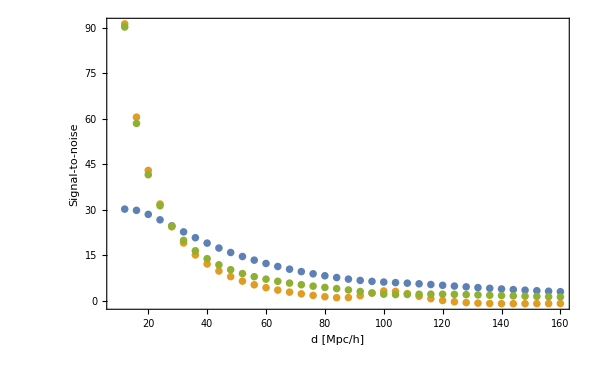

```mathematica
ListPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Fisher Analysis

## Fisher Analysis for I(z) (DIPOLE only)

## From 4 to 160 Mpc/h

```mathematica
dmax
```

160

```mathematica
nu1Lp4zbaretab=Table[nu1z0[d],{k,1,19},{d,4,dmax,4}];
```

```mathematica
ltot=Length[nu1Lp4zbaretab[[1,All]]]
```

40

```mathematica
Dimensions[var112popd4to160zSKA]
```

{12,40,40}

```mathematica
Invar11d4to160zSKA=Table[Inverse[var112popd4to160zSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
FisherDipoleLp4d4to160zSKA=Table[Sum[nu1Lp4zbaretab[[k,i]]Invar11d4to160zSKA[[k,i,j]] nu1Lp4zbaretab[[k,j]],{i,1,ltot},{j,1,ltot}],{k,1,ktot}]
```

{41.8911,74.9761,91.0485,91.9129,78.8979,62.1324,46.3455,33.3657,23.1761,15.5033,10.0832,6.34622}

```mathematica
Length[FisherDipoleLp4d4to160zSKA]
```

12

```mathematica
Length[bBzSKA]
```

19

```mathematica
FisherMatrixDipoleLp4d4to160zSKA=Table[(3/2)^2(bBtildezSKA[[k]]-bFtildezSKA[[k]])^2(HzSKA[[k]]^2/Sigma8z0^4),{k,1,ktot}]*FisherDipoleLp4d4to160zSKA
```

{103.877,157.961,166.124,147.618,113.094,80.4273,54.7187,36.2376,23.3228,14.5462,8.86815,5.25629}

```mathematica
ErrorDipoleLp4d4to160zSKA=1/Sqrt[FisherMatrixDipoleLp4d4to160zSKA]
```

{0.0981159,0.0795656,0.077586,0.0823057,0.0940329,0.111506,0.135186,0.166119,0.207066,0.262196,0.335802,0.436175}

## From 12 to 160 Mpc/h

```mathematica
nu1Lp4zbaretabd12to172=Table[nu1z0[d],{k,1,19},{d,12,dmax,4}];
```

```mathematica
ltot=Length[nu1Lp4zbaretabd12to172[[1,All]]]
```

38

```mathematica
dtot
```

40

```mathematica
var112popd12to160zSKA=Table[var112popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,3,dtot},{j,3,dtot}];
Invar11d12to160zSKA=Table[Inverse[var112popd12to160zSKA[[k,All,All]]],{k,1,ktot}];
Dimensions[Invar11d12to160zSKA]
```

{12,38,38}

```mathematica
FisherDipoleLp4d12to160zSKA=Table[Sum[nu1Lp4zbaretabd12to172[[k,i]] Invar11d12to160zSKA[[k,i,j]] nu1Lp4zbaretabd12to172[[k,j]],{i,1,ltot},{j,1,ltot}],{k,1,ktot}]
```

```mathematica
FisherMatrixDipoleLp4d12to160zSKA=Table[(3/2)^2(bBtildezSKA[[k]]-bFtildezSKA[[k]])^2(HzSKA[[k]]^2/Sigma8z0^4),{k,1,ktot}] FisherDipoleLp4d12to160zSKA
```

{78.5291,127.434,139.149,126.861,98.3169,70.2714,47.9953,31.926,20.6617,12.9753,7.97423,4.76939}

```mathematica
ErrorDipoleLp4d12to160zSKA=1/Sqrt[FisherMatrixDipoleLp4d12to160zSKA]
```

{0.112846,0.0885845,0.0847734,0.0887844,0.100852,0.119292,0.144345,0.176982,0.219997,0.277614,0.354124,0.457898}

## From 20 to 160 Mpc/h

```mathematica
nu1Lp4zbaretabd20to172=Table[nu1z0[d],{k,1,19},{d,20,dmax,4}];
```

```mathematica
ltot=Length[nu1Lp4zbaretabd20to172[[1,All]]]
```

36

```mathematica
var112popd20to160zSKA=Table[var112popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,5,dtot},{j,5,dtot}];
Invar11d20to160zSKA=Table[Inverse[var112popd20to160zSKA[[k,All,All]]],{k,1,ktot}];
Dimensions[Invar11d20to160zSKA]
```

{12,36,36}

```mathematica
FisherDipoleLp4d20to160zSKA=Table[Sum[nu1Lp4zbaretabd20to172[[k,i]] Invar11d20to160zSKA[[k,i,j]] nu1Lp4zbaretabd20to172[[k,j]],{i,1,ltot},{j,1,ltot}],{k,1,ktot}]
```

{22.294,46.4069,61.5161,65.8764,57.9849,46.0871,34.5714,25.0352,17.5165,11.8264,7.77871,4.96139}

```mathematica
FisherMatrixDipoleLp4d20to160zSKA=Table[(3/2)^2(bBtildezSKA[[k]]-bFtildezSKA[[k]])^2(HzSKA[[k]]^2/Sigma8z0^4),{k,1,ktot}]FisherDipoleLp4d20to160zSKA
```

{55.2823,97.7708,112.24,105.802,83.117,59.6575,40.8174,27.1901,17.6274,11.0962,6.84137,4.10929}

```mathematica
ErrorDipoleLp4d20to160zSKA=1/Sqrt[FisherMatrixDipoleLp4d20to160zSKA]
```

{0.134495,0.101134,0.0943899,0.0972194,0.109687,0.129469,0.156523,0.191776,0.23818,0.300201,0.382321,0.493306}

## From 32 to 160 Mpc/h

```mathematica
nu1Lp4zbaretabd32to172=Table[nu1z0[d],{k,1,19},{d,32,dmax,4}];
```

```mathematica
ltot=Length[nu1Lp4zbaretabd32to172[[1,All]]]
```

33

```mathematica
var112popd32to160zSKA=Table[var112popd4to160zSKA[[k,i,j]],{k,1,ktot},{i,8,dtot},{j,8,dtot}];
Invar11d32to160zSKA=Table[Inverse[var112popd32to160zSKA[[k,All,All]]],{k,1,ktot}];
Dimensions[Invar11d32to160zSKA]
```

{12,33,33}

```mathematica
FisherDipoleLp4d32to160zSKA=Table[Sum[nu1Lp4zbaretabd32to172[[k,i]] Invar11d32to160zSKA[[k,i,j]] nu1Lp4zbaretabd32to172[[k,j]],{i,1,ltot},{j,1,ltot}],{k,1,ktot}]
```

{12.7692,30.3498,43.765,49.6493,44.7191,35.7776,26.8933,19.4968,13.6565,9.23392,6.08598,3.89277}

```mathematica
FisherMatrixDipoleLp4d32to160zSKA=Table[(3/2)^2(bBtildezSKA[[k]]-bFtildezSKA[[k]])^2(HzSKA[[k]]^2/Sigma8z0^4),{k,1,ktot}]*FisherDipoleLp4d32to160zSKA
```

{31.6638,63.9415,79.8523,79.7401,64.1014,46.3124,31.752,21.1749,13.743,8.66383,5.35261,3.2242}

```mathematica
ErrorDipoleLp4d32to160zSKA=1/Sqrt[FisherMatrixDipoleLp4d32to160zSKA]
```

{0.177713,0.125057,0.111907,0.111985,0.124901,0.146944,0.177466,0.217315,0.269749,0.339739,0.432232,0.556915}

## Full Fisher Matrix

## Definitions

```mathematica
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Fisher Coefficient

### DIPOLE

```mathematica
coeffdDIPdI=(3/2)(bBtildezSKA-bFtildezSKA)HzSKA/Sigma8z0^2
```

{1.57471,1.45149,1.35077,1.26731,1.19726,1.13774,1.08659,1.04215,1.00316,0.968639,0.937816,0.910085,0.884962,0.862058,0.841059,0.821707,0.803789,0.78713,0.77158}

```mathematica
coeffdDIPdG=(HzSKA /Sigma8z0^2)(-(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA HzSKA))-(bBtildezSKA βFzSKA - bFtildezSKA βBzSKA)+(6/5) (βBzSKA-βFzSKA)GtildezSKA)
```

{22.2072,14.9754,10.5719,6.48156,3.80275,2.20478,1.26227,0.619034,0.216581,0.0374198,0.0224434,0.110588,0.230489,0.361694,0.49615,0.638013,0.793732,0.972027,1.17021}

```mathematica
coeffdDIPdGδznext= 2(1+zSKA)HzSKA (bBtildezSKA-bFtildezSKA)/(3 Δz Sigma8z0^2)
```

{8.0485,8.06382,8.10459,8.16709,8.24777,8.34342,8.45122,8.56878,8.69406,8.82538,8.96135,9.10085,9.24293,9.38686,9.532,9.67788,9.82409,9.97031,10.1163}

```mathematica
coeffdDIPdGδzprev=-coeffdDIPdGδznext;
```

```mathematica
coeffdDIPdG2δzprev=(1+zSKA)HzSKA (bBtildezSKA-bFtildezSKA)/(12 Δz Sigma8z0^2)
```

{1.00606,1.00798,1.01307,1.02089,1.03097,1.04293,1.0564,1.0711,1.08676,1.10317,1.12017,1.13761,1.15537,1.17336,1.1915,1.20974,1.22801,1.24629,1.26453}

```mathematica
coeffdDIPdG2δznext=-coeffdDIPdG2δzprev;
```

```mathematica
coeffdDIPdbB=(HzSKA/Sigma8z0^2)(-(1-(2/(rH0zSKA  HzSKA))+βFzSKA)GtildezSKA - dGtildezSKA/(H0 HzSKA)+(3/2)IhatzSKA)
```

{10.1237,6.4024,4.3887,2.81785,1.79026,1.16501,0.800412,0.578526,0.461828,0.429058,0.455106,0.520547,0.606556,0.706923,0.817887,0.938579,1.06861,1.20798,1.35422}

```mathematica
coeffdDIPdbF=(HzSKA/Sigma8z0^2)((1-(2/(rH0zSKA  HzSKA))+βBzSKA)GtildezSKA + dGtildezSKA/(H0 HzSKA)-(3/2)IhatzSKA)
```

{-5.10487,-1.95656,-0.839712,-0.531051,-0.379205,-0.290757,-0.258999,-0.283654,-0.335398,-0.394093,-0.456078,-0.525634,-0.60933,-0.707468,-0.81799,-0.93813,-1.06535,-1.1974,-1.33273}

### MONOPOLE BRIGHT

```mathematica
coeffdMONOBdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdMONOBdG=(1/Sigma8z0^2)((2/3)bBtildezSKA+(2/5) GtildezSKA)
```

{1.11122,1.11109,1.10896,1.10578,1.10234,1.09934,1.09733,1.09673,1.09789,1.10106,1.10644,1.1142,1.12447,1.13735,1.15296,1.1714,1.19275,1.21714,1.24466}

```mathematica
coeffdMONOBdbB=(1/Sigma8z0^2)(2 bBtildezSKA+2 GtildezSKA/3)
```

{2.97003,2.96017,2.94924,2.93908,2.93128,2.92711,2.92758,2.93346,2.94537,2.96377,2.98903,3.02146,3.06134,3.10891,3.16442,3.22813,3.30032,3.38128,3.47134}

```mathematica
coeffdMONOBdbF=Table[0,{i,zSKA}];
```

### MONOPOLE FAINT

```mathematica
coeffdMONOFdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdMONOFdG=(1/Sigma8z0^2)((2/3)bFtildezSKA+(2/5) GtildezSKA)
```

{0.364597,0.402896,0.436914,0.467513,0.495527,0.521719,0.546758,0.571214,0.595573,0.620241,0.645563,0.671834,0.699311,0.728222,0.758776,0.791167,0.82558,0.862198,0.901201}

```mathematica
coeffdMONOFdbB=Table[0,{i,zSKA}];
```

```mathematica
coeffdMONOFdbF=(1/Sigma8z0^2)(2 bFtildezSKA+2 GtildezSKA/3)
```

{0.730151,0.835593,0.93309,1.02429,1.11083,1.19424,1.27586,1.35691,1.43843,1.52132,1.6064,1.69437,1.78587,1.88151,1.98185,2.08744,2.19879,2.31646,2.44098}

### MONOPOLE 2 POP

```mathematica
coeffdMONO2popdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdMONO2popdG=(1/Sigma8z0^2)((1/3)(bBtildezSKA+bFtildezSKA)+(2/5) GtildezSKA)
```

{0.737911,0.756992,0.772939,0.786645,0.798935,0.810531,0.822043,0.833973,0.84673,0.860648,0.876002,0.893017,0.911889,0.932788,0.95587,0.981282,1.00917,1.03967,1.07293}

```mathematica
coeffdMONO2popdbB=(1/Sigma8z0^2)(bFtildezSKA+GtildezSKA/3)
```

{0.365076,0.417797,0.466545,0.512146,0.555417,0.597118,0.637931,0.678455,0.719213,0.760661,0.803199,0.847183,0.892936,0.940756,0.990926,1.04372,1.0994,1.15823,1.22049}

```mathematica
coeffdMONO2popdbF=(1/Sigma8z0^2)(bBtildezSKA+GtildezSKA/3)
```

{1.48502,1.48009,1.47462,1.46954,1.46564,1.46355,1.46379,1.46673,1.47269,1.48188,1.49452,1.51073,1.53067,1.55445,1.58221,1.61406,1.65016,1.69064,1.73567}

### QUADRUPOLE BRIGHT

```mathematica
coeffdQUADBdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdQUADBdG=-(1/Sigma8z0^2)(4 bBtildezSKA/3+8 GtildezSKA/7)
```

{-2.45622,-2.46202,-2.4607,-2.45471,-2.44624,-2.43714,-2.42892,-2.42279,-2.41968,-2.4203,-2.42521,-2.43484,-2.44954,-2.46959,-2.49524,-2.5267,-2.56419,-2.60793,-2.65815}

```mathematica
coeffdQUADBdbB=-4 GtildezSKA/(3 Sigma8z0^2)
```

{-0.909102,-0.932736,-0.944133,-0.945616,-0.939368,-0.927304,-0.911027,-0.891831,-0.870729,-0.848498,-0.825725,-0.802839,-0.780153,-0.757886,-0.736189,-0.715163,-0.694866,-0.67533,-0.656569}

```mathematica
coeffdQUADBdbF=Table[0,{i,zSKA}];
```

### QUADRUPOLE FAINT

```mathematica
coeffdQUADFdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdQUADFdG=-(1/Sigma8z0^2)(4 bFtildezSKA/3+8 GtildezSKA/7)
```

{-0.962963,-1.04564,-1.11661,-1.17818,-1.23261,-1.28189,-1.32778,-1.37176,-1.41505,-1.45867,-1.50345,-1.55011,-1.59923,-1.65133,-1.70686,-1.76623,-1.82984,-1.89805,-1.97123}

```mathematica
coeffdQUADFdbB=Table[0,{i,zSKA}];
```

```mathematica
coeffdQUADFdbF=-4 GtildezSKA/(3  Sigma8z0^2)
```

{-0.909102,-0.932736,-0.944133,-0.945616,-0.939368,-0.927304,-0.911027,-0.891831,-0.870729,-0.848498,-0.825725,-0.802839,-0.780153,-0.757886,-0.736189,-0.715163,-0.694866,-0.67533,-0.656569}

### QUADRUPOLE 2 POP

```mathematica
coeffdQUAD2popdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdQUAD2popdG=-(1/Sigma8z0^2)(2 (bBtildezSKA+bFtildezSKA)/3+8 GtildezSKA/7)
```

{-1.70959,-1.75383,-1.78865,-1.81645,-1.83942,-1.85951,-1.87835,-1.89727,-1.91736,-1.93948,-1.96433,-1.99248,-2.02439,-2.06046,-2.10105,-2.14646,-2.19701,-2.25299,-2.31469}

```mathematica
coeffdQUAD2popdbB=-2 GtildezSKA/(3  Sigma8z0^2)
```

{-0.454551,-0.466368,-0.472067,-0.472808,-0.469684,-0.463652,-0.455514,-0.445915,-0.435364,-0.424249,-0.412862,-0.401419,-0.390076,-0.378943,-0.368095,-0.357581,-0.347433,-0.337665,-0.328284}

```mathematica
coeffdQUAD2popdbF=-2 GtildezSKA/(3  Sigma8z0^2)
```

{-0.454551,-0.466368,-0.472067,-0.472808,-0.469684,-0.463652,-0.455514,-0.445915,-0.435364,-0.424249,-0.412862,-0.401419,-0.390076,-0.378943,-0.368095,-0.357581,-0.347433,-0.337665,-0.328284}

### HEXADECAPOLE

```mathematica
coeffdHEXAdI=Table[0,{i,zSKA}];
```

```mathematica
coeffdHEXAdG=16 GtildezSKA/(35  Sigma8z0^2)
```

{0.311692,0.319795,0.323703,0.324211,0.322069,0.317933,0.312352,0.305771,0.298536,0.290914,0.283106,0.275259,0.267481,0.259847,0.252408,0.245199,0.23824,0.231542,0.225109}

```mathematica
coeffdHEXAdbB=Table[0,{i,zSKA}];
```

```mathematica
coeffdHEXAdbF=Table[0,{i,zSKA}];
```

### Fisher Imputs

#### dSignaldI[z] (from z3 to z17)

```mathematica
For[i=3, i≤ktot-2,i++,dSignaldI[i]=Join[
Table[0.,{j,ldist(i-3)}],Table[coeffdDIPdI[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-2)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdI[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdI[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdI[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdI[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdI[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdI[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdI[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]]]
```

```mathematica
Table[coeffdDIPdI[[3]] nu1Lp4zbaretab[[d]],{d,id,dtot}]
```

{0.000453386,0.000400218,0.000355199,0.000316777,0.000283746,0.000255169,0.000230293,0.000208525,0.000189373,0.000172436,0.000157375,0.000143905,0.000131799,0.000120922,0.00011132,0.000103271,0.0000970313,0.0000923346,0.0000883871,0.000084443,0.0000801843,0.0000756421,0.0000709837,0.0000663756,0.000061936,0.0000577359,0.0000538084,0.0000501627,0.000046794,0.0000436891,0.0000408307,0.0000381996,0.0000357759}

```mathematica
ktot-2
```

10

```mathematica
dSignaldI[3]
```

{0.000453386,0.000400218,0.000355199,0.000316777,0.000283746,0.000255169,0.000230293,0.000208525,0.000189373,0.000172436,0.000157375,0.000143905,0.000131799,0.000120922,0.00011132,0.000103271,0.0000970313,0.0000923346,0.0000883871,0.000084443,0.0000801843,0.0000756421,0.0000709837,0.0000663756,0.000061936,0.0000577359,0.0000538084,0.0000501627,0.000046794,0.0000436891,0.0000408307,0.0000381996,0.0000357759,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
dSignaldI[4]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000425373,0.00037549,0.000333253,0.000297204,0.000266215,0.000239403,0.000216065,0.000195641,0.000177673,0.000161782,0.000147652,0.000135014,0.000123656,0.000113451,0.000104442,0.0000968903,0.0000910362,0.0000866297,0.000082926,0.0000792257,0.00007523,0.0000709685,0.000066598,0.0000622745,0.0000581093,0.0000541687,0.0000504838,0.0000470634,0.0000439028,0.0000409898,0.000038308,0.0000358395,0.0000335655,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
dSignaldI[5]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000401861,0.000354735,0.000314833,0.000280777,0.0002515,0.00022617,0.000204122,0.000184827,0.000167852,0.00015284,0.00013949,0.000127551,0.000116821,0.00010718,0.0000986689,0.0000915347,0.0000860041,0.0000818412,0.0000783423,0.0000748465,0.0000710717,0.0000670457,0.0000629168,0.0000588323,0.0000548973,0.0000511745,0.0000476933,0.0000444619,0.0000414761,0.0000387241,0.0000361905,0.0000338584,0.0000317102,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length[%]
```

3036

```mathematica
Join[Table[coeffdDIPdI[[3]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-3-2)ldist}]]
```

{0.000453386,0.000400218,0.000355199,0.000316777,0.000283746,0.000255169,0.000230293,0.000208525,0.000189373,0.000172436,0.000157375,0.000143905,0.000131799,0.000120922,0.00011132,0.000103271,0.0000970313,0.0000923346,0.0000883871,0.000084443,0.0000801843,0.0000756421,0.0000709837,0.0000663756,0.000061936,0.0000577359,0.0000538084,0.0000501627,0.000046794,0.0000436891,0.0000408307,0.0000381996,0.0000357759,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length[%]
```

264

```mathematica
15*43
```

645

```mathematica
Length[dSignaldI[7]]
```

3036

#### dSignald/bB[z]

```mathematica
For[i=1,i≤ktot,i++,dSignaldbB[i]=Which[i≤2,Join[
Table[0.,{j,(ktot-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbB[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbB[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbB[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
2<i≤ktot-2,Join[
Table[0.,{j,ldist(i-3)}],Table[coeffdDIPdbB[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-2)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbB[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbB[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbB[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
ktot-2<i≤ktot,Join[
Table[0.,{j,(ktot-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbB[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbB[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbB[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbB[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbB[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]]]]
```

```mathematica
Table[Length[dSignaldbB[k]],{k,1,ktot}]
```

{3036,3036,3036,3036,3036,3036,3036,3036,3036,3036,3036,3036}

```mathematica
coeffdMONO2popdbB[[1]]mu0Lp4zbaretab[[id]]
```

0.0112426

```mathematica
Length[dSignaldbB[1]]
```

3036

```mathematica
(15+7*19)*ldist
```

4884

```mathematica
15ldist+19ldist
```

1122

```mathematica
zpos=5;
dmonoBtest=Table[dSignaldbB[zpos][[m]],{m,15*ldist+1+38*(zpos-1),15*ldist+38*zpos}]
Length[dmonoBtest]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

38

#### dSignal/dbF[z]

```mathematica
For[i=1,i≤ktot,i++,dSignaldbF[i]=Which[i≤2,Join[
Table[0.,{j,(ktot-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbF[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbF[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbF[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
2<i≤ktot-2,Join[
Table[0.,{j,ldist(i-3)}],Table[coeffdDIPdbF[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-2)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbF[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbF[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbF[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
ktot-2<i≤ktot,Join[
Table[0.,{j,(ktot-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdbF[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdbF[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdbF[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdbF[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdbF[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]]]]
```

```mathematica
Length[dSignaldbF[7]]
```

3036

#### dSignal/dG[z]

```mathematica
For[i=1,i≤ktot,i++,dSignaldG[i]=Which[i==1,Join[
Table[coeffdDIPdG2δzprev[[i+2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==2,Join[
Table[coeffdDIPdGδzprev[[i+1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG2δzprev[[i+2]]nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==3,Join[
Table[coeffdDIPdG[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδzprev[[i+1]]nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG2δzprev[[i+2]]nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==4,Join[
Table[coeffdDIPdGδznext[[i-1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδzprev[[i+1]]nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG2δzprev[[i+2]]nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i-4)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
4<i≤ktot-4,Join[Table[0.,{j,ldist(i-5)}],Table[coeffdDIPdG2δznext[[i-2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδznext[[i-1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδzprev[[i+1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG2δzprev[[i+2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-4-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==ktot-3,Join[Table[0.,{j,ldist(i-5)}],Table[coeffdDIPdG2δznext[[i-2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδznext[[i-1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdG[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδzprev[[i+1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==ktot-2,Join[
Table[0.,{j,ldist(i-5)}],Table[coeffdDIPdG2δznext[[i-2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδznext[[i-1]] nu1Lp4zbaretab[[d]],{d,id,dtot}], Table[coeffdDIPdG[[i]] nu1Lp4zbaretab[[d]],{d,id,dtot}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==ktot-1,Join[
Table[0.,{j,ldist(i-5)}],Table[coeffdDIPdG2δznext[[i-2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[coeffdDIPdGδznext[[i-1]] nu1Lp4zbaretab[[d]],{d,id,dtot}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]],
i==ktot,Join[
Table[0.,{j,ldist(i-5)}],Table[coeffdDIPdG2δznext[[i-2]] nu1Lp4zbaretab[[d]],{d,id,dtot}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOBdG[[i]]  mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONOFdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdMONO2popdG[[i]] mu0Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADBdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUADFdG[[i]] mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdQUAD2popdG[[i]]mu2Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}],
Table[0.,{j,ldist(i-1)}],Table[coeffdHEXAdG[[i]] mu4Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-i)ldist}]] ]]
```

```mathematica
Join[Table[coeffdDIPdG2δzprev[[3]] nu1Lp4zbaretab[[d]],{d,id,dtot}],Table[0.,{j,(ktot-7)ldist}]]
```

{0.000340039,0.000300163,0.0002664,0.000237583,0.000212809,0.000191377,0.00017272,0.000156394,0.00014203,0.000129327,0.000118031,0.000107929,0.0000988493,0.0000906915,0.0000834899,0.0000774532,0.0000727735,0.000069251,0.0000662903,0.0000633323,0.0000601382,0.0000567316,0.0000532378,0.0000497817,0.000046452,0.000043302,0.0000403563,0.000037622,0.0000350955,0.0000327669,0.0000306231,0.0000286497,0.0000268319,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Dimensions[dSignaldG[2]]
```

{3036}

## Fisher Matrix

### Building blocks

```mathematica
InvCovMatrixzSKA=Inverse[CovMatrixzSKA[[All,All]]];
```

```mathematica
SymmetricMatrixQ[CovMatrixzSKA]
```

True

```mathematica
CovMatrixzSKA-Transpose[CovMatrixzSKA]//MatrixForm;
```

```mathematica
SymmetricMatrixQ[InvCovMatrixzSKA]
```

True

```mathematica
Id=CovMatrixzSKA.InvCovMatrixzSKA;
```

```mathematica
Id[[Length[CovMatrixzSKA],Length[CovMatrixzSKA]]]
```

1.

```mathematica
Det[Id]
```

1.

```mathematica
InverseAccuracy=Table[Id[[i,i]],{i,1,Length[CovMatrixzSKA]}];
```

```mathematica
Sum[InverseAccuracy[[i]],{i,1,Length[CovMatrixzSKA]}]
```

3036.

```mathematica
Id[[4,54]]
```

0.

```mathematica
Length[CovMatrixzSKA]
```

3036

```mathematica
dSignaldIzSKA=Table[dSignaldI[i],{i,3,ktot-2}];
dSignaldGzSKA=Table[dSignaldG[i],{i,1,ktot}];
dSignaldbBzSKA=Table[dSignaldbB[i],{i,1,ktot}];
dSignaldbFzSKA=Table[dSignaldbF[i],{i,1,ktot}];
```

```mathematica
Dimensions[dSignaldIzSKA]
```

{8,3036}

```mathematica
dSignaldIzSKA[[1,All]]==dSignaldI[3]
```

True

```mathematica
FII=Table[dSignaldIzSKA[[i,All]].InvCovMatrixzSKA.dSignaldIzSKA[[j,All]],{i,1,ktot-4},{j,1,ktot-4}];
```

```mathematica
FIG=Table[dSignaldIzSKA[[i,All]].InvCovMatrixzSKA.dSignaldGzSKA[[j,All]],{i,1,ktot-4},{j,1,ktot}];
```

```mathematica
FGI=Table[dSignaldGzSKA[[i,All]].InvCovMatrixzSKA.dSignaldIzSKA[[j,All]],{i,1,ktot},{j,1,ktot-4}];
```

```mathematica
Transpose[FGI]==FIG
```

True

```mathematica
FGG=Table[dSignaldGzSKA[[i,All]].InvCovMatrixzSKA.dSignaldGzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbBbB=Table[dSignaldbBzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbBzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FIbB=Table[dSignaldIzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbBzSKA[[j,All]],{i,1,ktot-4},{j,1,ktot}];
```

```mathematica
FbBI=Table[dSignaldbBzSKA[[i,All]].InvCovMatrixzSKA.dSignaldIzSKA[[j,All]],{i,1,ktot},{j,1,ktot-4}];
Transpose[FIbB]==FbBI
```

True

```mathematica
FGbB=Table[dSignaldGzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbBzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbBG=Table[dSignaldbBzSKA[[i,All]].InvCovMatrixzSKA.dSignaldGzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
(*FbB1G1=Sum[dSignaldbBzSKA[[1,i]]InvCovMatrixzSKA[[i,j]]dSignaldGzSKA[[1,j]],{i,1,Length[dSignaldbB[1]]},{j,1,Length[dSignaldG[5]]}]
Sum[dSignaldGzSKA[[1,i]]InvCovMatrixzSKA[[i,j]]dSignaldbBzSKA[[1,j]],{i,1,Length[dSignaldbB[1]]},{j,1,Length[dSignaldG[5]]}]*)
```

```mathematica
FbBG[[1,1]]
FGbB[[1,1]]
```

-73457.

-73457.

```mathematica
FbBG==Transpose[FGbB]
```

False

```mathematica
FbFbF=Table[dSignaldbFzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbFzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FIbF=Table[dSignaldIzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbFzSKA[[j,All]],{i,1,ktot-4},{j,1,ktot}];
```

```mathematica
FbFI=Table[dSignaldbFzSKA[[i,All]].InvCovMatrixzSKA.dSignaldIzSKA[[j,All]],{i,1,ktot},{j,1,ktot-4}];
```

```mathematica
FbFI==Transpose[FIbF]
```

True

```mathematica
FGbF=Table[dSignaldGzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbFzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbFG=Table[dSignaldbFzSKA[[i,All]].InvCovMatrixzSKA.dSignaldGzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbFG==Transpose[FGbF]
```

False

```mathematica
FbBbF=Table[dSignaldbBzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbFzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbFbB=Table[dSignaldbFzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbBzSKA[[j,All]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbFbBbis=Table[dSignaldbBzSKA[[i,All]].InvCovMatrixzSKA.dSignaldbFzSKA[[j,All]],{j,1,ktot},{i,1,ktot}];
```

```mathematica
FbFbB==Transpose[FbBbF]
```

False

```mathematica
FbFbBbis==Transpose[FbBbF]
```

True

```mathematica
Join[FII,FGI,FbBI,FbFI]//MatrixForm;
```

```mathematica
FisherRow1=Transpose[Join[FII,FGI,FbBI,FbFI]];
FisherRow2=Transpose[Join[FIG,FGG,FbBG,FbFG]];
FisherRow3=Transpose[Join[FIbB,FGbB,FbBbB,FbFbB]];
FisherRow4=Transpose[Join[FIbF,FGbF,FbBbF,FbFbF]];
FisherMatrixzSKA=Transpose[Join[FisherRow1,FisherRow2,FisherRow3,FisherRow4]];
```

```mathematica
SymmetricMatrixQ[FisherMatrixzSKA]
```

True

```mathematica
(*Export["FisherzSKA_d12to160.txt",FisherMatrixzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]*)
```

```mathematica
Transpose[Join[FII,FGI]]==Transpose[ArrayFlatten[{{FII},{FGI}}]]
```

True

### Constraints on I and G only

```mathematica
Length[Join[FII,FGI]]
```

20

```mathematica
Length[Join[FIG,FGG]]
```

20

```mathematica
FisherMatrixIGzSKA=Table[FisherMatrixzSKA[[i,j]],{i,1,Length[Join[FII,FGI]]},{j,1,Length[Join[FII,FGI]]}];
```

```mathematica
FisherMatrixzSKA//MatrixForm;
```

```mathematica
FisherMatrixIGzSKA//MatrixForm;
```

```mathematica
Dimensions[FisherMatrixIGzSKA]
```

{20,20}

```mathematica
1/Sqrt[Diagonal[FisherMatrixIGzSKA]]
```

{0.111907,0.111985,0.124901,0.146944,0.177466,0.217315,0.269749,0.339739,0.00242858,0.00185725,0.00165811,0.00161703,0.00169579,0.00185089,0.00221546,0.00229722,0.00261665,0.00297053,0.00334298,0.00377247}

```mathematica
InverseFisherMatrixIGzSKA=Inverse[FisherMatrixIGzSKA[[All,All]]];
```

```mathematica
ErrorsIGzSKA=Table[Sqrt[InverseFisherMatrixIGzSKA[[i,i]]],{i,1,Length[InverseFisherMatrixIGzSKA]}]
```

{0.113675,0.113374,0.126206,0.148456,0.179013,0.219201,0.271764,0.341994,0.0024289,0.00186669,0.00167725,0.0016343,0.00171193,0.00186764,0.00223769,0.00231569,0.00263641,0.00298445,0.0033568,0.00377277}

### Constraints on G, bB and bF only

```mathematica
Length[FII]
```

8

```mathematica
Length[FisherMatrixzSKA]-Length[FII]
```

36

```mathematica
FisherMatrixGbBbFzSKA=Table[FisherMatrixzSKA[[i,j]],{i,Length[FII]+1,Length[FisherMatrixzSKA]},{j,Length[FII]+1,Length[FisherMatrixzSKA]}];
Dimensions[FisherMatrixGbBbFzSKA]
```

{36,36}

```mathematica
Diagonal[FisherMatrixGbBbFzSKA]
```

{169549.,289908.,363723.,382442.,347739.,291903.,203739.,189493.,146052.,113327.,89481.4,70266.5,73643.7,140437.,178827.,200265.,188601.,166469.,31693.1,149648.,115958.,89871.8,68325.,50595.1,1.0869×10^6,1.69471×10^6,1.7458×10^6,1.6107×10^6,1.27228×10^6,940178.,88113.3,611009.,395902.,256702.,162614.,100047.}

```mathematica
1/Sqrt[Diagonal[FisherMatrixGbBbFzSKA]]
```

{0.00242858,0.00185725,0.00165811,0.00161703,0.00169579,0.00185089,0.00221546,0.00229722,0.00261665,0.00297053,0.00334298,0.00377247,0.00368495,0.00266845,0.00236474,0.00223459,0.00230265,0.00245095,0.00561717,0.00258502,0.00293664,0.00333571,0.00382569,0.00444576,0.000959191,0.00076816,0.000756838,0.000787938,0.000886562,0.00103132,0.00336883,0.00127931,0.0015893,0.00197372,0.00247982,0.00316154}

```mathematica
InverseFisherMatrixGbBbFzSKA=Inverse[FisherMatrixGbBbFzSKA[[All,All]]];
```

```mathematica
ErrorsGbBbFzSKA=Table[Sqrt[InverseFisherMatrixGbBbFzSKA[[i,i]]],{i,1,Length[FisherMatrixGbBbFzSKA]}]
```

{0.00283413,0.00256955,0.00222685,0.00215165,0.00223233,0.00240766,0.00273573,0.00296614,0.00331461,0.00370496,0.00410697,0.00457907,0.+0.0131341 ⅈ,0.00648435,0.00574413,0.00539536,0.00523181,0.00512546,0.00578938,0.00507155,0.00515997,0.00533822,0.00561608,0.00603768,0.+0.00395759 ⅈ,0.0021134,0.00208884,0.00216128,0.00229422,0.00246104,0.00406664,0.00285478,0.0031464,0.00350533,0.00395766,0.00456118}

### Constraints on I, G and bB only

```mathematica
Length[FII]+Length[FGG]+Length[FbBbB]
```

32

```mathematica
FisherMatrixIGbBzSKA=Table[FisherMatrixzSKA[[i,j]],{i,1,Length[FisherMatrixzSKA]-Length[FbFbF]},{j,1,Length[FisherMatrixzSKA]-Length[FbFbF]}];
```

```mathematica
Dimensions[FisherMatrixIGbBzSKA]
```

{32,32}

```mathematica
Diagonal[FisherMatrixIGbBzSKA]
```

{79.8523,79.7401,64.1017,46.3124,31.752,21.175,13.743,8.66383,169549.,289908.,363723.,382442.,347739.,291903.,203739.,189493.,146052.,113327.,89481.4,70266.5,73643.7,140437.,178827.,200265.,188601.,166469.,31693.1,149648.,115958.,89871.8,68325.,50595.1}

```mathematica
1/Sqrt[Diagonal[FisherMatrixIGbBzSKA]]
```

{0.111907,0.111985,0.124901,0.146944,0.177466,0.217315,0.269749,0.339739,0.00242858,0.00185725,0.00165811,0.00161703,0.00169579,0.00185089,0.00221546,0.00229722,0.00261665,0.00297053,0.00334298,0.00377247,0.00368495,0.00266845,0.00236474,0.00223459,0.00230265,0.00245095,0.00561717,0.00258502,0.00293664,0.00333571,0.00382569,0.00444576}

```mathematica
InverseFisherMatrixIGbBzSKA=Inverse[FisherMatrixIGbBzSKA[[All,All]]];
```

```mathematica
ErrorsIGbBzSKA=Table[Sqrt[InverseFisherMatrixIGbBzSKA[[i,i]]],{i,1,Length[FisherMatrixIGbBzSKA]}]
```

{0.1151,0.113986,0.126508,0.148626,0.17915,0.21926,0.271804,0.342017,0.00322358,0.00223733,0.00190191,0.001799,0.00183258,0.00195318,0.00228989,0.00237016,0.00265426,0.00298509,0.00336521,0.00381861,0.00489057,0.00319828,0.00268784,0.0024622,0.00246587,0.00256358,0.00574977,0.00264588,0.00295655,0.00333646,0.00383528,0.00449977}

## Tests

```mathematica
Cov0B0cross2B2crosszSKA={};
CovminiRow[1]=Transpose[Join[CovBlockMonopoleBright,CovBlockMonopoleBrightMonopoleBF,CovBlockMonopoleBrightQuadrupoleBright,CovBlockMonopoleBrightQuadrupoleBF]];
CovminiRow[2]=Transpose[Join[CovBlockMonopoleBrightMonopoleBF,CovBlockMonopoleBF,CovBlockMonopoleBFQuadrupoleBright,CovBlockMonopoleBFQuadrupoleBF]];
CovminiRow[3]=Transpose[Join[CovBlockQuadrupoleBrightMonopoleBright,CovBlockQuadrupoleBrightMonopoleBF,CovBlockQuadrupoleBright,CovBlockQuadrupoleBrightQuadrupoleBF]];
CovminiRow[4]=Transpose[Join[CovBlockQuadrupoleBFMonopoleBright,CovBlockQuadrupoleBFMonopoleBF,CovBlockQuadrupoleBrightQuadrupoleBF,CovBlockQuadrupoleBF]];
```

```mathematica
Table[Dimensions[CovminiRow[i]],{i,1,4}]
```

{{396,1584},{396,1584},{396,1584},{396,1584}}

```mathematica
For[j=1,j≤4,j++,
Cov0B0cross2B2crosszSKA=Join[Cov0B0cross2B2crosszSKA,CovminiRow[j]]]
```

```mathematica
Dimensions[Cov0B0cross2B2crosszSKA]
```

{1584,1584}

```mathematica
invCov0B0cross2B2crosszSKA=Inverse[Cov0B0cross2B2crosszSKA];
```

```mathematica
dSignaldBmini=Join[Flatten[Table[coeffdMONOBdbB[[k]]mu0z0[4 d],{k,1,ktot},{d,id,dtot}]],Flatten[Table[coeffdMONO2popdbB[[k]]mu0z0[4 d],{k,1,ktot},{d,id,dtot}]],Flatten[Table[coeffdQUADBdbB[[k]]mu2z0[4 d],{k,1,ktot},{d,id,dtot}]],Flatten[Table[coeffdQUAD2popdbB[[k]]mu2z0[4 d],{k,1,ktot},{d,id,dtot}]]];
```

```mathematica
mu0z0[12]
```

0.261647

```mathematica
mu0Lp4zbaretab[[3]]
```

0.261647

```mathematica
Table[coeffdMONOBdbB[[2]]  mu0Lp4zbaretab[[d]],{d,id,dtot}]
```

{0.0911595,0.0659009,0.0485433,0.0361994,0.0273117,0.02076,0.0158796,0.0121804,0.00934388,0.00712711,0.00536026,0.00392906,0.0027911,0.00205099,0.00202618,0.00299323,0.00446789,0.00527965,0.00483734,0.00356431,0.00214176,0.000962406,0.000122908,-0.000422235,-0.00075063,-0.000932679,-0.00102069,-0.00104978,-0.00104218,-0.0010132,-0.00097308,-0.000928287,-0.000882992}

```mathematica
Dimensions[dSignaldBmini]
```

{1584}

```mathematica
FbBmini=dSignaldBmini.invCov0B0cross2B2crosszSKA.dSignaldBmini
```

803873.

```mathematica
For[k=1,k<=ktot,++k,dSignaldBminiz[k]=Join[Table[0.,{j,ldist(k-1)}],Table[coeffdMONOBdbB[[k]]mu0z0[4 d],{d,id,dtot}],
Table[0.,{j,(ktot-k)ldist}],Table[0.,{j,ldist(k-1)}],Table[coeffdMONO2popdbB[[k]]mu0z0[4 d],{d,id,dtot}],
Table[0.,{j,(ktot-k)ldist}],Table[0.,{j,ldist(k-1)}],Table[coeffdQUADBdbB[[k]]mu2z0[4 d],{d,id,dtot}],
Table[0.,{j,(ktot-k)ldist}],Table[0.,{j,ldist(k-1)}],Table[coeffdQUAD2popdbB[[k]]mu2z0[4 d],{d,id,dtot}],Table[0.,{j,(ktot-k)ldist}]]]
```

```mathematica
1/Sqrt[FbBmini]
```

0.00111534

```mathematica
dSignaldBminizSKA[[1]]
```

{0.777101,0.451373,0.283556,0.18781,0.129112,0.0914631,0.0661204,0.0487049,0.03632,0.0274027,0.0208291,0.0159324,0.012221,0.00937499,0.00715084,0.00537811,0.00394214,0.00280039,0.00205782,0.00203293,0.0030032,0.00448277,0.00529723,0.00485345,0.00357618,0.0021489,0.000965611,0.000123317,-0.000423642,-0.00075313,-0.000935785,-0.00102409,-0.00105327,-0.00104565,-0.00101657,-0.000976321,-0.000931379,-0.000885933,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0955211,0.0554827,0.0348547,0.0230856,0.0158705,0.0112426,0.0081275,0.0059868,0.00446445,0.00336833,0.00256031,0.00195841,0.0015022,0.00115237,0.00087898,0.000661076,0.000484568,0.000344224,0.000252947,0.000249887,0.000369153,0.000551022,0.000651134,0.000596585,0.000439584,0.000264142,0.000118693,0.0000151581,-0.0000520739,-0.0000925746,-0.000115026,-0.000125881,-0.000129468,-0.000128531,-0.000124957,-0.000120009,-0.000114485,-0.000108899,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.235398,-0.164047,-0.12065,-0.0920476,-0.0721856,-0.0577647,-0.0470533,-0.0388424,-0.0324612,-0.0273938,-0.023327,-0.0200155,-0.017296,-0.015041,-0.0131606,-0.0115843,-0.0102546,-0.00911508,-0.0080837,-0.00703478,-0.0058753,-0.00474589,-0.00396758,-0.0036587,-0.00363808,-0.00367577,-0.00365152,-0.00354279,-0.00336977,-0.00315942,-0.00293398,-0.00270833,-0.00249122,-0.00228704,-0.00209799,-0.00192482,-0.00176728,-0.00162463,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.117699,-0.0820236,-0.0603251,-0.0460238,-0.0360928,-0.0288823,-0.0235267,-0.0194212,-0.0162306,-0.0136969,-0.0116635,-0.0100077,-0.00864799,-0.00752048,-0.00658029,-0.00579213,-0.00512732,-0.00455754,-0.00404185,-0.00351739,-0.00293765,-0.00237294,-0.00198379,-0.00182935,-0.00181904,-0.00183789,-0.00182576,-0.0017714,-0.00168488,-0.00157971,-0.00146699,-0.00135417,-0.00124561,-0.00114352,-0.001049,-0.000962411,-0.000883642,-0.000812313,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Dimensions[dSignaldBminiz[1]]
```

{1584}

```mathematica
dSignaldBminizSKA=Table[dSignaldBminiz[k],{k,1,ktot}];
```

```mathematica
Dimensions[dSignaldBminizSKA]
```

{12,1584}

```mathematica
FbBminizSKA=Table[dSignaldBminizSKA[[i]].invCov0B0cross2B2crosszSKA.dSignaldBminizSKA[[j]],{i,1,ktot},{j,1,ktot}];
```

```mathematica
FbBminizSKA[[7,7]]
```

134683.

```mathematica
FbBminizSKA//MatrixForm
```

(9512.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 25219.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 47210.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 71735. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -32547.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 131065. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 134683. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 125774. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 105792. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 80265.7 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 31883.2 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 73281.6)

## Errors in SKA

```mathematica
1/Sqrt[Diagonal[FisherMatrixzSKA]]
```

{0.111907,0.111985,0.124901,0.146944,0.177466,0.217315,0.269749,0.339739,0.00242858,0.00185725,0.00165811,0.00161703,0.00169579,0.00185089,0.00221546,0.00229722,0.00261665,0.00297053,0.00334298,0.00377247,0.00368495,0.00266845,0.00236474,0.00223459,0.00230265,0.00245095,0.00561717,0.00258502,0.00293664,0.00333571,0.00382569,0.00444576,0.000959191,0.00076816,0.000756838,0.000787938,0.000886562,0.00103132,0.00336883,0.00127931,0.0015893,0.00197372,0.00247982,0.00316154}

```mathematica
Det[FisherMatrixzSKA]
```

-4.75831×10^195

```mathematica
InverseFisherMatrixzSKA=Inverse[FisherMatrixzSKA[[All,All]]];
```

```mathematica
ErrorszSKA=Table[Sqrt[InverseFisherMatrixzSKA[[i,i]]],{i,1,Length[InverseFisherMatrixzSKA]}]
```

{0.115752,0.114643,0.127226,0.14941,0.180118,0.220304,0.272985,0.343242,0.00283461,0.00259346,0.00225921,0.00218582,0.00226643,0.00244339,0.00277711,0.00300558,0.00335453,0.00373179,0.00413245,0.00457959,0.+0.0131325 ⅈ,0.00648687,0.00578197,0.00541521,0.00524602,0.00513837,0.00579548,0.00508435,0.0051724,0.00534631,0.00562352,0.00603783,0.+0.0039574 ⅈ,0.00211838,0.00209653,0.00217162,0.0023059,0.00247392,0.00408621,0.00286896,0.00316042,0.00351441,0.00396588,0.00456134}

```mathematica
Table[ErrorDipoleLp4d4to160zSKA[[j]],{j,3,ktot-2}]
```

{0.077586,0.0823057,0.0940329,0.111506,0.135186,0.166119,0.207066,0.262196}

```mathematica
Table[ErrorDipoleLp4d12to160zSKA[[j]],{j,3,ktot-2}]
```

{0.0847734,0.0887844,0.100852,0.119292,0.144345,0.176982,0.219997,0.277614}

```mathematica
Table[ErrorDipoleLp4d20to160zSKA[[j]],{j,3,ktot-2}]
```

{0.0943899,0.0972194,0.109687,0.129469,0.156523,0.191776,0.23818,0.300201}

```mathematica
Table[ErrorDipoleLp4d32to160zSKA[[j]],{j,3,ktot-2}]
```

{0.111907,0.111985,0.124901,0.146944,0.177466,0.217315,0.269749,0.339739}

```mathematica
Abs[Table[ErrorszSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.320564,0.303743,0.3275,0.378274,0.452866,0.554259,0.691321,0.879018}

```mathematica
Length[ErrorDipoleLp4d32to160zSKA]
```

12

```mathematica
Length[IhatzSKA]
```

19

```mathematica
ktot
```

12

```mathematica
Table[ErrorDipoleLp4d32to160zSKA[[j]]/IhatzSKA[[j]],{j,3,ktot-2}]
```

{0.309915,0.296702,0.321516,0.372031,0.446197,0.546737,0.683126,0.870045}

# Results

Summary of the results:
	Absolute erros for all the parameters at each redshift bin.
	Relative error for the gravitational potential at each redshift bin.

Results for d = (12, 160) Mpc/h for redshifts bins of  size=0.1, from z = (0.15, 1.25)

```mathematica
Errorsd12to160zSKA={0.08519257776331966,0.08909324302018695,0.10113767679523926,0.11959036616836678,0.14466668886545983,0.1773309526591856,0.22037628967502584,0.27802721899094607,0.0009125733573320061,0.0007029060318818392,0.0006576192780521648,0.0006743062688653497,0.0007234668572833914,0.0007862932676059233,0.0008584949413596334,0.0009376513628535041,0.0010287831561059837,0.0011416680304129378,0.0012868367704190452,0.0014843198742481314,0.002058500215353694,0.001480091025603028,0.001255308124047803,0.0011391296348445335,0.0010736528318488385,0.0010388498170931318,0.0010299348148050545,0.0010437024875587125,0.0010816480016998626,0.0011489518548598511,0.0012516038598844698,0.001403482979588947,0.0006151027128412879,0.000500330709372151,0.00047561316808369643,0.00048242565407085507,0.000507652750902284,0.0005442987667413245,0.0005925041142232066,0.0006531819503791654,0.0007317424026595993,0.0008373759688924904,0.0009803039545346426,0.0011799260041862806}
```

{0.0851926,0.0890932,0.101138,0.11959,0.144667,0.177331,0.220376,0.278027,0.000912573,0.000702906,0.000657619,0.000674306,0.000723467,0.000786293,0.000858495,0.000937651,0.00102878,0.00114167,0.00128684,0.00148432,0.0020585,0.00148009,0.00125531,0.00113913,0.00107365,0.00103885,0.00102993,0.0010437,0.00108165,0.00114895,0.0012516,0.00140348,0.000615103,0.000500331,0.000475613,0.000482426,0.000507653,0.000544299,0.000592504,0.000653182,0.000731742,0.000837376,0.000980304,0.00117993}

```mathematica
Length[Errorsd12to160zSKA]
```

44

```mathematica
RelativeErrd12to160zSKA=Abs[Table[Errorsd12to160zSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.235932,0.23605,0.260345,0.302778,0.363731,0.446143,0.558093,0.712006}

Results for d = (20, 160) Mpc/h for redshifts bins of size=0.1, from z = (0.15, 1.25)

```mathematica
Errorsd20to160zSKA={0.09438992104692161,0.09721940908162344,0.10968701192328745,0.12946948431781247,0.15652270609543972,0.19177640151574665,0.23818064912498613,0.3002013435111759,0.0009360811815394402,0.0008274487416342931,0.000828936630556,0.0008743367925575278,0.0009560729588138008,0.001062479275140306,0.0011916702645201008,0.0013363539334355498,0.0014953264998848453,0.0016737351473677794,0.001874386229585479,0.002121748122146401,0.0011325518160741706,0.0009234143446401476,0.0009069693452110301,0.0009473417957806003,0.0010157438776713975,0.0010916060949643228,0.0011849574522386672,0.00129997836422276,0.0014465557200618756,0.0016359406352396172,0.0018750720445672852,0.0021834809518029787,0.00030849101466883,0.00028276277155177455,0.00030540542547496615,0.0003476486113890123,0.00040608273500767397,0.00047627294356973344,0.0005650394819011599,0.0006778229864723013,0.0008254645541771514,0.0010230240931010035,0.0012856470822900155,0.0016418836962851615}
```

{0.0943899,0.0972194,0.109687,0.129469,0.156523,0.191776,0.238181,0.300201,0.000936081,0.000827449,0.000828937,0.000874337,0.000956073,0.00106248,0.00119167,0.00133635,0.00149533,0.00167374,0.00187439,0.00212175,0.00113255,0.000923414,0.000906969,0.000947342,0.00101574,0.00109161,0.00118496,0.00129998,0.00144656,0.00163594,0.00187507,0.00218348,0.000308491,0.000282763,0.000305405,0.000347649,0.000406083,0.000476273,0.000565039,0.000677823,0.000825465,0.00102302,0.00128565,0.00164188}

```mathematica
Errorsd20to120zSKA={0.08309896310880956,0.093652982364287,0.11005467369962392,0.13137212223088868,0.1593564086156337,0.19542484219642278,0.24281591695745566,0.30614229156206657,0.0016340628017633317,0.0012160788869831718,0.0011011642332532676,0.0011012850095956576,0.001060095272563389,0.0012907236720806734,0.0014360640471583928,0.0016002172053823636,0.0017717636552939974,0.0019775388076826656,0.002182724290192066,0.0024772916208786783,0.004089497531757767,0.002972519319070589,0.002595692342771671,0.0023203756846586023,0.0021207665832654265,0.002148600715884614,0.00213101512950441,0.002152757867977969,0.002215849373177975,0.0023267034427521724,0.0024917430142203448,0.0027335177463897902,0.0011625831915426125,0.0009606989657230769,0.000938808760004075,0.0009403498694676767,0.0009312550018358806,0.0010670628867988478,0.0011601764453150257,0.00127463319482743,0.0014162655809966682,0.0016004440760437248,0.0018371742466959744,0.002162428960979396}
```

{0.083099,0.093653,0.110055,0.131372,0.159356,0.195425,0.242816,0.306142,0.00163406,0.00121608,0.00110116,0.00110129,0.0010601,0.00129072,0.00143606,0.00160022,0.00177176,0.00197754,0.00218272,0.00247729,0.0040895,0.00297252,0.00259569,0.00232038,0.00212077,0.0021486,0.00213102,0.00215276,0.00221585,0.0023267,0.00249174,0.00273352,0.00116258,0.000960699,0.000938809,0.00094035,0.000931255,0.00106706,0.00116018,0.00127463,0.00141627,0.00160044,0.00183717,0.00216243}

```mathematica
RelativeErrd20to160zSKA=Abs[Table[Errorsd20to160zSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.261404,0.25758,0.282352,0.32779,0.393541,0.482486,0.603181,0.768793}

```mathematica
RelativeErrd20to120zSKA=Abs[Table[Errorsd20to120zSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.230134,0.248131,0.283299,0.332607,0.400665,0.491665,0.61492}

```mathematica
Abs[RelativeErrd20to160zSKA-RelativeErrd20to120zSKA]/RelativeErrd20to160zSKA
```

{0.0210854,0.021175,0.021978,0.0219676,0.0227032,0.0227547,0.0229316}

Results for d = (32, 160) Mpc/h for redshifts bins of 0.1 size from z = (0.15, 1.25)

```mathematica
Errorsd32to160zSKA={0.11575222717814487,0.11464303580066706,0.12722576134042435,0.1494098852147172,0.18011809170835408,0.22030449052983217,0.2729846539740011,0.3432424543875365,0.0028346055782475245,0.002593457800511075,0.0022592104575699778,0.0021858188041132165,0.0022664339689852393,0.002443388568698555,0.0027771120686623765,0.003005582542349204,0.0033545322141124486,0.003731793978428782,0.004132449098540728,0.004579594094527481,0.+0.013132478865777217 ⅈ,0.0064868660909402085,0.005781974039334315,0.0054152068863089,0.0052460201911567915,0.00513836869530297,0.00579548327029378,0.005084348857066574,0.005172397489021027,0.005346310910277511,0.005623521778231163,0.006037833172169047,0.+0.003957398093357298 ⅈ,0.0021183764240588353,0.0020965310648973713,0.0021716182622170603,0.002305902928644301,0.0024739158668445702,0.00408620521769298,0.0028689589817800735,0.0031604179915325848,0.003514407682353654,0.003965882387527673,0.004561340104082362}
```

{0.115752,0.114643,0.127226,0.14941,0.180118,0.220304,0.272985,0.343242,0.00283461,0.00259346,0.00225921,0.00218582,0.00226643,0.00244339,0.00277711,0.00300558,0.00335453,0.00373179,0.00413245,0.00457959,0.+0.0131325 ⅈ,0.00648687,0.00578197,0.00541521,0.00524602,0.00513837,0.00579548,0.00508435,0.0051724,0.00534631,0.00562352,0.00603783,0.+0.0039574 ⅈ,0.00211838,0.00209653,0.00217162,0.0023059,0.00247392,0.00408621,0.00286896,0.00316042,0.00351441,0.00396588,0.00456134}

```mathematica
RelativeErrd32to160zSKA=Abs[Table[Errorsd32to160zSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.320564,0.303743,0.3275,0.378274,0.452866,0.554259,0.691321,0.879018}

```mathematica
ErrorGd32to160zSKA=Table[Errorsd32to160zSKA[[k]],{k,9,20}]
```

{0.00283461,0.00259346,0.00225921,0.00218582,0.00226643,0.00244339,0.00277711,0.00300558,0.00335453,0.00373179,0.00413245,0.00457959}

```mathematica
GtildezSKA
```

{0.46404,0.476104,0.481921,0.482678,0.479489,0.473331,0.465023,0.455224,0.444453,0.433106,0.421481,0.409799,0.398219,0.386853,0.375779,0.365046,0.354686,0.344714,0.335137}

```mathematica
GtildezSKAincluded=Table[GtildezSKA[[k]],{k,1,12}]
```

{0.46404,0.476104,0.481921,0.482678,0.479489,0.473331,0.465023,0.455224,0.444453,0.433106,0.421481,0.409799}

```mathematica
Length[GtildezSKAincluded]==Length[ErrorGd32to160zSKA]
```

True

```mathematica
RelErrorGd32to160zSKA=Table[ErrorGd32to160zSKA[[k]]/GtildezSKAincluded[[k]],{k,3,ktot-2}]
```

{0.00468793,0.00452852,0.00472677,0.00516212,0.00597199,0.00660242,0.00754756,0.00861636}

Results for d = (20, 160) Mpc/h for redshifts bins of size=0.1, from z = (0.15, 1.25)
Comparison with neglecting Dipole CC contribution.

```mathematica
Errorsd20to160zSKA={0.08138296901901032,0.09171100460978723,0.10768790524675069,0.12854821998519692,0.1558188161499092,0.1910769392095209,0.23737257765793993,0.2992593701453131,0.0016284456695401467,0.0011869513602317287,0.0010632889714112844,0.0010404610933940435,0.0010993705639942245,0.001196191157796965,0.0013425975133838498,0.0014544438937038136,0.0016251023030906695,0.0018196695335012463,0.0020467517824864848,0.0023261404434040045,0.004068433367582823,0.0029316932523747526,0.0024949547032345892,0.0022429253270252903,0.0021294848028886324,0.002049195975946539,0.0020296999724786335,0.002020492705840641,0.0020813425261591236,0.0021933425763821335,0.002362611150660801,0.002608617263519316,0.0011713629454838163,0.0008781882607336347,0.0007668652965431867,0.0007034307003588119,0.000674764167234026,0.0006583720222605919,0.0006580138710761264,0.0006732745098241465,0.0007083896140175042,0.0007709479107249018,0.0008692900394199833,0.0010219621273649664}
```

{0.081383,0.091711,0.107688,0.128548,0.155819,0.191077,0.237373,0.299259,0.00162845,0.00118695,0.00106329,0.00104046,0.00109937,0.00119619,0.0013426,0.00145444,0.0016251,0.00181967,0.00204675,0.00232614,0.00406843,0.00293169,0.00249495,0.00224293,0.00212948,0.0020492,0.0020297,0.00202049,0.00208134,0.00219334,0.00236261,0.00260862,0.00117136,0.000878188,0.000766865,0.000703431,0.000674764,0.000658372,0.000658014,0.000673275,0.00070839,0.000770948,0.00086929,0.00102196}

```mathematica
RelativeErrd20to160zSKA=Abs[Table[Errorsd20to160zSKA[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.225382,0.242986,0.277206,0.325457,0.391771,0.480726,0.601135,0.76638}

```mathematica
Errorsd20to160zSKAwithCC = {0.09438992104692161,0.09721940908162344,0.10968701192328745,0.12946948431781247,0.15652270609543972,0.19177640151574665,0.23818064912498613,0.3002013435111759,0.0009360811815394402,0.0008274487416342931,0.000828936630556,0.0008743367925575278,0.0009560729588138008,0.001062479275140306,0.0011916702645201008,0.0013363539334355498,0.0014953264998848453,0.0016737351473677794,0.001874386229585479,0.002121748122146401,0.0011325518160741706,0.0009234143446401476,0.0009069693452110301,0.0009473417957806003,0.0010157438776713975,0.0010916060949643228,0.0011849574522386672,0.00129997836422276,0.0014465557200618756,0.0016359406352396172,0.0018750720445672852,0.0021834809518029787,0.00030849101466883,0.00028276277155177455,0.00030540542547496615,0.0003476486113890123,0.00040608273500767397,0.00047627294356973344,0.0005650394819011599,0.0006778229864723013,0.0008254645541771514,0.0010230240931010035,0.0012856470822900155,0.0016418836962851615}
```

{0.0943899,0.0972194,0.109687,0.129469,0.156523,0.191776,0.238181,0.300201,0.000936081,0.000827449,0.000828937,0.000874337,0.000956073,0.00106248,0.00119167,0.00133635,0.00149533,0.00167374,0.00187439,0.00212175,0.00113255,0.000923414,0.000906969,0.000947342,0.00101574,0.00109161,0.00118496,0.00129998,0.00144656,0.00163594,0.00187507,0.00218348,0.000308491,0.000282763,0.000305405,0.000347649,0.000406083,0.000476273,0.000565039,0.000677823,0.000825465,0.00102302,0.00128565,0.00164188}

```mathematica
RelativeErrd20to160zSKAwithCC=Abs[Table[Errorsd20to160zSKAwithCC[[j]],{j,1,ktot-4}]/Table[IhatzSKA[[j]],{j,3,ktot-2}]]
```

{0.261404,0.25758,0.282352,0.32779,0.393541,0.482486,0.603181,0.768793}

```mathematica
RelativeErrd20to160zSKAwithCC/RelativeErrd20to160zSKA-1
```

{0.159824,0.0600626,0.0185639,0.00716668,0.00451736,0.00366063,0.00340423,0.00314768}